```mathematica
Needs["Greater2`"]
```

GREATER has been loaded. Some functions = antisymmetrize, CoD (covariant derivative), Contract, ds2met (covert line element to metric), Epsilon, KillingEquations, SimpleDeriv (partial derivative), LieD (Lie derivative), ChangeCoords, DAlembertian , FieldStrength (F = dA), IndexShift, symmetrize, TJacobian, Trans2rules, SelfContract, CottonTensor, wedge, ExtrinsicCurvature, ShowComponents

Needs::nocont: Context Greater2` was not created when Needs was evaluated.

```mathematica
?Metric
?ds2met
```

### Expand in small μ/p^2 - NTLO Perturb Scalar correct ansatz - expand in ξ instead of ξA

#### Expand in μ and get GN coordinate

Rescale so that p and μ are dimensionless

```mathematica
p[η]->l p[η]
μ/l^2->μ
dp[η]/(√(p[η]^2/l^2-μ/p[η]^2))-> (l dp[η])/(√(p[η]^2-μ/p[η]^2))
```

p[η]→l p[η]

μ/l^2→μ

dp[η]/(√(-μ/p[η]^2+p[η]^2/l^2))→(l dp[η])/(√(-μ/p[η]^2+p[η]^2))

Then solve for gaussian normal coordinate

```mathematica
pofη=Simplify[p[η]/.DSolve[l D[p[η],η]==-√(p[η]^2-μ/p[η]^2),p[η],η]][[2]]
ηofp=η/.Solve[pofη==p,η][[4]]//Simplify
Simplify[E^(ηofp/l)]
```

(√(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ)))/(√2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

l (C[1]-1/2 Log[p^2+√(p^4-μ)])

ⅇ^C[1]/(√(p^2+√(p^4-μ)))

Then find the tt and ij metric components (substituting A for η/l and choosing the integration constant so that it reduces to AdS in μ->0 limit)

```mathematica
FullSimplify[p[η]^2/.p[η]->pofη]
gii=%/.C[1]->1/2 Log[2]//Simplify
Simplify[p[η]^2-μ/p[η]^2/.p[η]->pofη]
gtt=Simplify[%/.C[1]->1/2 Log[2]]
```

1/2 ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ)

ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ

(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 C[1])-ⅇ^((4 η)/l) μ)^2)/(2 (ⅇ^(4 C[1])+ⅇ^((4 η)/l) μ))

(ⅇ^(-(2 η)/l) (-4+ⅇ^((4 η)/l) μ)^2)/(4 (4+ⅇ^((4 η)/l) μ))

Note that these can be represented as hyperbolic trig functions

```mathematica
fht[η]=μ^(1/2)Sinh[-2 η/l-1/2 Log[μ]]
ght[η]=μ^(1/2)Cosh[-2 η/l-1/2 Log[μ]]

TrigToExp[ght[η]]//Simplify
TrigToExp[fht[η]]//Simplify
fht[η]^2/ght[η]//TrigToExp//Simplify
ght[η]//TrigToExp
```

-√μ Sinh[(2 η)/l+Log[μ]/2]

√μ Cosh[(2 η)/l+Log[μ]/2]

1/2 ⅇ^(-(2 η)/l) (1+ⅇ^((4 η)/l) μ)

-1/2 ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ)

(ⅇ^(-(2 η)/l) (-1+ⅇ^((4 η)/l) μ)^2)/(2 (1+ⅇ^((4 η)/l) μ))

1/2 ⅇ^(-(2 η)/l)+1/2 ⅇ^((2 η)/l) μ

```mathematica
fht[η]=μ^(1/2)Sinh[-2 η/l-1/2 Log[μ/4]]
ght[η]=μ^(1/2)Cosh[-2 η/l-1/2 Log[μ/4]]

TrigToExp[ght[η]]//Simplify
TrigToExp[fht[η]]//Simplify
fht[η]^2/ght[η]//TrigToExp//Simplify
ght[η]//TrigToExp
```

-√μ Sinh[(2 η)/l+1/2 Log[μ/4]]

√μ Cosh[(2 η)/l+1/2 Log[μ/4]]

ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ

ⅇ^(-(2 η)/l)-1/4 ⅇ^((2 η)/l) μ

(ⅇ^(-(2 η)/l) (-4+ⅇ^((4 η)/l) μ)^2)/(4 (4+ⅇ^((4 η)/l) μ))

ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ

Expand to next to leading order in μ

```mathematica
Series[gii,{μ,0,1}]
Series[gtt,{μ,0,1}]
```

ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ+O[μ]^2

ⅇ^(-(2 η)/l)-3/4 ⅇ^((2 η)/l) μ+O[μ]^2

```mathematica
Series[ght[η],{μ,0,2}]//TrigToExp
Series[fht[η]^2/ght[η],{μ,0,2}]//TrigToExp
```

ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ+O[μ]^2

ⅇ^(-(2 η)/l)-3/4 ⅇ^((2 η)/l) μ+O[μ]^2

```mathematica
√μ Cosh[2 η/l-1/2 Log[μ]]//TrigToExp
√μ Sinh[2 η/l-1/2 Log[μ]]//TrigToExp
(√μ Sinh[2 η/l-1/2 Log[μ]])^2/(√μ Cosh[2 η/l-1/2 Log[μ]])//TrigToExp//Simplify
```

1/2 ⅇ^((2 η)/l)+1/2 ⅇ^(-(2 η)/l) μ

1/2 ⅇ^((2 η)/l)-1/2 ⅇ^(-(2 η)/l) μ

(ⅇ^(-(2 η)/l) (ⅇ^((4 η)/l)-μ)^2)/(2 (ⅇ^((4 η)/l)+μ))

```mathematica
ght[η]=ⅇ^((2 η)/l)+1/4 ⅇ^(-(2 η)/l) μ
fht[η]=ⅇ^((2 η)/l)-1/4 ⅇ^(-(2 η)/l) μ
fht[η]^2/ght[η]//Simplify
ght[η]=μ^(1/2)Sinh[-2 η/l-1/2 Log[μ/4]]
fht[η]=μ^(1/2)Cosh[-2 η/l-1/2 Log[μ/4]]

TrigToExp[ght[η]]//Simplify
TrigToExp[fht[η]]//Simplify

D[ght[η],η]==2/l fht[η]
D[fht[η],η]==2/l ght[η]
```

ⅇ^((2 η)/l)+1/4 ⅇ^(-(2 η)/l) μ

ⅇ^((2 η)/l)-1/4 ⅇ^(-(2 η)/l) μ

(ⅇ^(-(2 η)/l) (-4 ⅇ^((4 η)/l)+μ)^2)/(4 (4 ⅇ^((4 η)/l)+μ))

-√μ Sinh[(2 η)/l+1/2 Log[μ/4]]

√μ Cosh[(2 η)/l+1/2 Log[μ/4]]

ⅇ^(-(2 η)/l)-1/4 ⅇ^((2 η)/l) μ

ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ

-(2 √μ Cosh[(2 η)/l+1/2 Log[μ/4]])/l==(2 √μ Cosh[(2 η)/l+1/2 Log[μ/4]])/l

(2 √μ Sinh[(2 η)/l+1/2 Log[μ/4]])/l==-(2 √μ Sinh[(2 η)/l+1/2 Log[μ/4]])/l

#### Where is this small horizon compared to the IR brane at it’s (minimum?)

```mathematica
Print["Restoring the factors of AdS curvature:"]
μ/l^2 E^(4 ηIR/l)
1/ϵp Log[ϕIR/ϕUV] (*37*)
Log10@(E^(4 37))//N
(*Print["This implies that μ has to be more than 32 orders of magnitude below the AdS curvature. If it is comparable to the planck scale, this means the hierarchy between horizon temperature and the "]*)

Print["What is the horizon temperature in terms of μ?"]
Solve[ph^2/l^2-μ/ph^2==0,ph][[4]]
Th = ph/(π l^2)/.%
Print["μ<< l^2 E^(-4 FractionBox[ηIR , l]) implies the horizon temperature T(μ) must be much less than"]
(*Th/.μ->l^2 E^(-4 ηIR/l)//PowerExpand*)
Th/.μ->ξ l^2 E^(-4 ηIR/l)//PowerExpand
Print["Where ξ is the dimensionless expansion parameter. So we have that Th < π E_EW. So there is some supercooling needed to make this work. But not much, eg for ξ of 10^-2 the temperature is"]
%%/.ξ->10^-2
Print["Which for l = (M_(4  D))/10 gives a factor of 100 below the weak scale"]
```

Restoring the factors of AdS curvature:

(ⅇ^((4 ηIR)/l) μ)/l^2

Log[ϕIR/ϕUV]/ϵp

64.2756

What is the horizon temperature in terms of μ?

{ph→√l μ^(1/4)}

μ^(1/4)/(l^(3/2) π)

μ<< l^2 E^(-4 FractionBox[ηIR , l]) implies the horizon temperature T(μ) must be much less than

(ⅇ^(-ηIR/l) ξ^(1/4))/(l π)

Where ξ is the dimensionless expansion parameter. So we have that Th < π E_EW. So there is some supercooling needed to make this work. But not much, eg for ξ of 10^-2 the temperature is

ⅇ^(-ηIR/l)/(√10 l π)

Which for l = (M_(4  D))/10 gives a factor of 100 below the weak scale

Which for 1/l= (M_(4  D))/10 gives a factor of 100 below the weak scale

#### Metric and Einstein Tensor

```mathematica
Clear[gη]
(*gη ={{E^(2 c[η] μ/l^2 E^(-4A[η]))(E^(2A[η])-3  μ/(4 l^2) E^(-2A[η])),0,0,0,0},{0,-E^(2 B[η] μ/l^2  E^(-4A[η]))(E^(2A[η]) + μ/(4 l^2) E^(-2A[η])),0,0,0},{0,0,-E^(2 B[η] μ/l^2 E^(-4A[η]))(E^(2A[η])+  μ/(4 l^2) E^(-2A[η])),0,0},{0,0,0,-E^(2 B[η] μ/l^2 E^(-4A[η]))  (E^(2A[η])+  μ/(4 l^2) E^(-2A[η])),0},{0,0,0,0,-1}} *)(*respects remaining isometries, limit as μ/l^2 -> 0 goes to AdS, limit ϕUV/M^(3/2)->0 goes to AdS-S provided B,C go to 0*)
(*gη ={{E^(2 c[η] μ E^(-4A[η]))(E^(2A[η])-3  μ/4 E^(-2A[η])),0,0,0,0},{0,-E^(2 B[η] μ  E^(-4A[η]))(E^(2A[η]) + μ/4 E^(-2A[η])),0,0,0},{0,0,-E^(2 B[η] μ E^(-4A[η]))(E^(2A[η])+  μ/4 E^(-2A[η])),0,0},{0,0,0,-E^(2 B[η] μ E^(-4A[η]))  (E^(2A[η])+  μ/4 E^(-2A[η])),0},{0,0,0,0,-1}} *)
gη ={{E^(2 c[η] μ E^(4 η/l))E^(2A[η])(1-3  μ/4 E^(4 η/l)),0,0,0,0},{0,-E^(2 B[η] μ  E^(4 η/l))E^(2A[η])(1 + μ/4 E^(4 η/l)),0,0,0},{0,0,-E^(2 B[η] μ  E^(4 η/l))E^(2A[η])(1 + μ/4 E^(4 η/l)),0,0},{0,0,0,-E^(2 B[η] μ  E^(4 η/l))E^(2A[η])(1 + μ/4 E^(4 η/l)),0},{0,0,0,0,-1}} 
(*gη ={{E^(2A[η])(1-3  μ/4 E^(4 η/l)(1+B[η])),0,0,0,0},{0,-E^(2A[η])(1 + μ/4 E^(4 η/l)(1+B[η])),0,0,0},{0,0,-E^(2A[η])(1 + μ/4 E^(4 η/l)(1+B[η])),0,0},{0,0,0,-E^(2A[η])(1 + μ/4 E^(4 η/l)(1+B[η])),0},{0,0,0,0,-1}} *)
(*gη ={{E^(2A[η])(1-3  μ/4 E^(4 η/l)E^B[η]),0,0,0,0},{0,-E^(2A[η])(1 + μ/4 E^(4 η/l)E^B[η]),0,0,0},{0,0,-E^(2A[η])(1 + μ/4 E^(4 η/l)E^B[η]),0,0},{0,0,0,-E^(2A[η])(1 + μ/4 E^(4 η/l)E^B[η]),0},{0,0,0,0,-1}} *)
(*gη ={{E^(2A[η])(1-3  μ/4 E^(4 η/l)E^B[η]),0,0,0,0},{0,-E^(2A[η])(1 + μ/4 E^(4 η/l)E^B[η]),0,0,0},{0,0,-E^(2A[η])(1 + μ/4 E^(4 η/l)E^B[η]),0,0},{0,0,0,-E^(2A[η])(1 + μ/4 E^(4 η/l)E^B[η]),0},{0,0,0,0,-1}} *)(*gives a single equation for B but reduces to DeWolfe solution with additional η dependence*)
(*gη ={{E^(2A[η])E^(-3 B[η]μ E^(4 η/l))(1-3  μ/4 E^(4 η/l)),0,0,0,0},{0,-E^(2A[η])E^(B[η]μ E^(4 η/l))(1 + μ/4 E^(4 η/l)),0,0,0},{0,0,-E^(2A[η])E^(B[η]μ E^(4 η/l))(1 + μ/4 E^(4 η/l)),0,0},{0,0,0,-E^(2A[η])E^(B[η]μ E^(4 η/l))(1 + μ/4 E^(4 η/l)),0},{0,0,0,0,-1}}*) (*simpler way to get our original solution*)
(*gη ={{E^(-3 B[η]μ E^(4 η/l))E^(2A[η])gtt,0,0,0,0},{0,-E^(B[η]μ E^(4 η/l))E^(2A[η])gii,0,0,0},{0,0,-E^(B[η]μ E^(4 η/l))E^(2A[η])gii,0,0},{0,0,0,-E^(B[η]μ E^(4 η/l))E^(2A[η])gii,0},{0,0,0,0,-1}} *)
(*gη ={{η^2-μ/η^2,0,0,0,0},{0,-η^2,0,0,0},{0,0,-η^2,0,0},{0,0,0,-η^2,0},{0,0,0,0,-l^2/(η^2-μ/η^2)}} /.μ->μ E^B[η]*)
(*gη ={{E^(-3κ B[η])(η^2-μ/η^2),0,0,0,0},{0,-η^2 E^(κ B[η]),0,0,0},{0,0,-η^2 E^(κ B[η]),0,0},{0,0,0,-η^2 E^(κ B[η]),0},{0,0,0,0,-l^2/(η^2-μ/η^2)}}  *)(*plausible but tricky*)
(*gη ={{E^(-3κ B[η])fh[η],0,0,0,0},{0,-η^2 E^(κ B[η]),0,0,0},{0,0,-η^2 E^(κ B[η]),0,0},{0,0,0,-η^2 E^(κ B[η]),0},{0,0,0,0,-l^2/fh[η]}}  *)(*has boundary terms in all components of EFEs*)
(*gη ={{E^(-3κ B[η])fh[η]^2/gh[η],0,0,0,0},{0,-gh[η] E^(κ B[η]),0,0,0},{0,0,-gh[η] E^(κ B[η]),0,0},{0,0,0,-gh[η] E^(κ B[η]),0},{0,0,0,0,-l^2}}  *)
(*gη ={{E^(A[η] -3 κ B[η])fh[η]^2/gh[η],0,0,0,0},{0,-gh[η] E^(A[η]+κ B[η]),0,0,0},{0,0,-gh[η] E^(A[η]+κ B[η]),0,0},{0,0,0,-gh[η] E^(A[η]+κ B[η]),0},{0,0,0,0,-1}}*)
(*gη ={{E^(-3 κ c[η])fh[η]^2/gh[η],0,0,0,0},{0,-gh[η] E^(κ B[η]),0,0,0},{0,0,-gh[η] E^(κ B[η]),0,0},{0,0,0,-gh[η] E^(κ B[η]),0},{0,0,0,0,-1}}  *)(*full AdS-S solution using hyperbolic trig functions*)
(*gη ={{fh[η,μ+κ B[η]]^2/gh[η,μ+κ B[η]],0,0,0,0},{0,-gh[η,μ+κ B[η]],0,0,0},{0,0,-gh[η,μ+κ B[η]],0,0},{0,0,0,-gh[η,μ+κ B[η]],0},{0,0,0,0,-1}}  *)
(*gη ={{E^(-3 κ c[η])(η-1)/(√η)μ^2,0,0,0,0},{0,-√ημ E^(κ B[η]),0,0,0},{0,0,-√ημ E^(κ B[η]),0,0},{0,0,0,-√ημ E^(κ B[η]),0},{0,0,0,0,-1/(16 (η-1)η)}} *)(*full AdS-S coordinates - z in CR . Found in GW_and_Veff_studies.nb*)

Xη= {t,x,y,z,η};
gη//MatrixForm 
Print["The determinant of the metric is"]
detgη=Simplify[Det[gη]]
detgηsmallμ0=Series[detgη,{μ,0,0}]//Normal
detgηsmallμ1=Series[detgη,{μ,0,1}]-Normal[%]//Normal
Γη=Christoffel[gη, Xη];
```

{{ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ c[η]) (1-3/4 ⅇ^((4 η)/l) μ),0,0,0,0},{0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0,0},{0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0},{0,0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0},{0,0,0,0,-1}}

(ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ c[η]) (1-3/4 ⅇ^((4 η)/l) μ) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ) | 0
0 | 0 | 0 | 0 | -1)

The determinant of the metric is

-1/256 ⅇ^(8 A[η]+2 ⅇ^((4 η)/l) μ (3 B[η]+c[η])) (4+ⅇ^((4 η)/l) μ)^3 (-4+3 ⅇ^((4 η)/l) μ)

ⅇ^(8 A[η])

2 ⅇ^((4 η)/l+8 A[η]) μ (3 B[η]+c[η])

```mathematica
fht[η]
```

√μ Cosh[(2 η)/l+1/2 Log[μ/4]]

Compute Ricci Tensor and Scalar, then expand in small ξ (written as ϵ)

```mathematica
RTη=Ricci[gη,Xη]; (*Ricci tensor*)
Rη =Simplify[Tr[RTη.Inverse[gη]]];
Print["Ricci Scalar is:"]
Rηsmallμ0 = Normal[Series[Rη/.μ->ϵ,{ϵ,0,0}]]/.ϵ-> μ 
Rηsmallμ1 =Simplify[ Normal[Series[Rη/.μ->ϵ,{ϵ,0,1}]] - Rηsmallμ0]/.ϵ-> μ 

Print["Ricci Tensor is:"]
RTηsmallμ0=Normal[Series[RTη/.μ->ϵ,{ϵ,0,0}]]/.ϵ-> μ ;
RTηsmallμ1=Normal[Series[RTη/.μ->ϵ,{ϵ,0,1}]-RTηsmallμ0]/.ϵ-> μ ;
RTηsmallμ0//MatrixForm
RTηsmallμ1//MatrixForm
```

Ricci Scalar is:

4 (5 A'[η]^2+2 A''[η])

(2 ⅇ^((4 η)/l) μ (12 B[η] (4+5 l A'[η])+4 c[η] (4+5 l A'[η])+l (3 (8+5 l A'[η]) B'[η]+(8+5 l A'[η]) c'[η]+l (3 B''[η]+c''[η]))))/l^2

Ricci Tensor is:

(ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | -ⅇ^(2 A[η]) (4 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | -4 (A'[η]^2+A''[η]))

((ⅇ^((4 η)/l+2 A[η]) μ (-24+64 c[η]-24 l A'[η]+48 l B[η] A'[η]+80 l c[η] A'[η]-12 l^2 A'[η]^2+32 l^2 c[η] A'[η]^2+12 l^2 A'[η] B'[η]+32 l c'[η]+20 l^2 A'[η] c'[η]-3 l^2 A''[η]+8 l^2 c[η] A''[η]+4 l^2 c''[η]))/(4 l^2) | 0 | 0 | 0 | 0
0 | -(ⅇ^((4 η)/l+2 A[η]) μ (8+64 B[η]+8 l A'[η]+112 l B[η] A'[η]+16 l c[η] A'[η]+4 l^2 A'[η]^2+32 l^2 B[η] A'[η]^2+32 l B'[η]+28 l^2 A'[η] B'[η]+4 l^2 A'[η] c'[η]+l^2 A''[η]+8 l^2 B[η] A''[η]+4 l^2 B''[η]))/(4 l^2) | 0 | 0 | 0
0 | 0 | -(ⅇ^((4 η)/l+2 A[η]) μ (8+64 B[η]+8 l A'[η]+112 l B[η] A'[η]+16 l c[η] A'[η]+4 l^2 A'[η]^2+32 l^2 B[η] A'[η]^2+32 l B'[η]+28 l^2 A'[η] B'[η]+4 l^2 A'[η] c'[η]+l^2 A''[η]+8 l^2 B[η] A''[η]+4 l^2 B''[η]))/(4 l^2) | 0 | 0
0 | 0 | 0 | -(ⅇ^((4 η)/l+2 A[η]) μ (8+64 B[η]+8 l A'[η]+112 l B[η] A'[η]+16 l c[η] A'[η]+4 l^2 A'[η]^2+32 l^2 B[η] A'[η]^2+32 l B'[η]+28 l^2 A'[η] B'[η]+4 l^2 A'[η] c'[η]+l^2 A''[η]+8 l^2 B[η] A''[η]+4 l^2 B''[η]))/(4 l^2) | 0
0 | 0 | 0 | 0 | -(ⅇ^((4 η)/l) μ (48 B[η]+16 c[η]+24 l B[η] A'[η]+8 l c[η] A'[η]+24 l B'[η]+6 l^2 A'[η] B'[η]+8 l c'[η]+2 l^2 A'[η] c'[η]+3 l^2 B''[η]+l^2 c''[η]))/l^2)

Compute Einstein Tensor, then expand in small ξ_A (written as ϵ)

```mathematica
GTη=Simplify[RTη-1/2 gη Rη];
(*FullSimplify[GTη]//MatrixForm*)
GTηsmallμ0=Simplify[Normal[Series[GTη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]]/.ϵ-> μ E^(-2 A[η]);
GTηsmallμ1=Simplify[Normal[Series[GTη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]]-GTηsmallμ0]/.ϵ-> μ E^(-2 A[η]);
GTηsmallμ0//MatrixForm
GTηsmallμ1//MatrixForm
```

(-3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0 | 0
0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0 | 0
0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0 | 0
0 | 0 | 0 | 3 ⅇ^(2 A[η]) (2 A'[η]^2+A''[η]) | 0
0 | 0 | 0 | 0 | 6 A'[η]^2)

(-(3 ⅇ^(-2 A[η]+4 (η/l+A[η])) μ (8+2 l^2 (-3+8 c[η]) A'[η]^2+64 B[η] (1+l A'[η])+32 l B'[η]+8 l A'[η] (1+2 l B'[η])-3 l^2 A''[η]+8 l^2 c[η] A''[η]+4 l^2 B''[η]))/(4 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^(-2 A[η]+4 (η/l+A[η])) μ (-8-8 l A'[η]+6 l^2 A'[η]^2+64 c[η] (1+l A'[η])+64 l B'[η]+32 l^2 A'[η] B'[η]+32 l c'[η]+16 l^2 A'[η] c'[η]+3 l^2 A''[η]+8 B[η] (16+16 l A'[η]+6 l^2 A'[η]^2+3 l^2 A''[η])+8 l^2 B''[η]+4 l^2 c''[η]))/(4 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^(-2 A[η]+4 (η/l+A[η])) μ (-8-8 l A'[η]+6 l^2 A'[η]^2+64 c[η] (1+l A'[η])+64 l B'[η]+32 l^2 A'[η] B'[η]+32 l c'[η]+16 l^2 A'[η] c'[η]+3 l^2 A''[η]+8 B[η] (16+16 l A'[η]+6 l^2 A'[η]^2+3 l^2 A''[η])+8 l^2 B''[η]+4 l^2 c''[η]))/(4 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^(-2 A[η]+4 (η/l+A[η])) μ (-8-8 l A'[η]+6 l^2 A'[η]^2+64 c[η] (1+l A'[η])+64 l B'[η]+32 l^2 A'[η] B'[η]+32 l c'[η]+16 l^2 A'[η] c'[η]+3 l^2 A''[η]+8 B[η] (16+16 l A'[η]+6 l^2 A'[η]^2+3 l^2 A''[η])+8 l^2 B''[η]+4 l^2 c''[η]))/(4 l^2) | 0
0 | 0 | 0 | 0 | (3 ⅇ^((4 η)/l) μ A'[η] (12 B[η]+4 c[η]+l (3 B'[η]+c'[η])))/l)

As expected, the 0th order results reproduce those of DeWolfe for AdS

#### Scalar and EMT

```mathematica
(*ϕ[η]=ϕUV(ϕ0[η]+μ/l^2 ϕ1[η])*)
ϕ[η]=(ϕ0[η]+E^(4 η/l)μ ϕ1[η])
(*ϕ[η]=E^(-2 A[η])μ ϕ1[η]*)
```

ϕ0[η]+ⅇ^((4 η)/l) μ ϕ1[η]

```mathematica
ϕ[η]
```

ϕ0[η]+ⅇ^((4 η)/l) μ ϕ1[η]

```mathematica
ϕeqnη=Simplify[1/(√-detgη)D[(√-detgη)/gη[[5,5]] D[ϕ[η],η],η]]+(D[V[ψ]+λ[ψ] ,ψ]/.ψ->ϕ[η]);
ϕeqnηsmallμ0=Normal[Series[ϕeqnη/.μ->E^(2 A[η])ϵ,{ϵ,0,0}]]/.ϵ-> μ E^(-2 A[η])
ϕeqnηsmallμ1=FullSimplify[Normal[Series[ϕeqnη/.μ->E^(2 A[η])ϵ,{ϵ,0,1}]-ϕeqnηsmallμ0]/.ϵ-> μ E^(-2 A[η])]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

1/l^2 ⅇ^((4 η)/l) μ (ϕ1[η] (-16-16 l A'[η]+l^2 (V''[ϕ0[η]]+λ''[ϕ0[η]]))-l (12 B[η] ϕ0'[η]+4 c[η] ϕ0'[η]+8 ϕ1'[η]+l ((3 B'[η]+c'[η]) ϕ0'[η]+4 A'[η] ϕ1'[η]+ϕ1''[η])))

```mathematica
TTη =( DiagonalMatrix[{0,0,0,0,1}]D[ϕ[η],η]D[ϕ[η],η] - gη(gη[[5,5]] 1/2 D[ϕ[η],η]D[ϕ[η],η]-V[ϕ[η]] ) +(gη-DiagonalMatrix[{0,0,0,0,-1}]) λ[ϕ[η]]);
TTηsmallμ0=Normal[Series[TTη/.μ->ϵ,{ϵ,0,0}]]/.ϵ-> μ ;
TTηsmallμ1=Simplify[Normal[Series[TTη/.μ->ϵ,{ϵ,0,1}]]-TTηsmallμ0]/.ϵ-> μ ;
TTηsmallμ1//MatrixForm
```

((ⅇ^((4 η)/l+2 A[η]) μ (2 l (-3+8 c[η]) V[ϕ0[η]]+2 l (-3+8 c[η]) λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]-3 l ϕ0'[η]^2+8 l c[η] ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0 | 0 | 0 | 0
0 | -(ⅇ^((4 η)/l+2 A[η]) μ (2 (l+8 l B[η]) V[ϕ0[η]]+2 (l+8 l B[η]) λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l B[η] ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0 | 0 | 0
0 | 0 | -(ⅇ^((4 η)/l+2 A[η]) μ (2 (l+8 l B[η]) V[ϕ0[η]]+2 (l+8 l B[η]) λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l B[η] ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0 | 0
0 | 0 | 0 | -(ⅇ^((4 η)/l+2 A[η]) μ (2 (l+8 l B[η]) V[ϕ0[η]]+2 (l+8 l B[η]) λ[ϕ0[η]]+8 l ϕ1[η] V'[ϕ0[η]]+8 l ϕ1[η] λ'[ϕ0[η]]+32 ϕ1[η] ϕ0'[η]+l ϕ0'[η]^2+8 l B[η] ϕ0'[η]^2+8 l ϕ0'[η] ϕ1'[η]))/(8 l) | 0
0 | 0 | 0 | 0 | -(ⅇ^((4 η)/l) μ (ϕ1[η] (l V'[ϕ0[η]]-4 ϕ0'[η])-l ϕ0'[η] ϕ1'[η]))/l)

#### Einstein Field Equations

```mathematica
EFEηsmallμ0=Simplify[GTηsmallμ0-κ TTηsmallμ0];
EFEηsmallμ1=FullSimplify[Simplify[GTηsmallμ1-κ TTηsmallμ1]];
EFEηsmallμ0//MatrixForm
EFEηsmallμ1//MatrixForm
```

(-1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0 | 0 | 0
0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0 | 0
0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0 | 0
0 | 0 | 0 | 1/2 ⅇ^(2 A[η]) (2 κ V[ϕ0[η]]+2 κ λ[ϕ0[η]]+12 A'[η]^2+κ ϕ0'[η]^2+6 A''[η]) | 0
0 | 0 | 0 | 0 | κ V[ϕ0[η]]+6 A'[η]^2-1/2 κ ϕ0'[η]^2)

(-(ⅇ^((4 η)/l+2 A[η]) μ (48+2 l (l κ (-3+8 c[η]) (V[ϕ0[η]]+λ[ϕ0[η]])+24 A'[η])+384 B[η] (1+l A'[η])+l (12 l (-3+8 c[η]) A'[η]^2+192 B'[η]+96 l A'[η] B'[η]+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l (κ (-3+8 c[η]) ϕ0'[η]^2+8 κ ϕ0'[η] ϕ1'[η]+6 (-3+8 c[η]) A''[η]+24 B''[η]))))/(8 l^2) | 0 | 0 | 0 | 0
0 | (ⅇ^((4 η)/l+2 A[η]) μ (2 (-8+l (l κ (V[ϕ0[η]]+λ[ϕ0[η]])-8 A'[η]))+128 c[η] (1+l A'[η])+8 B[η] (32+l (32 A'[η]+l κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 l (2 A'[η]^2+A''[η])))+l (12 l A'[η]^2+64 (2 B'[η]+c'[η])+32 l A'[η] (2 B'[η]+c'[η])+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l (κ ϕ0'[η] (ϕ0'[η]+8 ϕ1'[η])+6 A''[η]+16 B''[η]+8 c''[η]))))/(8 l^2) | 0 | 0 | 0
0 | 0 | (ⅇ^((4 η)/l+2 A[η]) μ (2 (-8+l (l κ (V[ϕ0[η]]+λ[ϕ0[η]])-8 A'[η]))+128 c[η] (1+l A'[η])+8 B[η] (32+l (32 A'[η]+l κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 l (2 A'[η]^2+A''[η])))+l (12 l A'[η]^2+64 (2 B'[η]+c'[η])+32 l A'[η] (2 B'[η]+c'[η])+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l (κ ϕ0'[η] (ϕ0'[η]+8 ϕ1'[η])+6 A''[η]+16 B''[η]+8 c''[η]))))/(8 l^2) | 0 | 0
0 | 0 | 0 | (ⅇ^((4 η)/l+2 A[η]) μ (2 (-8+l (l κ (V[ϕ0[η]]+λ[ϕ0[η]])-8 A'[η]))+128 c[η] (1+l A'[η])+8 B[η] (32+l (32 A'[η]+l κ (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+6 l (2 A'[η]^2+A''[η])))+l (12 l A'[η]^2+64 (2 B'[η]+c'[η])+32 l A'[η] (2 B'[η]+c'[η])+8 κ ϕ1[η] (l (V'[ϕ0[η]]+λ'[ϕ0[η]])+4 ϕ0'[η])+l (κ ϕ0'[η] (ϕ0'[η]+8 ϕ1'[η])+6 A''[η]+16 B''[η]+8 c''[η]))))/(8 l^2) | 0
0 | 0 | 0 | 0 | (ⅇ^((4 η)/l) μ (36 B[η] A'[η]+12 c[η] A'[η]+9 l A'[η] B'[η]+3 l A'[η] c'[η]+l κ ϕ1[η] V'[ϕ0[η]]-4 κ ϕ1[η] ϕ0'[η]-l κ ϕ0'[η] ϕ1'[η]))/l)

#### EFE for full AdS-S metric and it’s simplifications

```mathematica
fhghderrepl={fh'[η]->2/l gh[η],gh'[η]->2/l fh[η],fh''[η]->(2/l)^2 fh[η],gh''[η]->(2/l)^2 gh[η]}
```

{fh'[η]→(2 gh[η])/l,gh'[η]→(2 fh[η])/l,fh''[η]→(4 fh[η])/l^2,gh''[η]→(4 gh[η])/l^2}

```mathematica
((GTη-κ TTη).Inverse[gη])/.{ϕ1[η]->0,ϕ1'[η]->0}//Simplify;
(*%/.{B[η]->0,B'[η]->0,B''[η]->0};*)
(*%/.{A[η]->κ A[η],A'[η]->κ A'[η],A''[η]->κ A''[η]}*)
Series[%,{κ,0,1}]//Normal;
-Series[%,{κ,0,0}]//Normal;
EFEη=%%+%//Simplify;
%/.fhghderrepl//Simplify
(*(%-IdentityMatrix[5](%[[5,5]])/l^2)[[;;4,;;4]]//Simplify*)
```

{{-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2),0,0,0,0},{0,-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2),0,0,0},{0,0,-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2),0,0},{0,0,0,-1/2 κ (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2),0},{0,0,0,0,1/2 κ (-2 V[ϕ0[η]]+ϕ0'[η]^2)}}

```mathematica
(*TrigToExp@(ght[η]/fht[η]+fht[η]/ght[η])//Simplify
TrigToExp@(ght[η]/fht[η]-fht[η]/ght[η])//Simplify*)
Print["Identities"]
ght[η]^2-fht[η]^2//Simplify
ght[η]^2+fht[η]^2//Simplify
(*fht[η]/.η->2 η +l/2 Log[2]/.μ->μ^2//Simplify//PowerExpand//Simplify*)
2 fht[η]/.η->2 η /.μ->μ^2/4//Simplify//PowerExpand//Simplify
fht[η]ght[η]//Simplify
ght[η]/.η->2 η /.μ->μ^2/4//Simplify//PowerExpand//Simplify
(ght[η]^2+fht[η]^2//Simplify)/(fht[η]ght[η]//Simplify)
%==ght[η]/fht[η]+fht[η]/ght[η]//Simplify
(ght[η]^2-fht[η]^2//Simplify)/(fht[η]ght[η]//Simplify)
%==ght[η]/fht[η]-fht[η]/ght[η]//Simplify
fhghprodrepl={gh[η]^2-fh[η]^2->-μ,gh[η]^2+fh[η]^2-> 2 fh[2 η],fh[η]gh[η]->gh[2 η]}
```

Identities

-μ

μ Cosh[(4 η)/l+Log[μ/4]]

μ Cosh[(4 η)/l-Log[4]+Log[μ]]

-1/2 μ Sinh[(4 η)/l+Log[μ/4]]

-1/2 μ Sinh[(4 η)/l-Log[4]+Log[μ]]

-2 Coth[(4 η)/l+Log[μ/4]]

True

2 Csch[(4 η)/l+Log[μ/4]]

True

{-fh[η]^2+gh[η]^2→-μ,fh[η]^2+gh[η]^2→2 fh[2 η],fh[η] gh[η]→gh[2 η]}

```mathematica
Print["Constraint eqn"]
EQ55=2/κ EFEη[[5,5]]/.fhghderrepl//FullSimplify
(*Solve[%==0,V[ϕ0[η]]][[1]]/.fhghderrepl//Simplify;*)
(*EFEη[[1,1]]/.%/.fhghderrepl//Simplify//Simplify
EFEη[[2,2]]/.%%/.fhghderrepl//Simplify*)
(*Solve[%==0,B''[η]][[1]]/.fhghderrepl//Simplify;
%%%/.%/.fhghderrepl//Simplify*)
(*EFEη[[5,5]]/.%%/.fhghderrepl//FullSimplify*)
EQ11=EFEη[[1,1]](-2/κ)/.fhghderrepl//FullSimplify
EQ22 = EFEη[[2,2]](2)/κ/.fhghderrepl//FullSimplify
EQϕ=Series[ϕeqnηsmallμ0,{κ,0,0}]/.fhghderrepl//FullSimplify//Normal
```

Constraint eqn

-2 V[ϕ0[η]]+ϕ0'[η]^2

2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2

-2 (V[ϕ0[η]]+λ[ϕ0[η]])-ϕ0'[η]^2

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

For CR solution
In principle these can be solved by solving for ϕ0 (will give associated legendre functions), then solving for B with EQ11 (will be nasty), then solving for C with EQ22 (also nasty), and finally using integration constants to get constraints

```mathematica
EQ11+EQ22//FullSimplify
EQ11-EQ22//FullSimplify
3 EQ55+ EQ22//FullSimplify
Solve[%==0,B''[η]]//FullSimplify
```

0

4 (V[ϕ0[η]]+λ[ϕ0[η]])+2 ϕ0'[η]^2

-2 (4 V[ϕ0[η]]+λ[ϕ0[η]]-ϕ0'[η]^2)

{}

```mathematica
16 12/128
```

3/2

```mathematica
EQ11/3+EQ22//Simplify
 EQ11//Simplify
EQ55
EQϕ
Print["In this form we have seperate ODEs for B-3c, B, and ϕ0, as well as a constraint. All of these can be "]
```

-2/3 (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2)

2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2

-2 V[ϕ0[η]]+ϕ0'[η]^2

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

In this form we have seperate ODEs for B-3c, B, and ϕ0, as well as a constraint. All of these can be

```mathematica
DSolve[(ϵ(ϵ+4))/l^2 ϕ0[η]-4 Coth[(4 η)/l-1/2 Log[μ^2/16]]ϕ0'[η]-ϕ0''[η]==0,ϕ0[η],η]
```

DSolve[(ϵ (4+ϵ) ϕ0[η])/l^2-4 Coth[(4 η)/l-1/2 Log[μ^2/16]] ϕ0'[η]-ϕ0''[η]==0,ϕ0[η],η]

```mathematica
2 fht[η]/ght[η]/.η->2 η /.μ->μ^2/4
TrigToExp@%//Simplify
LogLogPlot[%^-1/.η->ηt/.μ->10/.l->4,{ηt,10^-5,1000},PlotRange->All]
```

-2 Coth[(4 η)/l+1/2 Log[μ^2/16]]

(32+2 ⅇ^((8 η)/l) μ^2)/(16-ⅇ^((8 η)/l) μ^2)

-Graphics-

```mathematica
Solve[EQ55==0,B'[η]]
EQ22/.%//Simplify
```

{}

-2 (V[ϕ0[η]]+λ[ϕ0[η]])-ϕ0'[η]^2

```mathematica
c''[η]/.Solve[EQ22==0,c''[η]][[1]];
B''[η]/.Solve[EQ11==0,B''[η]][[1]];
(%%-%)//FullSimplify
%%%+%%//Simplify
%%/.c'[η]->1/3 B'[η]
%%/.c'[η]->1/3 B'[η]
%%-%//Simplify
EQϕ/.c'[η]->1/3 B'[η]
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-(B''[η]/.{}⟦1⟧)+(c''[η]/.{}⟦1⟧)

(B''[η]/.{}⟦1⟧)+(c''[η]/.{}⟦1⟧)

-(B''[η]/.{}⟦1⟧)+(c''[η]/.{}⟦1⟧)

(B''[η]/.{}⟦1⟧)+(c''[η]/.{}⟦1⟧)

-2 (B''[η]/.{}⟦1⟧)

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

```mathematica
EQ11/3+EQ22//Simplify
 EQ11/3 -  EQ22//Simplify
EQ11+EQ22+EQ55//Simplify
Series[-(2 gh[η] ((2+3 a) B'[η]-6 c'[η]))/(l fh[η])+(fh[η] ((8-3 a) B'[η]+9 a c'[η]))/(l gh[η]),{c'[η],0,1}]//Simplify
Solve[9a ==(-8+3a)/3,a]
Solve[12==2(2+3 a),a]
```

-2/3 (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2)

4/3 (2 V[ϕ0[η]]+2 λ[ϕ0[η]]+ϕ0'[η]^2)

-2 V[ϕ0[η]]+ϕ0'[η]^2

-(((-8+3 a) fh[η]^2+2 (2+3 a) gh[η]^2) B'[η])/(l fh[η] gh[η])+((9 a fh[η])/(l gh[η])+(12 gh[η])/(l fh[η])) c'[η]+O[c'[η]]^2

{{a→-1/3}}

{{a→4/3}}

#### Solve 0th order Equations - Reproduce DeWolfe

```mathematica
AprimeSolsmallμ0=Simplify[Solve[EFEηsmallμ0[[1,1]]==0,A'[η]][[2]]];
AprimeprimeSolsmallμ0=Simplify[Solve[(Simplify[EFEηsmallμ0[[5,5]]/.AprimeSolsmallμ0])==0,A''[η]][[1]]];
Aprimeprimeeqnsmallμ0 =FullSimplify[A''[η]-(A''[η]/.AprimeprimeSolsmallμ0)]
Simplify[EFEηsmallμ0/.AprimeprimeSolsmallμ0];
Aprimeeqnsmallμ0 =PowerExpand[Simplify[A'[η]^2-(A'[η]^2/.AprimeSolsmallμ0/.AprimeprimeSolsmallμ0)]]
(*Simplify[A'[η]^2/.AprimeSol/.A''[η]->-κ/3 ϕ'[η]^2]*)
```

1/3 κ (λ[ϕ0[η]]+ϕ0'[η]^2)+A''[η]

1/6 κ V[ϕ0[η]]+A'[η]^2-1/12 κ ϕ0'[η]^2

```mathematica
ϕeqnηsmallμ0
Simplify[Aprimeprimeeqnsmallμ0 /.κ->(4 M^3)^-1]
Simplify[Aprimeeqnsmallμ0/.κ->(4 M^3)^-1]
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

(λ[ϕ0[η]]+ϕ0'[η]^2)/(12 M^3)+A''[η]

V[ϕ0[η]]/(24 M^3)+A'[η]^2-ϕ0'[η]^2/(48 M^3)

```mathematica
W[ψ[η]]=(24 M^3)/l-ϵ/l ψ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ψ[η]] = Simplify[1/8(D[W[ψ[η]],ψ[η]])^2-1/(24 M^3)W[ψ[η]]^2]
Expand[VW[ψ[η]]]
ϕW'[η]=1/2 D[W[ψ[η]],ψ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ψ[η]]]
ψsol =DSolve[ϕW'[η]==ψ'[η],ψ[η],η][[1,1]]
ϕ0sol =ψsol /.ψ[η]->ϕ0[η]/.C[1]->C[0]
Aofηsol= Simplify[DSolve[(AW'[η]/.ψsol)==A'[η],A[η],η]][[1,1]]
Aofη=A[η]/.Aofηsol
```

(24 M^3)/l-(ϵ ψ[η]^2)/l

-(576 M^6-12 M^3 ϵ (4+ϵ) ψ[η]^2+ϵ^2 ψ[η]^4)/(24 l^2 M^3)

-(24 M^3)/l^2+(2 ϵ ψ[η]^2)/l^2+(ϵ^2 ψ[η]^2)/(2 l^2)-(ϵ^2 ψ[η]^4)/(24 l^2 M^3)

-(ϵ ψ[η])/l

(-24+(ϵ ψ[η]^2)/M^3)/(24 l)

ψ[η]→ⅇ^(-(ϵ η)/l) C[1]

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

A[η]→-η/l-(ⅇ^(-(2 ϵ η)/l) C[1]^2)/(48 M^3)+C[2]

-η/l-(ⅇ^(-(2 ϵ η)/l) C[1]^2)/(48 M^3)+C[2]

```mathematica
Aofη/.Solve[κ==(4 M^3)^-1,M][[1]]
D[%,η]
```

-η/l-1/12 ⅇ^(-(2 ϵ η)/l) κ C[1]^2+C[2]

-1/l+(ⅇ^(-(2 ϵ η)/l) ϵ κ C[1]^2)/(6 l)

#### Try setting ϕ_1=0 and only perturbing μ

```mathematica
GTηsmallμ1[[1,1]]/GTηsmallμ1[[2,2]]
```

-((3 (8+2 l^2 (-3+8 c[η]) A'[η]^2+64 B[η] (1+l A'[η])+32 l B'[η]+8 l A'[η] (1+2 l B'[η])-3 l^2 A''[η]+8 l^2 c[η] A''[η]+4 l^2 B''[η]))/(-8-8 l A'[η]+6 l^2 A'[η]^2+64 c[η] (1+l A'[η])+64 l B'[η]+32 l^2 A'[η] B'[η]+32 l c'[η]+16 l^2 A'[η] c'[η]+3 l^2 A''[η]+8 B[η] (16+16 l A'[η]+6 l^2 A'[η]^2+3 l^2 A''[η])+8 l^2 B''[η]+4 l^2 c''[η]))

```mathematica
TTηsmallμ1[[1,1]]/TTηsmallμ1[[2,2]]/.{ϕ1[η]->0,ϕ1'[η]->0}//FullSimplify
```

(3-8 c[η])/(1+8 B[η])

```mathematica
TTηsmallμ1noϕ1=TTηsmallμ1/.{ϕ1[η]->0,ϕ1'[η]->0}//FullSimplify
```

{{1/8 ⅇ^((4 η)/l+2 A[η]) μ (-3+8 c[η]) (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2),0,0,0,0},{0,-1/8 ⅇ^((4 η)/l+2 A[η]) μ (1+8 B[η]) (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2),0,0,0},{0,0,-1/8 ⅇ^((4 η)/l+2 A[η]) μ (1+8 B[η]) (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2),0,0},{0,0,0,-1/8 ⅇ^((4 η)/l+2 A[η]) μ (1+8 B[η]) (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2),0},{0,0,0,0,0}}

```mathematica
GTηsmallμ1noϕ1=GTηsmallμ1/.{ϕ1[η]->0,ϕ1'[η]->0}//FullSimplify
```

{{-(3 ⅇ^((4 η)/l+2 A[η]) μ (8+64 B[η] (1+l A'[η])+l (2 l (-3+8 c[η]) A'[η]^2+32 B'[η]+8 A'[η] (1+2 l B'[η])+l (-3+8 c[η]) A''[η]+4 l B''[η])))/(4 l^2),0,0,0,0},{0,1/(4 l^2)ⅇ^((4 η)/l+2 A[η]) μ (-8+64 c[η] (1+l A'[η])+8 B[η] (16+l (2 A'[η] (8+3 l A'[η])+3 l A''[η]))+l (6 l A'[η]^2+64 B'[η]+32 c'[η]+8 A'[η] (-1+4 l B'[η]+2 l c'[η])+3 l A''[η]+8 l B''[η]+4 l c''[η])),0,0,0},{0,0,1/(4 l^2)ⅇ^((4 η)/l+2 A[η]) μ (-8+64 c[η] (1+l A'[η])+8 B[η] (16+l (2 A'[η] (8+3 l A'[η])+3 l A''[η]))+l (6 l A'[η]^2+64 B'[η]+32 c'[η]+8 A'[η] (-1+4 l B'[η]+2 l c'[η])+3 l A''[η]+8 l B''[η]+4 l c''[η])),0,0},{0,0,0,1/(4 l^2)ⅇ^((4 η)/l+2 A[η]) μ (-8+64 c[η] (1+l A'[η])+8 B[η] (16+l (2 A'[η] (8+3 l A'[η])+3 l A''[η]))+l (6 l A'[η]^2+64 B'[η]+32 c'[η]+8 A'[η] (-1+4 l B'[η]+2 l c'[η])+3 l A''[η]+8 l B''[η]+4 l c''[η])),0},{0,0,0,0,(3 ⅇ^((4 η)/l) μ A'[η] (12 B[η]+4 c[η]+l (3 B'[η]+c'[η])))/l}}

```mathematica
EFEηsmallμ1noϕ1=GTηsmallμ1noϕ1-κ TTηsmallμ1noϕ1//Simplify
EFEηsmallμ1noϕ1/EFEηsmallμ1noϕ1[[2,2]]
```

{{1/8 ⅇ^((4 η)/l+2 A[η]) μ (-κ (-3+8 c[η]) (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)-(6 (8+64 B[η] (1+l A'[η])+l (2 l (-3+8 c[η]) A'[η]^2+32 B'[η]+8 A'[η] (1+2 l B'[η])+l (-3+8 c[η]) A''[η]+4 l B''[η])))/l^2),0,0,0,0},{0,1/8 ⅇ^((4 η)/l+2 A[η]) μ (κ (1+8 B[η]) (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+1/l^2 2 (-8+64 c[η] (1+l A'[η])+8 B[η] (16+l (2 A'[η] (8+3 l A'[η])+3 l A''[η]))+l (6 l A'[η]^2+64 B'[η]+32 c'[η]+8 A'[η] (-1+4 l B'[η]+2 l c'[η])+3 l A''[η]+8 l B''[η]+4 l c''[η]))),0,0,0},{0,0,1/8 ⅇ^((4 η)/l+2 A[η]) μ (κ (1+8 B[η]) (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+1/l^2 2 (-8+64 c[η] (1+l A'[η])+8 B[η] (16+l (2 A'[η] (8+3 l A'[η])+3 l A''[η]))+l (6 l A'[η]^2+64 B'[η]+32 c'[η]+8 A'[η] (-1+4 l B'[η]+2 l c'[η])+3 l A''[η]+8 l B''[η]+4 l c''[η]))),0,0},{0,0,0,1/8 ⅇ^((4 η)/l+2 A[η]) μ (κ (1+8 B[η]) (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+1/l^2 2 (-8+64 c[η] (1+l A'[η])+8 B[η] (16+l (2 A'[η] (8+3 l A'[η])+3 l A''[η]))+l (6 l A'[η]^2+64 B'[η]+32 c'[η]+8 A'[η] (-1+4 l B'[η]+2 l c'[η])+3 l A''[η]+8 l B''[η]+4 l c''[η]))),0},{0,0,0,0,(3 ⅇ^((4 η)/l) μ A'[η] (12 B[η]+4 c[η]+l (3 B'[η]+c'[η])))/l}}

{{(-κ (-3+8 c[η]) (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)-(6 (8+64 B[η] (1+l A'[η])+l (2 l (-3+8 c[η]) A'[η]^2+32 B'[η]+8 A'[η] (1+2 l B'[η])+l (-3+8 c[η]) A''[η]+4 l B''[η])))/l^2)/(κ (1+8 B[η]) (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+1/l^2 2 (-8+64 c[η] (1+l A'[η])+8 B[η] (16+l (2 A'[η] (8+3 l A'[η])+3 l A''[η]))+l (6 l A'[η]^2+64 B'[η]+32 c'[η]+8 A'[η] (-1+4 l B'[η]+2 l c'[η])+3 l A''[η]+8 l B''[η]+4 l c''[η]))),0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,(24 ⅇ^(-2 A[η]) A'[η] (12 B[η]+4 c[η]+l (3 B'[η]+c'[η])))/(l (κ (1+8 B[η]) (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)+1/l^2 2 (-8+64 c[η] (1+l A'[η])+8 B[η] (16+l (2 A'[η] (8+3 l A'[η])+3 l A''[η]))+l (6 l A'[η]^2+64 B'[η]+32 c'[η]+8 A'[η] (-1+4 l B'[η]+2 l c'[η])+3 l A''[η]+8 l B''[η]+4 l c''[η]))))}}

So we see that the EFE are degenerate, there is 1 equation for 1 unknown with no constraint: B

As we will see below, we don’t need to satisfy the second junction condition once we use the 0th order equations. Only continuity

```mathematica
EFEηsmallμ1noϕ1[[1,1]]
```

1/8 ⅇ^((4 η)/l+2 A[η]) μ (-κ (-3+8 c[η]) (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)-(6 (8+64 B[η] (1+l A'[η])+l (2 l (-3+8 c[η]) A'[η]^2+32 B'[η]+8 A'[η] (1+2 l B'[η])+l (-3+8 c[η]) A''[η]+4 l B''[η])))/l^2)

```mathematica
AprimeSolsmallμ0
AprimeprimeSolsmallμ0
```

{A'[η]→(√(-2 κ V[ϕ0[η]]-2 κ λ[ϕ0[η]]-κ ϕ0'[η]^2-6 A''[η]))/(2 √3)}

{A''[η]→-1/3 κ (λ[ϕ0[η]]+ϕ0'[η]^2)}

```mathematica
8/(3 μ) ⅇ^(-((4 η)/l+2 A[η]))EFEηsmallμ1noϕ1[[1,1]]
%/.AprimeprimeSolsmallμ0//FullSimplify
%/.Solve[Aprimeeqnsmallμ0==0,V[ϕ0[η]]][[1]]
BEFEsimped=3 l E^(-B[η])%/.A'[η]->-1/l+κ/(12 l)ϵ ϕ0[η]^2//FullSimplify
Print["This implies we don't have a constraint from the second junction condition (save continuity of B and it's first derivative)"]
```

1/3 (-κ (-3+8 c[η]) (2 (V[ϕ0[η]]+λ[ϕ0[η]])+ϕ0'[η]^2)-(6 (8+64 B[η] (1+l A'[η])+l (2 l (-3+8 c[η]) A'[η]^2+32 B'[η]+8 A'[η] (1+2 l B'[η])+l (-3+8 c[η]) A''[η]+4 l B''[η])))/l^2)

-1/(3 l^2)(48+2 l^2 κ (-3+8 c[η]) V[ϕ0[η]]+384 B[η] (1+l A'[η])+l (12 l (-3+8 c[η]) A'[η]^2+192 B'[η]+48 A'[η] (1+2 l B'[η])+l κ (3-8 c[η]) ϕ0'[η]^2+24 l B''[η]))

-1/(3 l^2)(48+384 B[η] (1+l A'[η])+l^2 (-3+8 c[η]) (-12 A'[η]^2+κ ϕ0'[η]^2)+l (12 l (-3+8 c[η]) A'[η]^2+192 B'[η]+48 A'[η] (1+2 l B'[η])+l κ (3-8 c[η]) ϕ0'[η]^2+24 l B''[η]))

-(4 ⅇ^(-B[η]) (ϵ κ ϕ0[η]^2 (1+8 B[η]+2 l B'[η])+6 l (4 B'[η]+l B''[η])))/l

This implies we don't have a constraint from the second junction condition (save continuity of B and it's first derivative)

```mathematica
B[η]->B0[η]+κ B1[η]
BEFEperted=BEFEsimped/.{%,D[%,{η}],D[%,{η,2}]}
Coefficient[Series[BEFEperted,{κ,0,1}],κ,0]
B0sol = DSolve[%==0,B0[η],η][[1]]/.C[1]->C[1]-1/4 Log[l]/.C[2]->C[2]-4 C[1]//FullSimplify
(*B0sol={B0[η]->C[2]+Log[E^(4(C[1]-η/l))-1]}*)
-Coefficient[Series[BEFEperted,{κ,0,1}],κ,1]/3
%/.{%%[[1]],D[%%[[1]],{η}],D[%%[[1]],{η,2}]}
%/.ϕ0[η]->C[-1] E^(-ϵ η/l)+C[-2] E^((4+ϵ)η/l)/.C[-2]->0
ϕ0[η]->C[-1] E^(-ϵ η/l)+C[-2] E^((4+ϵ)η/l)
B1sol=DSolve[(%%/.%)==0,B1[η],η][[1]]
%/.C[-2]->ϕp E^(-(4+ϵ)η/l)/.C[-1]->ϕm E^(ϵ η/l)//Simplify
Bsol =(B0[η]/.B0sol)+κ(B1[η]/. %)
Print["We can now choose integration constants to simplify this expression"]
Bsol/.{C[3]->0,C[1]->Log[l]/4,C[2]->Log[l]+C[2],C[4]->(C[4]-C[2])/κ}/.C[2]->(C[2]-1)/4//Simplify
Print["This agrees with eqn 198 of the notes. Note we would need to satisfy the 1st junction conditions by matching to A here. The derivative is"]
D[%%/.ϕm ->C[-1] E^(-ϵ η/l),η]/.C[-1]->ϕm E^(ϵ η/l)
Print["Both of these must be continuous"]
```

B[η]→B0[η]+κ B1[η]

-(4 ⅇ^(-B0[η]-κ B1[η]) (ϵ κ ϕ0[η]^2 (1+8 (B0[η]+κ B1[η])+2 l (B0'[η]+κ B1'[η]))+6 l (4 (B0'[η]+κ B1'[η])+l (B0''[η]+κ B1''[η]))))/l

-24 ⅇ^(-B0[η]) (4 B0'[η]+l B0''[η])

{B0[η]→-4 C[1]+C[2]+1/16 ⅇ^(-(4 η)/l) l (-4 C[1]+Log[l])}

(4 (-6 ⅇ^(-B0[η]) l B1[η] (4 B0'[η]+l B0''[η])+ⅇ^(-B0[η]) (ϵ ϕ0[η]^2 (1+8 B0[η]+2 l B0'[η])+6 l (4 B1'[η]+l B1''[η]))))/(3 l)

(4 ⅇ^(4 C[1]-C[2]-1/16 ⅇ^(-(4 η)/l) l (-4 C[1]+Log[l])) (ϵ (1-1/2 ⅇ^(-(4 η)/l) l (-4 C[1]+Log[l])+8 (-4 C[1]+C[2]+1/16 ⅇ^(-(4 η)/l) l (-4 C[1]+Log[l]))) ϕ0[η]^2+6 l (4 B1'[η]+l B1''[η])))/(3 l)

(4 ⅇ^(4 C[1]-C[2]-1/16 ⅇ^(-(4 η)/l) l (-4 C[1]+Log[l])) (ⅇ^(-(2 ϵ η)/l) ϵ C[-1]^2 (1-1/2 ⅇ^(-(4 η)/l) l (-4 C[1]+Log[l])+8 (-4 C[1]+C[2]+1/16 ⅇ^(-(4 η)/l) l (-4 C[1]+Log[l])))+6 l (4 B1'[η]+l B1''[η])))/(3 l)

ϕ0[η]→ⅇ^(((4+ϵ) η)/l) C[-2]+ⅇ^(-(ϵ η)/l) C[-1]

{B1[η]→1/12 ((ⅇ^(-(4 η)/l-(2 (-2+ϵ) η)/l) C[-1]^2 (-1+32 C[1]-8 C[2]))/(2 (-2+ϵ))-3 ⅇ^(-(4 η)/l) l C[3])+C[4]}

{B1[η]→(ϕm^2 (-1+32 C[1]-8 C[2]))/(24 (-2+ϵ))-1/4 ⅇ^(-(4 η)/l) l C[3]+C[4]}

-4 C[1]+C[2]+κ ((ϕm^2 (-1+32 C[1]-8 C[2]))/(24 (-2+ϵ))-1/4 ⅇ^(-(4 η)/l) l C[3]+C[4])+1/16 ⅇ^(-(4 η)/l) l (-4 C[1]+Log[l])

We can now choose integration constants to simplify this expression

(κ ϕm^2 (1-2 C[2]))/(24 (-2+ϵ))+C[4]

This agrees with eqn 198 of the notes. Note we would need to satisfy the 1st junction conditions by matching to A here. The derivative is

-(ϵ κ ϕm^2 (1-2 C[2]))/(12 l (-2+ϵ))

Both of these must be continuous

```mathematica
C[2]+Log[E^(4(C[1]-η/l))-1]==C[2]-Log[ⅇ^((4 η)/l)]+Log[-ⅇ^((4 η)/l)+ⅇ^(4 C[1]) ]//FullSimplify
```

Log[ⅇ^((4 η)/l)]+Log[-1+ⅇ^(-(4 η)/l+4 C[1])]==Log[-ⅇ^((4 η)/l)+ⅇ^(4 C[1])]

```mathematica
Reduce[Log[ⅇ^((4 η)/l)]+Log[-1+ⅇ^(-(4 η)/l+4 C[1])]==Log[-ⅇ^((4 η)/l)+ⅇ^(4 C[1])]]
```

Log[ⅇ^((4 η)/l)]==Log[-ⅇ^((4 η)/l)+ⅇ^(4 C[1])]-Log[-1+ⅇ^(-(4 η)/l+4 C[1])]

```mathematica
E^(4 η/l)E^(B0[η]/.B0sol)
E^(4 η/l)E^(C[2]+Log[E^(4(C[1]-η/l))-1])
```

ⅇ^((4 η)/l-4 C[1]+C[2]+1/16 ⅇ^(-(4 η)/l) l (-4 C[1]+Log[l]))

ⅇ^((4 η)/l+C[2]) (-1+ⅇ^(4 (-η/l+C[1])))

#### Solve ϕ1 equations and junction conditions

```mathematica
l/μ FullSimplify[E^(-4 η/l)EFEηsmallμ1[[5,5]]]
```

36 B[η] A'[η]+12 c[η] A'[η]+9 l A'[η] B'[η]+3 l A'[η] c'[η]+l κ ϕ1[η] V'[ϕ0[η]]-4 κ ϕ1[η] ϕ0'[η]-l κ ϕ0'[η] ϕ1'[η]

```mathematica
Print["The ηη EFE at leading order in the back reaction (it is first order so we take A->-1/l)is a constraint which is "]
Brepl3=B[η]->1/3(f3[η]-c[η])
constrainteqn=-l^2/μ FullSimplify[E^(-4 η/l)EFEηsmallμ1[[5,5]]/.A'[η]->-1/l]
constrainteqn/.{Brepl3,D[Brepl3,η]}//Simplify
f3psol=Solve[%==0,f3'[η]][[1]]
Print["Use the constraint to simplify the EOM, for ϕ1 at leading order in the back reaction (note that the ϕ1 equation is leading order in ξϕ so we can take A'-> -1/l)"]
E^(-4 η/l)l^2/μ ϕeqnηsmallμ1/.{Brepl3,D[Brepl3,η]}//Simplify
%/l/.A'[η]->-1/l/.f3psol//Simplify
Series[%,{κ,0,1}]
ϕ1eqn=Series[Normal[%],{κ,0,0}]//Normal
```

The ηη EFE at leading order in the back reaction (it is first order so we take A->-1/l)is a constraint which is

B[η]→1/3 (-c[η]+f3[η])

36 B[η]+12 c[η]+l (9 B'[η]+3 c'[η]+κ ϕ1[η] (-l V'[ϕ0[η]]+4 ϕ0'[η])+l κ ϕ0'[η] ϕ1'[η])

12 f3[η]+3 l f3'[η]+l κ (ϕ1[η] (-l V'[ϕ0[η]]+4 ϕ0'[η])+l ϕ0'[η] ϕ1'[η])

{f3'[η]→(-12 f3[η]+l^2 κ ϕ1[η] V'[ϕ0[η]]-4 l κ ϕ1[η] ϕ0'[η]-l^2 κ ϕ0'[η] ϕ1'[η])/(3 l)}

Use the constraint to simplify the EOM, for ϕ1 at leading order in the back reaction (note that the ϕ1 equation is leading order in ξϕ so we can take A'-> -1/l)

ϕ1[η] (-16-16 l A'[η]+l^2 (V''[ϕ0[η]]+λ''[ϕ0[η]]))-l (4 f3[η] ϕ0'[η]+l f3'[η] ϕ0'[η]+8 ϕ1'[η]+4 l A'[η] ϕ1'[η]+l ϕ1''[η])

1/3 ((-12+l^2 κ ϕ0'[η]^2) ϕ1'[η]+l ϕ1[η] (-l κ V'[ϕ0[η]] ϕ0'[η]+4 κ ϕ0'[η]^2+3 (V''[ϕ0[η]]+λ''[ϕ0[η]]))-3 l ϕ1''[η])

(-4 ϕ1'[η]+l ϕ1[η] V''[ϕ0[η]]+l ϕ1[η] λ''[ϕ0[η]]-l ϕ1''[η])+1/3 (l ϕ1[η] (-l V'[ϕ0[η]] ϕ0'[η]+4 ϕ0'[η]^2)+l^2 ϕ0'[η]^2 ϕ1'[η]) κ+O[κ]^2

-4 ϕ1'[η]+l ϕ1[η] V''[ϕ0[η]]+l ϕ1[η] λ''[ϕ0[η]]-l ϕ1''[η]

```mathematica
ϕeqnηsmallμ0/.A'[η]->-1/l/.V'[ϕ0[η]]->ϕ0[η] mϕ^2/.mϕ->1/l √(ϵ(ϵ+4))/.λ'[ϕ0[η]]->0
DSolve[%==0,ϕ0[η],η][[1]]
Print["only keep the decaying solution"]
ϕ0sol=%%[[1]]/.C[2]->0/.C[1]->C[0]
(*ϕ0sol=%[[1]]/.C[2]->0/.C[1]->C[0]*)
Print["Solve ϕ1 eqn (at leading order in the back reaction and away from the branes)"]
ϕ1eqn/.V''[ϕ0[η]]->mϕ^2/.mϕ->1/l √(ϵ(ϵ+4))/.λ''[ϕ0[η]]->0
DSolve[%==0,ϕ1[η],η][[1]]
Print["Rename the constants for later convenience"]
ϕ1sol=%%[[1]]/.C[2]->C[-1]
Print["Notice that when multiplied by ξ, this will also solve the ϕ0 equation of motion"]
(*Print["So we find that that ϕ solution imposes ϕ0 + ξ ϕ1 -> (c_0+μc_1) E^(-FractionBox[ϵη, l])+ (c_2+μc_3) E^(((4 + ϵ)η)/l)"]*)
```

(ϵ (4+ϵ) ϕ0[η])/l^2+(4 ϕ0'[η])/l-ϕ0''[η]

{ϕ0[η]→ⅇ^(-(ϵ η)/l) C[1]+ⅇ^(((4+ϵ) η)/l) C[2]}

only keep the decaying solution

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

Solve ϕ1 eqn (at leading order in the back reaction and away from the branes)

(ϵ (4+ϵ) ϕ1[η])/l-4 ϕ1'[η]-l ϕ1''[η]

{ϕ1[η]→ⅇ^(((-4-ϵ) η)/l) C[1]+ⅇ^((ϵ η)/l) C[2]}

Rename the constants for later convenience

ϕ1[η]→ⅇ^((ϵ η)/l) C[-1]+ⅇ^(((-4-ϵ) η)/l) C[1]

Notice that when multiplied by ξ, this will also solve the ϕ0 equation of motion

```mathematica
Print["Now we solve the ϕ1 UV junction condition. The equation of motion is"]
ϕ1eqn/l//Simplify
Print["And so the junction condition at the UV brane is"]
VUVpp=-(2ϵ)/l;
2D[ϕ1[η]/.ϕ1sol,η]==(ϕ1[η]/.ϕ1sol)VUVpp
%/.η->0
(*Solve[2 D[ϕ1[η]/.ϕ1sol]==(ϕ1[η]/.ϕ1sol)VUVpp/.η->0,C[1]]*)
C1sol=Solve[%,C[1]][[1]]
(*Print["So we see that in fact we must take ϕ1 ->0, as neither ϕ1 solution can satisfy these junction conditions. Unless we allow for both solutions."]*)
Print["So we have the simple condition relating the two ϕ1 integration constants."]
```

Now we solve the ϕ1 UV junction condition. The equation of motion is

-(4 ϕ1'[η])/l+ϕ1[η] (V''[ϕ0[η]]+λ''[ϕ0[η]])-ϕ1''[η]

And so the junction condition at the UV brane is

2 ((ⅇ^((ϵ η)/l) ϵ C[-1])/l+(ⅇ^(((-4-ϵ) η)/l) (-4-ϵ) C[1])/l)==-(2 ϵ (ⅇ^((ϵ η)/l) C[-1]+ⅇ^(((-4-ϵ) η)/l) C[1]))/l

2 ((ϵ C[-1])/l+((-4-ϵ) C[1])/l)==-(2 ϵ (C[-1]+C[1]))/l

{C[1]→(ϵ C[-1])/2}

So we have the simple condition relating the two ϕ1 integration constants.

```mathematica
ϕ1sol/.C1sol//Simplify
```

ϕ1[η]→1/2 (2 ⅇ^((ϵ η)/l)+ⅇ^(-((4+ϵ) η)/l) ϵ) C[-1]

```mathematica
Print["Now we solve the ϕ1 IR junction condition. The equation of motion is"]
ϕ1eqn/l//Simplify
Print["And so the junction condition at the UV brane is"]
VIRpp=-(ϵm-ϵ)/l;
D[ϕ1[η]/.ϕ1sol/.ϵ->ϵm/.C[1]->C[m]/.C[-1]->0,η]-D[ϕ1[η]/.ϕ1sol/.C1sol,η]==(ϕ1[η]/.ϕ1sol/.C1sol)VUVpp;
%/.η->ηIR
(*Solve[2 D[ϕ1[η]/.ϕ1sol]==(ϕ1[η]/.ϕ1sol)VUVpp/.η->0,C[1]]*)
Cmsol=Solve[%,C[m]][[1]]//Simplify
ϕmsol = ϕ1sol/.C[1]->C[m]/.C[-1]->0/.Cmsol//Simplify
(*Print["So we see that in fact we must take ϕ1 ->0, as neither ϕ1 solution can satisfy these junction conditions. Unless we allow for both solutions."]*)
Print["So we have the simple condition relating the two ϕ1 integration constants. Further, the solution in both regions are proportional to a single integration constant. So we can take it to 0 consistently."]
```

Now we solve the ϕ1 IR junction condition. The equation of motion is

-(4 ϕ1'[η])/l+ϕ1[η] (V''[ϕ0[η]]+λ''[ϕ0[η]])-ϕ1''[η]

And so the junction condition at the UV brane is

-(ⅇ^((ϵ ηIR)/l) ϵ C[-1])/l-(ⅇ^(((-4-ϵ) ηIR)/l) (-4-ϵ) ϵ C[-1])/(2 l)+(ⅇ^(((-4-ϵm) ηIR)/l) (-4-ϵm) C[m])/l==-(2 ϵ (ⅇ^((ϵ ηIR)/l) C[-1]+1/2 ⅇ^(((-4-ϵ) ηIR)/l) ϵ C[-1]))/l

{C[m]→(ⅇ^(((-ϵ+ϵm) ηIR)/l) ϵ (4+2 ⅇ^((2 (2+ϵ) ηIR)/l)+3 ϵ) C[-1])/(2 (4+ϵm))}

ϕ1[η]→(ⅇ^((-((4+ϵ) η)+(-ϵ+ϵm) ηIR)/l) ϵ (4+2 ⅇ^((2 (2+ϵ) ηIR)/l)+3 ϵ) C[-1])/(2 (4+ϵm))

So we have the simple condition relating the two ϕ1 integration constants. Further, the solution in both regions are proportional to a single integration constant. So we can take it to 0 consistently.

#### Simplify Equations and Solve Back reaction at Leading order (in ξ) correction

```mathematica
(*ϕeqnηsmallμ1
FullSimplify[EFEηsmallμ1[[5,5]]]
FullSimplify[ EFEηsmallμ1[[2,2]]]
FullSimplify[EFEηsmallμ1[[1,1]]]*)
```

```mathematica
Appsol=Solve[EFEηsmallμ0[[1,1]]==0,A''[η]][[1]]
V0sol=Solve[Aprimeeqnsmallμ0==0,V[ϕ0[η]]][[1]]
```

{A''[η]→1/6 (-2 κ V[ϕ0[η]]-2 κ λ[ϕ0[η]]-12 A'[η]^2-κ ϕ0'[η]^2)}

{V[ϕ0[η]]→(-12 A'[η]^2+κ ϕ0'[η]^2)/(2 κ)}

```mathematica
Print["Make replacement tables for B, C, and their derivatives to explicitly show their order in the ξϕ expansion (equivalent to κ in our system)"]
Bκrepl =B[η]->κ B[η]
Cκrepl =c[η]->κ c[η]
Brmvκrepl =B[η]->κ^-1 B[η]
Crmvκrepl =c[η]->κ^-1 c[η]
BRfuncaddκrepl={Bκrepl,D[Bκrepl,η],D[Bκrepl,{η,2}],Cκrepl,D[Cκrepl,η],D[Cκrepl,{η,2}]}
BRfunrmvκrepl={Brmvκrepl,D[Brmvκrepl,η],D[Brmvκrepl,{η,2}],Crmvκrepl,D[Crmvκrepl,η],D[Crmvκrepl,{η,2}]}
```

Make replacement tables for B, C, and their derivatives to explicitly show their order in the ξϕ expansion (equivalent to κ in our system)

B[η]→κ B[η]

c[η]→κ c[η]

B[η]→B[η]/κ

c[η]→c[η]/κ

{B[η]→κ B[η],B'[η]→κ B'[η],B''[η]→κ B''[η],c[η]→κ c[η],c'[η]→κ c'[η],c''[η]→κ c''[η]}

{B[η]→B[η]/κ,B'[η]→B'[η]/κ,B''[η]→B''[η]/κ,c[η]→c[η]/κ,c'[η]→c'[η]/κ,c''[η]→c''[η]/κ}

```mathematica
Clear[Bppsol,cppsol]
Solve[FullSimplify[ EFEηsmallμ1[[2,2]]]==0,B''[η]][[1]];
cppsol=Simplify[Solve[FullSimplify[EFEηsmallμ1[[1,1]]/.%]==0,c''[η]][[1]]]; (*solve for B and C using the tt and ij einstein equations (spatial are guaranteed to be the same by isometry)*)
Bppsol=Simplify[%%/.cppsol];
Print["Subtract ij einstein equation from tt"]
Simplify[-l FullSimplify[c''[η]-(c''[η]/.cppsol)-B''[η]+(B''[η]/.Bppsol)]/.Appsol/.V0sol]
Print["Sub in leading order expression for A in the back reaction"]
(*perteqn1=%%/.A'[η]->-1/l*)
perteqn1noκexpansion=%%/.BRfuncaddκrepl
perteqn1=Series[perteqn1noκexpansion/.A'[η]->-1/l + (ϵ κ)/(6 l)ϕ0[η]^2,{κ,0,1}]/.BRfunrmvκrepl//Normal
Print["add ij einstein equation to tt"]
Simplify[(l 3)/2 FullSimplify[c''[η]-(c''[η]/.cppsol)+B''[η]-(B''[η]/.Bppsol)]/.Appsol/.V0sol]/.Solve[perteqn1==0,c'[η]][[1]]//Simplify
Print["Sub in leading order expression for A in the back reaction"]
(*perteqn2=%%/.A'[η]->-1/l//Simplify*)
perteqn2=1/3 Series[%%/.BRfuncaddκrepl/.A'[η]->-1/l + (ϵ κ)/(6 l)ϕ0[η]^2,{κ,0,1}]/.BRfunrmvκrepl//Normal//Simplify
```

Subtract ij einstein equation from tt

8/l+8 A'[η]+(16 B[η] (1+l A'[η]))/l-(16 c[η] (1+l A'[η]))/l+8 B'[η]+4 l A'[η] B'[η]-8 c'[η]-4 l A'[η] c'[η]+l B''[η]-l c''[η]

Sub in leading order expression for A in the back reaction

8/l+8 A'[η]+(16 κ B[η] (1+l A'[η]))/l-(16 κ c[η] (1+l A'[η]))/l+8 κ B'[η]+4 l κ A'[η] B'[η]-8 κ c'[η]-4 l κ A'[η] c'[η]+l κ B''[η]-l κ c''[η]

(4 ϵ κ ϕ0[η]^2)/(3 l)+4 B'[η]-4 c'[η]+l B''[η]-l c''[η]

add ij einstein equation to tt

-6/l+(4 ϵ κ ϕ0[η]^2)/l-6 A'[η]+2 ϵ κ ϕ0[η]^2 A'[η]+(24 B[η] (1+l A'[η]))/l+(24 c[η] (1+l A'[η]))/l+24 B'[η]+12 l A'[η] B'[η]+l κ ϕ1[η] V'[ϕ0[η]]+l κ ϕ1[η] λ'[ϕ0[η]]+4 κ ϕ1[η] ϕ0'[η]+l κ ϕ0'[η] ϕ1'[η]+9/2 l B''[η]+3/2 l^2 A'[η] B''[η]-3/2 l c''[η]-3/2 l^2 A'[η] c''[η]

Sub in leading order expression for A in the back reaction

4 B'[η]+1/3 κ ((ϵ ϕ0[η]^2)/l+ϕ1[η] (l V'[ϕ0[η]]+l λ'[ϕ0[η]]+4 ϕ0'[η])+l ϕ0'[η] ϕ1'[η])+l B''[η]

Solve the equations

```mathematica
Print["Solve the subtracted equation"]
Brepl1=B[η]->f1[η]+c[η];
perteqn1f1=perteqn1/.{D[Brepl1,η],D[Brepl1,{η,2}]}/.ϕ0sol//Simplify
DSolve[%==0,f1[η],η][[1]]/.C[1]->-4/l C[1]//Simplify
```

Solve the subtracted equation

(4 ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2)/(3 l)+4 f1'[η]+l f1''[η]

{f1[η]→(ⅇ^(-(2 ϵ η)/l) κ C[0]^2)/(6-3 ϵ)+ⅇ^(-(4 η)/l) C[1]+C[2]}

```mathematica
Print["Solve the B eqn at leading order in the back reaction and away from the branes using the added equation"]
perteqn2/.V'[ϕ0[η]]->ϕ0[η] mϕ^2/.mϕ->1/l √(ϵ(ϵ+4))/.λ'[ϕ0[η]]->0 //Simplify
%/.{ϕ1sol,D[ϕ1sol,η],ϕ0sol,D[ϕ0sol,η]}//Simplify
(*%%/.{ϕ1sol,D[ϕ1sol,η]}//Simplify*)
Print["Solve the equation"]
Bsol=DSolve[%%==0,B[η],η][[1,1]]/.C[2]->-4/l C[2]/.C[3]->0
```

Solve the B eqn at leading order in the back reaction and away from the branes using the added equation

4 B'[η]+(κ (ϵ ϕ0[η]^2+ϵ (4+ϵ) ϕ0[η] ϕ1[η]+l ϕ0'[η] (4 ϕ1[η]+l ϕ1'[η])))/(3 l)+l B''[η]

(ⅇ^(-(2 (2+ϵ) η)/l) ϵ κ C[0] (ⅇ^((4 η)/l) C[0]+2 (2+ϵ) C[1]))/(3 l)+4 B'[η]+l B''[η]

Solve the equation

B[η]→-(ⅇ^(-(2 (2+ϵ) η)/l) (ⅇ^((4 η)/l) κ C[0]^2+2 (-2+ϵ) κ C[0] C[1]-12 ⅇ^((2 ϵ η)/l) (-2+ϵ) C[2]))/(12 (-2+ϵ))

```mathematica
Simplify[-1/(12 (-2+ϵ))ⅇ^(-(2 (2+ϵ) η)/l) (ⅇ^((4 η)/l) κ C[0]^2)]
Simplify[-1/(12 (-2+ϵ))ⅇ^(-(2 (2+ϵ) η)/l) (2 (-2+ϵ) κ C[0] C[1])]
%/.C1sol
Simplify[-1/(12 (-2+ϵ))ⅇ^(-(2 (2+ϵ) η)/l) (-12 ⅇ^((2 ϵ η)/l) (-2+ϵ) C[2])]
```

(ⅇ^(-(2 ϵ η)/l) κ C[0]^2)/(24-12 ϵ)

-1/6 ⅇ^(-(2 (2+ϵ) η)/l) κ C[0] C[1]

-1/12 ⅇ^(-(2 (2+ϵ) η)/l) ϵ κ C[-1] C[0]

ⅇ^(-(4 η)/l) C[2]

#### Solve the Junction conditions for B

```mathematica
Print["Now solve the UV junction condition"]
VUV= 3/(l κ)-ϵ/l(ϕ0[η]/.ϕ0sol)^2
VUVp= -(2ϵ)/l(ϕ0[η]/.ϕ0sol)
perteqn2
(*Solve[(2(3l)D[B[η]/.Bsol,η]== κ (ϕ1[η]/.ϕ1sol)(B[η]/.Bsol)(VUVp) )/.M->(1/(4 κ))^(1/3)/.η->0,C[2]][[1]]//FullSimplify*)(*made a mistake, this shouldn't have a factor of B on the RHS*)
Solve[(2(3l)D[B[η]/.Bsol,η]== κ (ϕ1[η]/.ϕ1sol/.C1sol)l(VUVp) )/.M->(1/(4 κ))^(1/3)/.η->0,C[2]][[1]]/.C1sol//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c3sol=C[2]->Normal[%]
Bplus=B[η]/.Bsol/.C1sol/.%/.C[3]->0//Simplify
Print["Now this goes to zero in the ξϕ->0 limit!\nWe can consistently take ϕ1->0 so we do so for simplicity"]
Bplus/.C[-1]->0//Simplify
```

Now solve the UV junction condition

3/(l κ)-(ⅇ^(-(2 ϵ η)/l) ϵ C[0]^2)/l

-(2 ⅇ^(-(ϵ η)/l) ϵ C[0])/l

4 B'[η]+1/3 κ ((ϵ ϕ0[η]^2)/l+ϕ1[η] (l V'[ϕ0[η]]+l λ'[ϕ0[η]]+4 ϕ0'[η])+l ϕ0'[η] ϕ1'[η])+l B''[η]

{C[2]→(ϵ κ C[0] (2 (-4+ϵ^2) C[-1]+C[0]))/(24 (-2+ϵ))}

(ϵ C[0] (2 (-4+ϵ^2) C[-1]+C[0]) κ)/(24 (-2+ϵ))+O[κ]^2

C[2]→(ϵ κ C[0] (2 (-4+ϵ^2) C[-1]+C[0]))/(24 (-2+ϵ))

-(ⅇ^(-(2 (2+ϵ) η)/l) κ C[0] (2 (-2+ϵ) ϵ C[-1]+2 ⅇ^((4 η)/l) C[0]-ⅇ^((2 ϵ η)/l) ϵ (2 (-4+ϵ^2) C[-1]+C[0])))/(24 (-2+ϵ))

Now this goes to zero in the ξϕ->0 limit!
We can consistently take ϕ1->0 so we do so for simplicity

-((2 ⅇ^(-(2 ϵ η)/l)-ⅇ^(-(4 η)/l) ϵ) κ C[0]^2)/(24 (-2+ϵ))

```mathematica
(B[η]/.Bsol/.C1sol/.ϵ->ϵm)
```

-(ⅇ^(-(2 (2+ϵm) η)/l) ((-2+ϵm) ϵm κ C[-1] C[0]+ⅇ^((4 η)/l) κ C[0]^2-12 ⅇ^((2 ϵm η)/l) (-2+ϵm) C[2]))/(12 (-2+ϵm))

```mathematica
Print["Now solve the IR junction condition"]
VIR= -(ϵm-ϵ)/(2 l)(ϕ0[η]/.ϕ0sol)^2
VIRp= -(ϵm-ϵ)/l(ϕ0[η]/.ϕ0sol)
perteqn2
(*Solve[((3l)D[(B[η]/.Bsol)-Bplus,η]== κ (ϕ1[η]/.ϕ1sol)(Bplus)(VUVp) )/.M->(1/(4 κ))^(1/3)/.η->ηIR,C[2]][[1]]//FullSimplify*)(*as above, this shouldn't have a factor of B in there*)
Print["The junction condition is:"]
( (3l)D[(B[η]/.Bsol/.C1sol/.ϵ->ϵm)-Bplus,η]== κ l(ϕ1[η]/.ϕ1sol/.C1sol)(VUVp) )/.η->ηIR
Solve[%,C[2]][[1]]//FullSimplify
Series[C[2]/.%,{κ,0,1}]
c3sol=C[2]->Normal[%]
Bminus=(B[η]/.Bsol/.C1sol/.ϵ->ϵm)/.%//FullSimplify
Print["Now this goes to zero in both ϵ->0 and ξϕ->0 again!\nAgain we take ϕ1->0 to find"]
Bminus/.C[-1]->0//FullSimplify
Bminus/.η->ηIR/.C[-1]->0//Simplify
(*Bplus/.η->ηIR/.C[-1]->0//Simplify*)
```

Now solve the IR junction condition

-(ⅇ^(-(2 ϵ η)/l) (-ϵ+ϵm) C[0]^2)/(2 l)

-(ⅇ^(-(ϵ η)/l) (-ϵ+ϵm) C[0])/l

4 B'[η]+1/3 κ ((ϵ ϕ0[η]^2)/l+ϕ1[η] (l V'[ϕ0[η]]+l λ'[ϕ0[η]]+4 ϕ0'[η])+l ϕ0'[η] ϕ1'[η])+l B''[η]

The junction condition is:

3 l (-(ⅇ^(-(2 (2+ϵ) ηIR)/l) (2+ϵ) κ C[0] (2 (-2+ϵ) ϵ C[-1]+2 ⅇ^((4 ηIR)/l) C[0]-ⅇ^((2 ϵ ηIR)/l) ϵ (2 (-4+ϵ^2) C[-1]+C[0])))/(12 l (-2+ϵ))+(ⅇ^(-(2 (2+ϵ) ηIR)/l) κ C[0] ((8 ⅇ^((4 ηIR)/l) C[0])/l-(2 ⅇ^((2 ϵ ηIR)/l) ϵ^2 (2 (-4+ϵ^2) C[-1]+C[0]))/l))/(24 (-2+ϵ))+(ⅇ^(-(2 (2+ϵm) ηIR)/l) (2+ϵm) ((-2+ϵm) ϵm κ C[-1] C[0]+ⅇ^((4 ηIR)/l) κ C[0]^2-12 ⅇ^((2 ϵm ηIR)/l) (-2+ϵm) C[2]))/(6 l (-2+ϵm))-(ⅇ^(-(2 (2+ϵm) ηIR)/l) ((4 ⅇ^((4 ηIR)/l) κ C[0]^2)/l-(24 ⅇ^((2 ϵm ηIR)/l) (-2+ϵm) ϵm C[2])/l))/(12 (-2+ϵm)))==-2 ⅇ^(-(ϵ ηIR)/l) ϵ κ (ⅇ^((ϵ ηIR)/l) C[-1]+1/2 ⅇ^(((-4-ϵ) ηIR)/l) ϵ C[-1]) C[0]

{C[2]→-1/24 ⅇ^((4 ηIR)/l) κ C[0] (-2 ⅇ^(-(2 (2+ϵ) ηIR)/l) ϵ^2 C[-1]+((-2 ⅇ^(-(4 ηIR)/l)+ⅇ^(-(2 (2+ϵ) ηIR)/l)) ϵ^3 C[-1])/(-2+ϵ)-(ⅇ^(-(2 (2+ϵm) ηIR)/l) ϵm ((-4+ϵm^2) C[-1]+ⅇ^((4 ηIR)/l) C[0]))/(-2+ϵm)+(ϵ (4 (-2-2 ⅇ^(-(4 ηIR)/l)+ⅇ^(-(2 (2+ϵ) ηIR)/l)+ϵ) C[-1]+(ⅇ^(-(4 ηIR)/l)-ⅇ^(-(2 ϵ ηIR)/l)) C[0]))/(2-ϵ))}

-1/24 (ⅇ^((4 ηIR)/l) C[0] (-2 ⅇ^(-(2 (2+ϵ) ηIR)/l) ϵ^2 C[-1]+((-2 ⅇ^(-(4 ηIR)/l)+ⅇ^(-(2 (2+ϵ) ηIR)/l)) ϵ^3 C[-1])/(-2+ϵ)-(ⅇ^(-(2 (2+ϵm) ηIR)/l) ϵm ((-4+ϵm^2) C[-1]+ⅇ^((4 ηIR)/l) C[0]))/(-2+ϵm)+(ϵ (4 (-2-2 ⅇ^(-(4 ηIR)/l)+ⅇ^(-(2 (2+ϵ) ηIR)/l)+ϵ) C[-1]+(ⅇ^(-(4 ηIR)/l)-ⅇ^(-(2 ϵ ηIR)/l)) C[0]))/(2-ϵ))) κ+O[κ]^2

C[2]→-1/24 ⅇ^((4 ηIR)/l) κ C[0] (-2 ⅇ^(-(2 (2+ϵ) ηIR)/l) ϵ^2 C[-1]+((-2 ⅇ^(-(4 ηIR)/l)+ⅇ^(-(2 (2+ϵ) ηIR)/l)) ϵ^3 C[-1])/(-2+ϵ)-(ⅇ^(-(2 (2+ϵm) ηIR)/l) ϵm ((-4+ϵm^2) C[-1]+ⅇ^((4 ηIR)/l) C[0]))/(-2+ϵm)+(ϵ (4 (-2-2 ⅇ^(-(4 ηIR)/l)+ⅇ^(-(2 (2+ϵ) ηIR)/l)+ϵ) C[-1]+(ⅇ^(-(4 ηIR)/l)-ⅇ^(-(2 ϵ ηIR)/l)) C[0]))/(2-ϵ))

-1/(24 (-2+ϵm))ⅇ^(-(2 (2+ϵm) η)/l) κ C[0] (-4 ⅇ^((2 ϵm η+4 ηIR)/l) ϵ (-2+ϵm) C[-1]-ⅇ^((2 ϵm η-2 ϵ ηIR)/l) (-2+ϵ) ϵ (-2+ϵm) C[-1]+2 (-2+ϵm) ϵm C[-1]-ⅇ^((2 ϵm (η-ηIR))/l) ϵm (-4+ϵm^2) C[-1]+2 ⅇ^((4 η)/l) C[0]+(ⅇ^((2 ϵm η+4 ηIR-2 ϵ ηIR)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)-ⅇ^((2 ϵm η+4 ηIR-2 ϵm ηIR)/l) ϵm C[0]-(ⅇ^((2 ϵm η)/l) ϵ (-2+ϵm) (2 (-4+ϵ^2) C[-1]+C[0]))/(-2+ϵ))

Now this goes to zero in both ϵ->0 and ξϕ->0 again!
Again we take ϕ1->0 to find

-(ⅇ^(-(2 (2+ϵm) η)/l) κ C[0] (2 ⅇ^((4 η)/l) C[0]-(ⅇ^((2 ϵm η)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)+(ⅇ^((2 ϵm η+4 ηIR-2 ϵ ηIR)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)-ⅇ^((2 ϵm η+4 ηIR-2 ϵm ηIR)/l) ϵm C[0]))/(24 (-2+ϵm))

(ⅇ^(-(2 (2+ϵ+ϵm) ηIR)/l) (ⅇ^((2 (2+ϵ) ηIR)/l) (-2+ϵ)-ⅇ^((2 (2+ϵm) ηIR)/l) ϵ+ⅇ^((2 (ϵ+ϵm) ηIR)/l) ϵ) κ C[0]^2)/(24 (-2+ϵ))

```mathematica
-(ⅇ^(-(2 (2+ϵm) η)/l) κ C[0] (2 ⅇ^((4 η)/l) C[0]))/(24 (-2+ϵm))//Simplify
-(ⅇ^(-(2 (2+ϵm) η)/l) κ C[0] (-(ⅇ^((2 ϵm η)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)))/(24 (-2+ϵm))//Simplify
-(ⅇ^(-(2 (2+ϵm) η)/l) κ C[0] ((ⅇ^((2 ϵm η+4 ηIR-2 ϵ ηIR)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)))/(24 (-2+ϵm))//Simplify
-(ⅇ^(-(2 (2+ϵm) η)/l) κ C[0] (-ⅇ^((2 ϵm η+4 ηIR-2 ϵm ηIR)/l) ϵm C[0]))/(24 (-2+ϵm))//Simplify
%%%+%%+%//Simplify
```

(ⅇ^(-(2 ϵm η)/l) κ C[0]^2)/(24-12 ϵm)

(ⅇ^(-(4 η)/l) ϵ κ C[0]^2)/(24 (-2+ϵ))

-(ⅇ^(-(2 (2 η+(-2+ϵ) ηIR))/l) ϵ κ C[0]^2)/(24 (-2+ϵ))

(ⅇ^(-(2 (2 η+(-2+ϵm) ηIR))/l) ϵm κ C[0]^2)/(24 (-2+ϵm))

1/24 ⅇ^(-(4 η)/l) (((1-ⅇ^(-(2 (-2+ϵ) ηIR)/l)) ϵ)/(-2+ϵ)+(ⅇ^(-(2 (-2+ϵm) ηIR)/l) ϵm)/(-2+ϵm)) κ C[0]^2

#### Impose continuity

```mathematica
Print["The first junction condition is continuity of the metric at the location of the branes. As such, we use the constant in the Bsolution to ensure B is continuous. This will be interpretted in the final solution as a discontinuity of the apparent horizon position across the branes."]
Bplus/.η->ηIR/.C[-1]->0//Simplify
Bminus/.η->ηIR/.C[-1]->0//Simplify
Print["Solve for the integration constant such that B is continuous at the IR brane"]
Bminus+C[3]==Bplus/.η->ηIR/.C[-1]->0
ContinuousCsol=Solve[(%),C[3]][[1]]//Simplify
```

The first junction condition is continuity of the metric at the location of the branes. As such, we use the constant in the Bsolution to ensure B is continuous. This will be interpretted in the final solution as a discontinuity of the apparent horizon position across the branes.

-((2 ⅇ^(-(2 ϵ ηIR)/l)-ⅇ^(-(4 ηIR)/l) ϵ) κ C[0]^2)/(24 (-2+ϵ))

(ⅇ^(-(2 (2+ϵ+ϵm) ηIR)/l) (ⅇ^((2 (2+ϵ) ηIR)/l) (-2+ϵ)-ⅇ^((2 (2+ϵm) ηIR)/l) ϵ+ⅇ^((2 (ϵ+ϵm) ηIR)/l) ϵ) κ C[0]^2)/(24 (-2+ϵ))

Solve for the integration constant such that B is continuous at the IR brane

-(ⅇ^(-(2 (2+ϵm) ηIR)/l) κ C[0] (2 ⅇ^((4 ηIR)/l) C[0]-(ⅇ^((2 ϵm ηIR)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)+(ⅇ^((4 ηIR-2 ϵ ηIR+2 ϵm ηIR)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)-ⅇ^((4 ηIR)/l) ϵm C[0]))/(24 (-2+ϵm))+C[3]==-(ⅇ^(-(2 (2+ϵ) ηIR)/l) κ C[0] (2 ⅇ^((4 ηIR)/l) C[0]-ⅇ^((2 ϵ ηIR)/l) ϵ C[0]))/(24 (-2+ϵ))

{C[3]→1/24 (ⅇ^(-(2 ϵ ηIR)/l)-ⅇ^(-(2 ϵm ηIR)/l)) κ C[0]^2}

```mathematica
BplusContinuous=Bplus/.C[-1]->0//Simplify
BminusContinuous=Bminus+C[3]/.C[-1]->0/.ContinuousCsol//Simplify
```

-((2 ⅇ^(-(2 ϵ η)/l)-ⅇ^(-(4 η)/l) ϵ) κ C[0]^2)/(24 (-2+ϵ))

1/24 (ⅇ^(-(2 ϵ ηIR)/l)-ⅇ^(-(2 ϵm ηIR)/l)) κ C[0]^2-(ⅇ^(-(2 (2+ϵm) η)/l) κ C[0] (2 ⅇ^((4 η)/l) C[0]-(ⅇ^((2 ϵm η)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)+(ⅇ^((2 ϵm η+4 ηIR-2 ϵ ηIR)/l) ϵ (-2+ϵm) C[0])/(-2+ϵ)-ⅇ^((2 ϵm η+4 ηIR-2 ϵm ηIR)/l) ϵm C[0]))/(24 (-2+ϵm))

#### Check ηη constraint

```mathematica
Print["No need for the above just take EFE constraint and sub in ϕ1 -> 0"]
0==constrainteqn/.{ϕ1[η]->0,ϕ1'[η]->0,ϕ1''[η]->0}//Simplify
(*%/.Solve[perteqn1==0,ϕ0[η]][[1]]//Simplify*)
Print["This is satisfied since we showed that C = - 3 B plus terms that satisfy 4f'+lf''=0"]
```

No need for the above just take EFE constraint and sub in ϕ1 -> 0

12 B[η]+4 c[η]+3 l B'[η]+l c'[η]==0

This is satisfied since we showed that C = - 3 B plus terms that satisfy 4f'+lf''=0

#### 4+ϵ solution via superpotential method

```mathematica
W[ψ[η]]=(24 M^3)/l+(b 4+a ϵ)/l ψ[η]^2
(*W[ϕ[η]]=-m ϕ[η]^2*)
(*W[ϕ[η]]=3/L-b ϕ[η]*)
VW[ψ[η]] = Simplify[1/8(D[W[ψ[η]],ψ[η]])^2-1/(24 M^3)W[ψ[η]]^2];
(*Expand[VW[ψ[η]]]*)
Series[%,{ψ[η],0,4}]//Normal
%/.{b->0,a->-1}
%%/.{b->1,a->1}
(*1/8(D[W[ψ[η]],ψ[η]])^2//Expand
1/(24 M^3)W[ψ[η]]^2//Expand*)
```

(24 M^3)/l+((4 b+a ϵ) ψ[η]^2)/l

-(24 M^3)/l^2+((-16 b+16 b^2-4 a ϵ+8 a b ϵ+a^2 ϵ^2) ψ[η]^2)/(2 l^2)-((4 b+a ϵ)^2 ψ[η]^4)/(24 l^2 M^3)

-(24 M^3)/l^2+((4 ϵ+ϵ^2) ψ[η]^2)/(2 l^2)-(ϵ^2 ψ[η]^4)/(24 l^2 M^3)

-(24 M^3)/l^2+((4 ϵ+ϵ^2) ψ[η]^2)/(2 l^2)-((4+ϵ)^2 ψ[η]^4)/(24 l^2 M^3)

So we can use the superpotential method to select exactly one of the two possible scalar solutions to the EOM

#### Compute GW potential - 0th order in ξ - Corrected

```mathematica
Print["The original GW potential is computed as"]
Gsqrtdet=rc E^(-4 k rc ϕ)
Gupupϕϕ=- rc^-2
Φ = A E^((2 + ν) k rc ϕ)+ B E^((2 -ν) k rc ϕ)
-Gsqrtdet (Gupupϕϕ D[Φ,ϕ]^2 - m^2 Φ^2)/.m ->k √(ν^2-4)//Simplify
Integrate[%,{ϕ,0,π}]//Simplify
%/.A->0//Simplify
%%/.B->0
Print["This agrees with eqn (8) of the original GW proposal"]
```

The original GW potential is computed as

ⅇ^(-4 k rc ϕ) rc

-1/rc^2

B ⅇ^(k rc (2-ν) ϕ)+A ⅇ^(k rc (2+ν) ϕ)

2 ⅇ^(-2 k rc ν ϕ) k^2 rc ν (B^2 (-2+ν)+A^2 ⅇ^(4 k rc ν ϕ) (2+ν))

ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (B^2 (-2+ν)+A^2 ⅇ^(2 k π rc ν) (2+ν))

B^2 ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (-2+ν)

A^2 (-1+ⅇ^(2 k π rc ν)) k (2+ν)

This agrees with eqn (8) of the original GW proposal

```mathematica
D[E^(-4 k rc π)(vv - vh E^(-ϵ k rc π))^2,rc]//Simplify
Solve[%==0,rc] //Simplify
%/.ϵ->m^2/(4 k^2)
```

-2 ⅇ^(-2 k π rc (2+ϵ)) k π (vh-ⅇ^(k π rc ϵ) vv) (-2 ⅇ^(k π rc ϵ) vv+vh (2+ϵ))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rc→Log[vh/vv]/(k π ϵ)},{rc→Log[(vh (2+ϵ))/(2 vv)]/(k π ϵ)}}

{{rc→(4 k Log[vh/vv])/(m^2 π)},{rc→(4 k Log[((2+m^2/(4 k^2)) vh)/(2 vv)])/(m^2 π)}}

```mathematica
gη
Series[gη,{μ,0,2}]-Series[gη,{μ,0,0}]
```

{{ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ c[η]) (1-3/4 ⅇ^((4 η)/l) μ),0,0,0,0},{0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0,0},{0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0},{0,0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0},{0,0,0,0,-1}}

{{O[μ]^1,0,0,0,0},{0,O[μ]^1,0,0,0},{0,0,O[μ]^1,0,0},{0,0,0,O[μ]^1,0},{0,0,0,0,0}}

```mathematica
Print["ϕ stuff"]
ϕ0sol
ϕmsol = ϕIR E^(- ϵm (η-ηIR)/l)
ϕ0sol/.ϵ->ϵm/.C[0]->ϕIR E^(ϵm ηIR/l)//Simplify
ϕpsol=ϕUV E^(-ϵp η/l)
Print["metric stuff"]
detgηsmallμ0
Aofηsol/.C[2]->0/.C[1]->C[0]
(*Series[gη,{μ,0,1}]-Series[gη,{μ,0,0}]//Normal*)
Series[gη,{μ,0,0}]//Normal
Print["The effective action for the scalar away from the branes is"]
Leff = √detgηsmallμ0(%%[[5,5]] D[ϕ0[η]/.ϕ0sol,η]^2-1/2(ϵ(ϵ+4))/l^2 (ϕ0[η]/.ϕ0sol)^2)/.Aofηsol/.C[2]->0/.C[1]->C[0]//Simplify//PowerExpand
Print["In the limit of no back reaction, this gives the 4D effective potential as"]
(*-Integrate[Leff/.M->∞,η]*)
-Integrate[Leff/.κ->0,η]
Plusregioncont=(%/.η->ηIR/.ϵ->ϵp/.C[0]->ϕUV/.ϵ->ϵp)-(%/.η->0/.C[0]->ϕUV/.ϵ->ϵp)//Simplify
Minusregioncont=-(%%/.η->ηIR/.C[0]->ϕIR )/.ϵ->ϵm//Simplify
Print["This gives the effective potential"]
Plusregioncont+Minusregioncont
(*D[Plusregioncont+Minusregioncont,ηIR]//Simplify*)
(*Solve[%==0,ηIR]
ηIR/l/.%/.ϵp->ν ϵm/.ϵm->0.05
Plot[%,{ν,0,1}]*)
```

ϕ stuff

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR

ϕ0[η]→ⅇ^((ϵm (-η+ηIR))/l) ϕIR

ⅇ^(-(ϵp η)/l) ϕUV

metric stuff

ⅇ^(8 A[η])

A[η]→-η/l-1/12 ⅇ^(-(2 ϵ η)/l) κ C[0]^2

{{ⅇ^(2 A[η]),0,0,0,0},{0,-ⅇ^(2 A[η]),0,0,0},{0,0,-ⅇ^(2 A[η]),0,0},{0,0,0,-ⅇ^(2 A[η]),0},{0,0,0,0,-1}}

The effective action for the scalar away from the branes is

-(ⅇ^(-(2 ϵ η)/l+1/2 (-(8 η)/l-2/3 ⅇ^(-(2 ϵ η)/l) κ C[0]^2)) ϵ (4+3 ϵ) C[0]^2)/(2 l^2)

In the limit of no back reaction, this gives the 4D effective potential as

-(ⅇ^(-(2 (2+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2)/(4 l (2+ϵ))

(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(ⅇ^(-(2 (2+ϵm) ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))

This gives the effective potential

(ⅇ^(-(2 (2+ϵm) ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

```mathematica
Print["Double check we have the right sign, by computing the hamiltonian"]
Series[gη,{μ,0,0}]//Normal
%[[5,5]] D[ϕ0[η]/.ϕ0sol,η]^2+1/2(ϵ(ϵ+4))/l^2 (ϕ0[η]/.ϕ0sol)^2//Simplify
Print["So for ϵ<4 this is positive, which means we have the right sign. Double check GW paper to see their sign conventions"]
```

Double check we have the right sign, by computing the hamiltonian

{{ⅇ^(2 A[η]),0,0,0,0},{0,-ⅇ^(2 A[η]),0,0,0},{0,0,-ⅇ^(2 A[η]),0,0},{0,0,0,-ⅇ^(2 A[η]),0},{0,0,0,0,-1}}

-(ⅇ^(-(2 ϵ η)/l) (-4+ϵ) ϵ C[0]^2)/(2 l^2)

So for ϵ<4 this is positive, which means we have the right sign. Double check GW paper to see their sign conventions

```mathematica
Print["Work at first order in the back reaction for the effective action"]
(*Integrate[Leff/E^(-2ϵ η/l)/.C[0]->M^(3/2) ξϕ,η]
Series[%,{ξϕ,0,4}]//Normal//Simplify*)
Series[Leff,{M,∞,3}]//Normal//Simplify
Integrate[%,η]//FullSimplify
```

Work at first order in the back reaction for the effective action

(ⅇ^(-(4 (1+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2 (-12 ⅇ^((2 ϵ η)/l) M^3+C[0]^2))/(24 l^2 M^3)

(ⅇ^(-(4 (1+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2 ((6 ⅇ^((2 ϵ η)/l) l M^3)/(2+ϵ)-(l C[0]^2)/(4 (1+ϵ))))/(24 l^2 M^3)

Expand the GW potential and get in the form of CR and include the boundary term

-(ⅇ^(-(4 ηIR)/l) (ϵm-ϵp) ϕIR^2)/(2 l)-(ϵp ϕUV^2)/l

The above is a boundary term which is not needed, since we satisfy the junction conditions

(ⅇ^(-(2 (2+ϵm) ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(rGWm ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+((-1+1/rGW) rGW ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(rGWm ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))-(((-1+rGW) ϕUV^2) ϵp)/(2 l)+O[ϵp]^2

((rGWm ϕIR^2 ϵm)/(2 l)+O[ϵm]^2)-(((-1+rGW) ϕUV^2) ϵp)/(2 l)+O[ϵp]^2

(rGWm ϵm ϕIR^2)/(2 l)-((-1+rGW) ϵp ϕUV^2)/(2 l)

(r^(4+2 ϵm) ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)

Now we find the minimum and stability of the potential. The first derivative is

(r^(2 (ϵm-ϵp)) ϵm (2+ϵm) ϕIR^2-ϵp (2+ϵp) ϕUV^2)/l

It has a unique root for positive r of

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{r→((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(1/(-ϵm+ϵp))}

The stability is determined by the sign of the second derivative there, which is

(r^(2+2 ϵm) ϵm (3+2 ϵm) (4+2 ϵm) ϕIR^2-r^(2+2 ϵp) ϵp (3+2 ϵp) (4+2 ϵp) ϕUV^2)/(2 l)

(2 ϵm^(-(1+ϵp)/(ϵm-ϵp)) (2+ϵm)^(-(1+ϵp)/(ϵm-ϵp)) (ϵm-ϵp) ϵp^((1+ϵm)/(ϵm-ϵp)) (2+ϵp)^((1+ϵm)/(ϵm-ϵp)) ϕIR^(-(2 (1+ϵp))/(ϵm-ϵp)) ϕUV^((2 (1+ϵm))/(ϵm-ϵp)))/l

The potential has the value of the following at the minimum

(ϵm ϕIR^2 (((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(1/(-ϵm+ϵp)))^(2 (2+ϵm))+ϵp ϕUV^2-ϵp (((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(1/(-ϵm+ϵp)))^(2 (2+ϵp)) ϕUV^2)/(2 l)

Now we plot the potential for some characteristic values.

{ϵp→0.01,ϵm→0.1,l→1,ϕUV→20,ϕIR→0.1}

8.04933×10^19

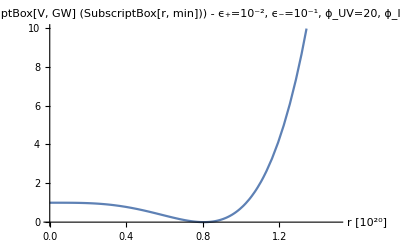

-45.8347

```mathematica
Print["Expand the GW potential and get in the form of CR and include the boundary term"]
Vboundary= -1/2(ϵm-ϵp)/l E^(-4 ηIR/l) ϕIR^2-ϵp/l ϕUV^2
(*Plusregioncont+Minusregioncont + Vboundary*)
Print["The above is a boundary term which is not needed, since we satisfy the junction conditions"]
Plusregioncont+Minusregioncont 
%/.ηIR ->- l Log[r ]/.r^4->rConf/.r^(2(2+ϵp))->rGW/.r^(-2(2+ϵp))->rGW^-1/.r^(2(2+ϵm))->rGWm
Series[%,{ϵp,0,1}]
Series[%,{ϵm,0,1}]//Simplify
%//Normal 
VGWexpanded=%/.rConf->r^4/.rGW->r^(2(2+ϵp))/.rGW^-1->r^(-2(2+ϵp))/.rGWm->r^(2(2+ϵm))//Simplify
Print["Now we find the minimum and stability of the potential. The first derivative is"]
(r^(3+2 ϵm) ϵm (4+2 ϵm) ϕIR^2-r^(3+2 ϵp) (4+2 ϵp) ϵp ϕUV^2)/(2 l r^(3+2 ϵp))//Simplify
Print["It has a unique root for positive r of"]
rsol=Solve[%%==0,r][[2]]
Print["The stability is determined by the sign of the second derivative there, which is"]
D[VGWexpanded/.ηIR->-l Log[r],{r,2}]
(*%/.{r->((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(1/(-ϵm+ϵp))}//PowerExpand//FullSimplify*)
%/.rsol//PowerExpand//FullSimplify
Print["The potential has the value of the following at the minimum"]
VGWatmin=VGWexpanded/.rsol//FullSimplify
Print["Now we plot the potential for some characteristic values. "]

constrepl={ϵp->0.01,ϵm->0.1,l->1,ϕUV->20,ϕIR->0.1}
r/.rsol/.constrepl
Plot[(VGWexpanded-VGWatmin)/(Abs@VGWatmin)/.constrepl/.r->rt 10^20,{rt,0,1.5 },PlotLabel->"V_GW/(SubscriptBox[V, GW] (SubscriptBox[r, min])) - ϵ_+=10^-2, ϵ_-=10^-1, ϕ_UV=20, ϕ_IR=10^-1, l=1",AxesLabel->{"r [10^20]"}]
-Log@r/.rsol/.constrepl
(*LogLogPlot[(VGWexpanded-VGWatmin)/-VGWatmin/.r->E^(η/l)/.constrepl,{η,0,50},PlotRange->All]*)
(*constrepl={ϵp->0.01,ϵm->0.1,l->1,ϕUV->0.5,ϕIR->5}
r/.rsol/.constrepl
VGWatmin/.constrepl
(VGWexpanded-VGWatmin)/-VGWatmin/.r->(r/2/.rsol)/.constrepl
VGWexpanded/.constrepl
Plot[(VGWexpanded-VGWatmin)/-VGWatmin/.constrepl,{r,0,2 10^-17},PlotRange->{0,10^-7}]
Plot[VGWexpanded-VGWatmin/.constrepl,{r,0,3 10^-17},PlotRange->All]
-Log@r/.rsol/.constrepl
LogLogPlot[(VGWexpanded-VGWatmin)/-VGWatmin/.r->E^(η/l)/.constrepl,{η,37,39},PlotRange->All]
VGWexpanded-VGWatmin/.r->E^(η/l)/.constrepl/.{{η->1},{η->10},{η->30},{η->37},{η->38},{η->38.5},{η->38.6},{η->38.7},{η->39}}*)
```

we now look for solutions which give the right PEW hierarchy and satisfy all the conditions we have so far laid out

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→Log[vevrat^2]/ProductLog[Log[vevrat^2]]}}

0.75703

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{ϵp→0.00503695}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{ϵm→0.00665357}

{ϵp→0.00503695,ϵm→0.00665357,l→1,ϕUV→1,ϕIR→0.814199}

5.28386×10^17

{5.28386×10^17,5.28386×10^17}

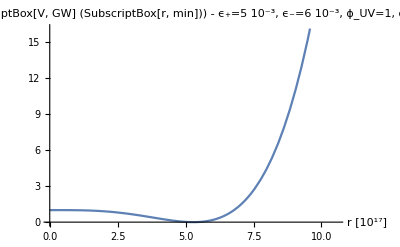

-40.8086

on the equality we have

ϵm^(-1/(2 ϵm-4 ϵp)) (2+ϵm)^(-1/(2 ϵm-4 ϵp)) ϵp^(1/(2 ϵm-4 ϵp)) (2+ϵp)^(1/(2 ϵm-4 ϵp))

```mathematica
Print["we now look for solutions which give the right PEW hierarchy and satisfy all the conditions we have so far laid out"]
Solve[x^x==vevrat^2,x]
x/.%[[1]]/.vevrat->0.9//N
Solve[%^(-1/ϵp)==10^24,ϵp][[1]]
Solve[ϵp/ϵm==%%/.%,ϵm][[1]]
constrepl={ϵp->(ϵp/.%%),ϵm->(ϵm/.%),l->1,ϕUV->1,(ϕIR->ϕUV ϵm^(ϵp/(2 ϵm-4 ϵp)) (2+ϵm)^(ϵp/(2 ϵm-4 ϵp)) ϵp^(-ϵp/(2 ϵm-4 ϵp)) (2+ϵp)^(-ϵp/(2 ϵm-4 ϵp))/.{ϵp->(ϵp/.%%),ϵm->(ϵm/.%),ϕUV->1})}
r/.rsol/.constrepl
{((√ϵm √(2+ϵm)vevrat)/(√ϵp √(2+ϵp)))^(1/(-ϵm+ϵp)),(vevrat)^(-1/ϵp)}/.vevrat->ϕIR/ϕUV/.constrepl

Plot[(VGWexpanded-VGWatmin)/(Abs@VGWatmin)/.constrepl/.r->rt 10^17,{rt,0,2 (%%)/10^17},PlotLabel->"V_GW/(SubscriptBox[V, GW] (SubscriptBox[r, min])) - ϵ_+=5 10^-3, ϵ_-=6 10^-3, ϕ_UV=1, ϕ_IR=8 10^-1",AxesLabel->{"r [10^17]"}]
-Log@r/.rsol/.constrepl
Print["on the equality we have"]
r/.rsol/.ϕIR->ϕUV ϵm^(ϵp/(2 ϵm-4 ϵp)) (2+ϵm)^(ϵp/(2 ϵm-4 ϵp)) ϵp^(-ϵp/(2 ϵm-4 ϵp)) (2+ϵp)^(-ϵp/(2 ϵm-4 ϵp))//PowerExpand//Simplify
```

Try substituting consistent insertion condition into the GW potential

```mathematica
VGWexpanded
consistentVGWexpanded=%/.ϕIR->ϕUV r^ϵp//Simplify
consistentrmin=Solve[D[%,r]==0,r][[2]]//Simplify
-l Log@r/.%//PowerExpand//FullSimplify
(*Series[%,{ϵm,0,0}]//Normal
Solve[%==a,ϵm]
%/.{a->37,ϵp->0.005,l->1}*)
Series[%,{ϵp,0,0}]//Normal
Solve[%==a,ϵp][[1]]//Normal//PowerExpand//Simplify
%/.{a->37,ϵm->0.01,l->1}
0.1/ϵp/.%
```

(r^(4+2 ϵm) ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)

((r^(2 (2+ϵm+ϵp)) ϵm+ϵp-r^(4+2 ϵp) ϵp) ϕUV^2)/(2 l)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{r→((√ϵp √(2+ϵp))/(√ϵm √(2+ϵm+ϵp)))^(1/ϵm)}

(l (Log[ϵm]-Log[ϵp]-Log[2+ϵp]+Log[2+ϵm+ϵp]))/(2 ϵm)

-(l (Log[2]-Log[ϵm]-Log[2+ϵm]+Log[ϵp]))/(2 ϵm)

{ϵp→1/2 ⅇ^(-(2 a ϵm)/l) ϵm (2+ϵm)}

{ϵp→0.00479499}

20.8551

```mathematica
Solve[E^-a == (ϵp/ϵm)^(1/(2 ϵm)),ϵp]//PowerExpand
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϵp→ⅇ^(-2 a ϵm) ϵm}}

```mathematica
D[consistentVGWexpanded,{r,2}]/.consistentrmin//PowerExpand//FullSimplify
```

(2 ϵm^((-1+ϵm-ϵp)/ϵm) ϵp^((1+ϵm+ϵp)/ϵm) (2+ϵp)^((1+ϵm+ϵp)/ϵm) (2+ϵm+ϵp)^(-(1+ϵp)/ϵm) ϕUV^2)/l

#### Compute GW potential - 1st order in ξ_ϕ

```mathematica
Print["ϕ stuff"]
ϕ0sol
ϕmsol = ϕIR E^(- ϵm (η-ηIR)/l)
ϕ0sol/.ϵ->ϵm/.C[0]->ϕIR E^(ϵm ηIR/l)//Simplify
ϕpsol=ϕUV E^(-ϵp η/l)
Print["metric stuff"]
detgηsmallμ0
Aofηsol/.C[2]->0/.C[1]->C[0]
(*Series[gη,{μ,0,1}]-Series[gη,{μ,0,0}]//Normal*)
Series[gη,{μ,0,0}]//Normal
Print["The effective action for the scalar away from the branes is"]
Leff = √detgηsmallμ0(%%[[5,5]] D[ϕ0[η]/.ϕ0sol,η]^2-1/2(ϵ(ϵ+4))/l^2 (ϕ0[η]/.ϕ0sol)^2+(κ ϵ^2)/(6 l^2)(ϕ0[η]/.ϕ0sol)^4)/.Aofηsol/.C[2]->0/.C[1]->C[0]//Simplify//PowerExpand
Print["At first order in the back reaction, this gives the 4D effective potential as"]
(*-Integrate[Leff/.M->∞,η]*)
(*-Integrate[Leff/.κ->0,η]*)
Series[Leff,{κ,0,1}];
-Integrate[%//Normal,η]//Simplify
Plusregioncont=(%/.η->ηIR/.ϵ->ϵp/.C[0]->ϕUV/.ϵ->ϵp)-(%/.η->0/.C[0]->ϕUV/.ϵ->ϵp)//Simplify
Minusregioncont=-(%%/.η->ηIR/.C[0]->ϕIR )/.ϵ->ϵm//Simplify
Print["This gives the effective potential"]
Plusregioncont+Minusregioncont
(*D[Plusregioncont+Minusregioncont,ηIR]//Simplify*)
(*Solve[%==0,ηIR]
ηIR/l/.%/.ϵp->ν ϵm/.ϵm->0.05
Plot[%,{ν,0,1}]*)
```

ϕ stuff

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR

ϕ0[η]→ⅇ^((ϵm (-η+ηIR))/l) ϕIR

ⅇ^(-(ϵp η)/l) ϕUV

metric stuff

ⅇ^(8 A[η])

A[η]→-η/l-1/12 ⅇ^(-(2 ϵ η)/l) κ C[0]^2

{{ⅇ^(2 A[η]),0,0,0,0},{0,-ⅇ^(2 A[η]),0,0,0},{0,0,-ⅇ^(2 A[η]),0,0},{0,0,0,-ⅇ^(2 A[η]),0},{0,0,0,0,-1}}

The effective action for the scalar away from the branes is

1/(6 l^2)ⅇ^(-(4 ϵ η)/l+1/2 (-(8 η)/l-2/3 ⅇ^(-(2 ϵ η)/l) κ C[0]^2)) ϵ C[0]^2 (-3 ⅇ^((2 ϵ η)/l) (4+3 ϵ)+ϵ κ C[0]^2)

At first order in the back reaction, this gives the 4D effective potential as

1/(12 l (2+ϵ))ⅇ^(-(4 (1+ϵ) η)/l) ϵ C[0]^2 (-3 ⅇ^((2 ϵ η)/l) (4+3 ϵ)+2 (2+ϵ) κ C[0]^2)

-((ⅇ^(-(4 (1+ϵp) ηIR)/l) ϵp ϕUV^2 (3 ⅇ^((2 ϵp ηIR)/l) (4+3 ϵp)-2 (2+ϵp) κ ϕUV^2+ⅇ^((4 (1+ϵp) ηIR)/l) (-12-9 ϵp+4 κ ϕUV^2+2 ϵp κ ϕUV^2)))/(12 l (2+ϵp)))

-((ⅇ^(-(4 (1+ϵm) ηIR)/l) ϵm ϕIR^2 (-3 ⅇ^((2 ϵm ηIR)/l) (4+3 ϵm)+2 (2+ϵm) κ ϕIR^2))/(12 l (2+ϵm)))

This gives the effective potential

-((ⅇ^(-(4 (1+ϵm) ηIR)/l) ϵm ϕIR^2 (-3 ⅇ^((2 ϵm ηIR)/l) (4+3 ϵm)+2 (2+ϵm) κ ϕIR^2))/(12 l (2+ϵm)))-(ⅇ^(-(4 (1+ϵp) ηIR)/l) ϵp ϕUV^2 (3 ⅇ^((2 ϵp ηIR)/l) (4+3 ϵp)-2 (2+ϵp) κ ϕUV^2+ⅇ^((4 (1+ϵp) ηIR)/l) (-12-9 ϵp+4 κ ϕUV^2+2 ϵp κ ϕUV^2)))/(12 l (2+ϵp))

```mathematica
Print["Expand the GW potential and get in the form of CR and include the boundary term"]
Vboundary= -1/2(ϵm-ϵp)/l E^(-4 ηIR/l) ϕIR^2-ϵp/l ϕUV^2
(*Plusregioncont+Minusregioncont + Vboundary*)
Print["The above is a boundary term which is not needed, since we satisfy the junction conditions"]
Plusregioncont+Minusregioncont 
%/.ηIR ->- l Log[r ]/.r^4->rConf/.r^(4(1+ϵp))->rGW/.r^(-4(1+ϵp))->rGW^-1/.r^(4(1+ϵm))->rGWm/.r^(-2 ϵm)->rϵm/.r^(-2 ϵp)->rϵp
Series[%,{ϵp,0,1}]
Series[%,{ϵm,0,1}]//Simplify
%//Normal 
VGWexpanded=%/.rConf->r^4/.rGW->r^(4(1+ϵp))/.rGW^-1->r^(-4(1+ϵp))/.rGWm->r^(4(1+ϵm))/.rϵm->r^(-2 ϵm)/.rϵp->r^(-2 ϵp)//Simplify
%/.ϕIR->ϕUV r^ϵp/.κ->ξϕ/ϕUV^2//Simplify
(Series[%,{ξϕ,0,1}]//Normal)-
(Series[%,{ξϕ,0,0}]//Normal)
(*TeXForm[%]*)
(*Print["Now we find the minimum and stability of the potential. Substitute in the dynamic value for ϕIR. The first derivative is"]*)
(*(r^(3+2 ϵm) ϵm (4+2 ϵm) ϕIR^2-r^(3+2 ϵp) (4+2 ϵp) ϵp ϕUV^2)/(2 l r^(3+2 ϵp))//Simplify*)
(*D[VGWexpanded,r]/(2 l r^3)/.ϕIR->ϕUV r^ϵp//Simplify
Print["It has a unique root for positive r of"]
rsol=Solve[%%==0,r][[2]]
Print["The stability is determined by the sign of the second derivative there, which is"]
D[VGWexpanded/.ϕIR->ϕUV r^ϵp/.ηIR->-l Log[r],{r,2}]
(*%/.{r->((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(1/(-ϵm+ϵp))}//PowerExpand//FullSimplify*)
%/.rsol//PowerExpand//FullSimplify
(*%/.κ->0*)
Print["The potential has the value of the following at the minimum"]
VGWatmin=VGWexpanded/.ϕIR->ϕUV r^ϵp/.rsol//FullSimplify
Print["Now we plot the potential for some characteristic values. "]

constrepl={ϵp->0.01,ϵm->0.1,l->1,ϕUV->20,ϕIR->0.1,κ->10^-6}
r/.ϕIR->ϕUV r^ϵp/.rsol/.constrepl
Plot[(VGWexpanded-VGWatmin)/(Abs@VGWatmin)/.constrepl/.r->rt 10^20,{rt,0,1.2 },PlotLabel->"V_GW/(SubscriptBox[V, GW](SubscriptBox[r, min])) - ϵ_+=10^-2, ϵ_-=10^-1, ϕ_UV=20, ϕ_IR=10^-1, l=1",AxesLabel->{"r [10^20]"}]
-Log@r/.rsol/.constrepl*)
(*LogLogPlot[(VGWexpanded-VGWatmin)/-VGWatmin/.r->E^(η/l)/.constrepl,{η,0,50},PlotRange->All]*)
(*constrepl={ϵp->0.01,ϵm->0.1,l->1,ϕUV->0.5,ϕIR->5}
r/.rsol/.constrepl
VGWatmin/.constrepl
(VGWexpanded-VGWatmin)/-VGWatmin/.r->(r/2/.rsol)/.constrepl
VGWexpanded/.constrepl
Plot[(VGWexpanded-VGWatmin)/-VGWatmin/.constrepl,{r,0,2 10^-17},PlotRange->{0,10^-7}]
Plot[VGWexpanded-VGWatmin/.constrepl,{r,0,3 10^-17},PlotRange->All]
-Log@r/.rsol/.constrepl
LogLogPlot[(VGWexpanded-VGWatmin)/-VGWatmin/.r->E^(η/l)/.constrepl,{η,37,39},PlotRange->All]
VGWexpanded-VGWatmin/.r->E^(η/l)/.constrepl/.{{η->1},{η->10},{η->30},{η->37},{η->38},{η->38.5},{η->38.6},{η->38.7},{η->39}}*)
```

Expand the GW potential and get in the form of CR and include the boundary term

-(ⅇ^(-(4 ηIR)/l) (ϵm-ϵp) ϕIR^2)/(2 l)-(ϵp ϕUV^2)/l

The above is a boundary term which is not needed, since we satisfy the junction conditions

-((ⅇ^(-(4 (1+ϵm) ηIR)/l) ϵm ϕIR^2 (-3 ⅇ^((2 ϵm ηIR)/l) (4+3 ϵm)+2 (2+ϵm) κ ϕIR^2))/(12 l (2+ϵm)))-(ⅇ^(-(4 (1+ϵp) ηIR)/l) ϵp ϕUV^2 (3 ⅇ^((2 ϵp ηIR)/l) (4+3 ϵp)-2 (2+ϵp) κ ϕUV^2+ⅇ^((4 (1+ϵp) ηIR)/l) (-12-9 ϵp+4 κ ϕUV^2+2 ϵp κ ϕUV^2)))/(12 l (2+ϵp))

-((rGWm ϵm ϕIR^2 (-3 rϵm (4+3 ϵm)+2 (2+ϵm) κ ϕIR^2))/(12 l (2+ϵm)))-(rGW ϵp ϕUV^2 (3 rϵp (4+3 ϵp)-2 (2+ϵp) κ ϕUV^2+(-12-9 ϵp+4 κ ϕUV^2+2 ϵp κ ϕUV^2)/rGW))/(12 l (2+ϵp))

-((rGWm ϵm ϕIR^2 (-3 rϵm (4+3 ϵm)+2 (2+ϵm) κ ϕIR^2))/(12 (l (2+ϵm))))+(ϕUV^2 (3-3 rGW rϵp-κ ϕUV^2+rGW κ ϕUV^2) ϵp)/(6 l)+O[ϵp]^2

(-((rGWm ϕIR^2 (-3 rϵm+κ ϕIR^2)) ϵm)/(6 l)+O[ϵm]^2)+(ϕUV^2 (3-3 rGW rϵp-κ ϕUV^2+rGW κ ϕUV^2) ϵp)/(6 l)+O[ϵp]^2

-(rGWm ϵm ϕIR^2 (-3 rϵm+κ ϕIR^2))/(6 l)+(ϵp ϕUV^2 (3-3 rGW rϵp-κ ϕUV^2+rGW κ ϕUV^2))/(6 l)

1/(6 l)(3 r^(4+2 ϵm) ϵm ϕIR^2-r^(4+4 ϵm) ϵm κ ϕIR^4+3 ϵp ϕUV^2-3 r^(4+2 ϵp) ϵp ϕUV^2-ϵp κ ϕUV^4+r^(4+4 ϵp) ϵp κ ϕUV^4)

-1/(6 l)(-3 r^(2 (2+ϵm+ϵp)) ϵm+3 r^(4+2 ϵp) ϵp+ϵp (-3+ξϕ)+r^(4 (1+ϵm+ϵp)) ϵm ξϕ-r^(4+4 ϵp) ϵp ξϕ) ϕUV^2

((-r^(4 (1+ϵm+ϵp)) ϵm-ϵp+r^(4+4 ϵp) ϵp) ξϕ ϕUV^2)/(6 l)

Try substituting consistent insertion condition into the GW potential

```mathematica
AnalyzePotential[Pot_]:=Module[{rmin,stability},
rmin=Solve[D[Pot,r]==0,r]//Simplify;
-l Log@r/.rmin//PowerExpand//FullSimplify;
stability=D[Pot,{r,2}]/.rmin//FullSimplify;
Print[rmin];
Print[stability]
]
```

```mathematica
AnalyzePotential[VGWexpanded/.ϕIR->ϕUV r^ϵp/.κ->0]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→(-(√ϵp √(2+ϵp))/(√ϵm √(2+ϵm+ϵp)))^(1/ϵm)},{r→((√ϵp √(2+ϵp))/(√ϵm √(2+ϵm+ϵp)))^(1/ϵm)}}

{1/l(-ϵp (2+ϵp) ((-(√ϵp √(2+ϵp))/(√ϵm √(2+ϵm+ϵp)))^(1/ϵm))^(2 (1+ϵp)) (3+2 ϵp) ϕUV^2+ϵm ((-(√ϵp √(2+ϵp))/(√ϵm √(2+ϵm+ϵp)))^(1/ϵm))^(2 (1+ϵm+ϵp)) (2+ϵm+ϵp) (3+2 ϵm+2 ϵp) ϕUV^2),1/l(-ϵp (2+ϵp) (((√ϵp √(2+ϵp))/(√ϵm √(2+ϵm+ϵp)))^(1/ϵm))^(2 (1+ϵp)) (3+2 ϵp) ϕUV^2+ϵm (((√ϵp √(2+ϵp))/(√ϵm √(2+ϵm+ϵp)))^(1/ϵm))^(2 (1+ϵm+ϵp)) (2+ϵm+ϵp) (3+2 ϵm+2 ϵp) ϕUV^2)}

-((-3 r^(2 (2+ϵm+ϵp)) ϵm+3 r^(4+2 ϵp) ϵp+ϵp (-3+ξ)+r^(4 (1+ϵm+ϵp)) ϵm ξ-r^(4+4 ϵp) ϵp ξ) ϕUV^2)/(6 l)

{ϵp→0.01,ϵm→0.1,l→1,ϕUV→1,ξ→0.01}

1/6 (0.0299-0.03 r^4.02+0.0001 r^4.04+0.3 r^4.22-0.001 r^4.44)

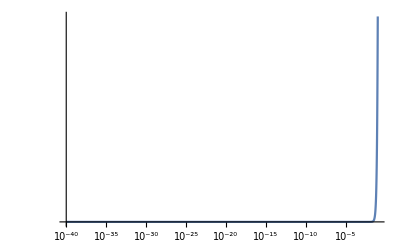

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→0}}

{{1/(6 l)(3 ϵm (3+2 ϵm) (4+2 ϵm) ϕIR^2 (r→0)^(2+2 ϵm)-ϵm (3+4 ϵm) (4+4 ϵm) κ ϕIR^4 (r→0)^(2+4 ϵm)-3 ϵp (3+2 ϵp) (4+2 ϵp) ϕUV^2 (r→0)^(2+2 ϵp)+ϵp (3+4 ϵp) (4+4 ϵp) κ ϕUV^4 (r→0)^(2+4 ϵp))}}

```mathematica
VGWexpanded/.ϕIR->ϕUV r^ϵp/.κ->ξ/ϕUV^2//Simplify
constrepl={ϵp->0.01,ϵm->0.1,l->1,ϕUV->1,ξ->0.01}
%%/.constrepl
(*NSolve[%==0,r]*)
LogLogPlot[%,{r,10^-40,10^-1}]
```

```mathematica
VGWexpanded
(*consistentVGWexpanded=%/.ϕIR->ϕUV r^-ϵp/.κ->ξ/ϕUV^2//Simplify*)
consistentVGWexpanded=%/.ϕIR->ϕUV r^-ϵp/.κ->ξ/ϕUV^2//Simplify
%//Simplify
consistentrmin=Solve[D[%,r]==0,r][[4]]//FullSimplify
-l Log@r/.%//PowerExpand//FullSimplify
(*Series[r/.consistentrmin,{ξ,0,1}]//Normal
-l Log@%//PowerExpand//FullSimplify*)
(*Series[%,{ϵm,0,0}]//Normal
Solve[%==a,ϵm]
%/.{a->37,ϵp->0.005,l->1}*)
Series[%,{ϵp,0,0}]//Normal//PowerExpand//Simplify
Solve[%==a,ϵp][[1]]//Normal//PowerExpand//Simplify
%/.{a->37,ϵm->0.001,l->1,ξ->0.001}
0.001/ϵp/.%
```

(-r^4 ϵm ϕIR^2 (-3+κ ϕIR^2)+(-1+r^4) ϵp ϕUV^2 (-3+κ ϕUV^2))/(6 l)

((r^(4-4 ϵp) ϵm (3 r^(2 ϵp)-ξ)+(-1+r^4) ϵp (-3+ξ)) ϕUV^2)/(6 l)

((r^(4-4 ϵp) ϵm (3 r^(2 ϵp)-ξ)+(-1+r^4) ϵp (-3+ξ)) ϕUV^2)/(6 l)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{r→2^(-1/ϵp) ((3 ϵm (-2+ϵp)+√(ϵm (9 ϵm (-2+ϵp)^2-16 (-1+ϵp) ϵp (-3+ξ) ξ)))/(ϵp (-3+ξ)))^(1/2/ϵp)}

(l (Log[4]+Log[ϵp]+Log[-3+ξ]-Log[3 ϵm (-2+ϵp)+√ϵm √(9 ϵm (-2+ϵp)^2-16 (-1+ϵp) ϵp (-3+ξ) ξ)]))/(2 ϵp)

1/36 l (9+(2 (-3+ξ) ξ)/ϵm+(18 (Log[3]+Log[-3+ξ]-Log[(-3+ξ) ξ]))/ϵp)

{ϵp→(18 l ϵm Log[ξ/3])/(-36 a ϵm+9 l ϵm+2 l (-3+ξ) ξ)}

{ϵp→0.108439}

0.00922181

```mathematica
((r^(4+2 ϵm-2 ϵp) ϵm+ϵp-r^(4+2 ϵp) ϵp) ϕUV^2)/(2 l)
D[%,r]
Solve[%==0,r]//PowerExpand//FullSimplify//PowerExpand
-l Log@r/.%//PowerExpand//FullSimplify
```

((r^(4+2 ϵm-2 ϵp) ϵm+ϵp-r^(4+2 ϵp) ϵp) ϕUV^2)/(2 l)

((r^(3+2 ϵm-2 ϵp) ϵm (4+2 ϵm-2 ϵp)-r^(3+2 ϵp) ϵp (4+2 ϵp)) ϕUV^2)/(2 l)

{{r→ⅇ^((-Log[ϵm]-Log[2+ϵm-ϵp]+Log[ϵp]+Log[2+ϵp])/(2 (ϵm-2 ϵp)))}}

{(l (Log[ϵm]+Log[2+ϵm-ϵp]-Log[ϵp]-Log[2+ϵp]))/(2 (ϵm-2 ϵp))}

```mathematica
D[consistentVGWexpanded,{r,2}]
Series[%,{ξ,0,1}]//PowerExpand//Simplify//Normal
%/.consistentrmin//PowerExpand//FullSimplify
```

((12 r^(2-2 ϵp) ϵm (4-4 ϵp) ϵp+6 r^(2-2 ϵp) ϵm ϵp (-1+2 ϵp)+r^(2-4 ϵp) ϵm (3-4 ϵp) (4-4 ϵp) (3 r^(2 ϵp)-ξ)+12 r^2 ϵp (-3+ξ)) ϕUV^2)/(6 l)

-(r^(2-2 ϵp) (6 r^(2 ϵp) ϵp+ϵm (-6+7 ϵp-2 ϵp^2)) ϕUV^2)/l+(2 r^2 (3 ϵp-r^(-4 ϵp) ϵm (-1+ϵp) (-3+4 ϵp)) ξ ϕUV^2)/(3 l)

-((2^(3-2/ϵp) ϵp^(2-1/ϵp) (-3+ξ)^((-1+ϵp)/ϵp) (3 ϵm (-2+ϵp)+√ϵm √(9 ϵm (-2+ϵp)^2-16 (-1+ϵp) ϵp (-3+ξ) ξ))^(1/ϵp) (-9 ϵm (-2+ϵp)^2+16 (-1+ϵp) ϵp (-3+ξ) ξ-3 √ϵm (-2+ϵp) √(9 ϵm (-2+ϵp)^2-16 (-1+ϵp) ϵp (-3+ξ) ξ)) ϕUV^2)/(3 l (3 √ϵm (-2+ϵp)+√(9 ϵm (-2+ϵp)^2-16 (-1+ϵp) ϵp (-3+ξ) ξ))^2))

#### Try to reproduce Zamir’s BR calculation

```mathematica
χ=k E^(- k yc - r[x] E^(2k yc))
D[D[χ,x]^2,r[x]]
(*D[D[χ,x]^2,r'[x]]
%% - D[%,x]//Simplify*)
```

ⅇ^(-k yc-ⅇ^(2 k yc) r[x]) k

-2 ⅇ^(4 k yc-2 ⅇ^(2 k yc) r[x]) k^2 r'[x]^2

```mathematica
Solve[χt[x]==χ,r[x]][[1]]/.C[1]->0
D[r[x]/.%,{x,1}]
```

{r[x]→-ⅇ^(-2 k yc) (k yc-Log[k/χt[x]])}

-(ⅇ^(-2 k yc) χt'[x])/χt[x]

#### Consider both ϕ solutions consistent with EOM and JCs

```mathematica
ABsol={A,B}/.Solve[{ϕIR == B E^(-ϵ/l ηIR)+A E^((4+ϵ)/l ηIR)
,ϕUV == A + B},{A,B}][[1]]/.ηIR->l Log[r]//Simplify

ABsol (-1+r^(4 + 2  ϵ)) (Series[-1/(1-x),{x,∞,2}]//Normal)/.x->r^(4+2  ϵ)//Simplify//PowerExpand
%//Expand
ExpandedABsol={r^(4+3 ϵ-4 (2+ϵ)) ϕIR-r^(4+2 ϵ-4 (2+ϵ)) ϕUV,-r^(-4-ϵ) ϕIR+ϕUV+r^(-4-2 ϵ) ϕUV}//Simplify
(*Series[%,{ϵ,0,1}]//Normal
Series[%,{r,∞,4}]//Normal*)
```

{(r^ϵ ϕIR-ϕUV)/(-1+r^(4+2 ϵ)),(r^ϵ (-ϕIR+r^(4+ϵ) ϕUV))/(-1+r^(4+2 ϵ))}

{r^(-4 (2+ϵ)) (1+r^(4+2 ϵ)) (r^ϵ ϕIR-ϕUV),r^(-8-3 ϵ) (1+r^(4+2 ϵ)) (-ϕIR+r^(4+ϵ) ϕUV)}

{r^(ϵ-4 (2+ϵ)) ϕIR+r^(4+3 ϵ-4 (2+ϵ)) ϕIR-r^(-4 (2+ϵ)) ϕUV-r^(4+2 ϵ-4 (2+ϵ)) ϕUV,-r^(-8-3 ϵ) ϕIR-r^(-4-ϵ) ϕIR+ϕUV+r^(-4-2 ϵ) ϕUV}

{r^(-2 (2+ϵ)) (r^ϵ ϕIR-ϕUV),-r^(-4-ϵ) ϕIR+ϕUV+r^(-2 (2+ϵ)) ϕUV}

```mathematica
Limit[ABsol,r->∞]
Limit[D[ABsol,r],r->∞]
Limit[D[ABsol,{r,2}],r->∞]
```

{ConditionalExpression[0, (ϕIR|ϕUV)∈ℝ&&ϵ>0],ConditionalExpression[ϕUV, (ϕIR|ϕUV)∈ℝ&&ϵ>0]}

{ConditionalExpression[0, (ϕIR|ϕUV)∈ℝ&&0<ϵ<1],ConditionalExpression[0, (ϕUV|ϕIR)∈ℝ&&0<ϵ<1]}

{ConditionalExpression[0, (ϕIR|ϕUV)∈ℝ&&0<ϵ<2],ConditionalExpression[0, (ϕUV|ϕIR)∈ℝ&&0<ϵ<1]}

```mathematica
1/r^(4+2ϵ)Series[1/(1-r^(-4-2ϵ)),{r,∞,2}]
```

r^(-4-2 ϵ)/(1-r^(-4-2 ϵ))

```mathematica
Series[1/(1-x),{x,0,2}]
```

1+x+x^2+O[x]^3

```mathematica
Series[(r^ϵ (-ϕIR+r^(4+ϵ) ϕUV))/(-1+r^(4+2 ϵ)),{r,∞,1}]
```

(r^ϵ (-ϕIR+r^(4+ϵ) ϕUV))/(-1+r^(4+2 ϵ))

```mathematica
Print["The full solution in the + region is:"]
ϕpbothsols=ABsol{ⅇ^(((4+ϵ) η)/l),E^(-ϵ η/l)}/.r->E^(ηIR/l)//PowerExpand//Total//Simplify
%/.η->0//Simplify
(D[%%,η]==-ϵ/l ϕIR/.η->ηIR//Simplify)
(D[%%%,η]==-ϵ/l ϕUV/.η->0//Simplify)
Print["So both junction conditions are satisfied provided ϕIR = E^(-ϵ FractionBox[ηIR, l])ϕUV, which should be satsified on the minimum of the potential"]
```

The full solution in the + region is:

(ⅇ^(-(ϵ η)/l) (-ⅇ^((ϵ ηIR)/l) ϕIR+ⅇ^((2 (2+ϵ) η+ϵ ηIR)/l) ϕIR-ⅇ^((2 (2+ϵ) η)/l) ϕUV+ⅇ^((2 (2+ϵ) ηIR)/l) ϕUV))/(-1+ⅇ^((2 (2+ϵ) ηIR)/l))

ϕUV

(ⅇ^(((4+ϵ) ηIR)/l) (2+ϵ) (ⅇ^((ϵ ηIR)/l) ϕIR-ϕUV))/((-1+ⅇ^((2 (2+ϵ) ηIR)/l)) l)==0

((2+ϵ) (ⅇ^((ϵ ηIR)/l) ϕIR-ϕUV))/((-1+ⅇ^((2 (2+ϵ) ηIR)/l)) l)==0

So both junction conditions are satisfied provided ϕIR = E^(-ϵ FractionBox[ηIR, l])ϕUV, which should be satsified on the minimum of the potential

```mathematica
ϕmsol = ϕIR E^(-ϵm (η-ηIR)/l)
ϕtotalbothsols = (ϕpbothsols/.ϵ->ϵp)HeavisideTheta[ηIR-η] + ϕmsol HeavisideTheta[η-ηIR]
```

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR HeavisideTheta[η-ηIR]+(ⅇ^(-(ϵp η)/l) (-ⅇ^((ϵp ηIR)/l) ϕIR+ⅇ^((2 (2+ϵp) η+ϵp ηIR)/l) ϕIR-ⅇ^((2 (2+ϵp) η)/l) ϕUV+ⅇ^((2 (2+ϵp) ηIR)/l) ϕUV) HeavisideTheta[-η+ηIR])/(-1+ⅇ^((2 (2+ϵp) ηIR)/l))

```mathematica
ExpandedABsol{ⅇ^(((4+ϵ) η)/l),E^(-ϵ η/l)}/.r->E^(ηIR/l)//PowerExpand//Total//Simplify
ϕmsol = ϕIR E^(-ϵm (η-ηIR)/l)
ϕtotalbothsolsExpanded = (%%/.ϵ->ϵp)HeavisideTheta[ηIR-η] + ϕmsol HeavisideTheta[η-ηIR]
```

ⅇ^(-(ϵ η+4 ηIR+2 ϵ ηIR)/l) (-ⅇ^((ϵ ηIR)/l) ϕIR+ⅇ^((2 (2+ϵ) η+ϵ ηIR)/l) ϕIR+ϕUV-ⅇ^((2 (2+ϵ) η)/l) ϕUV+ⅇ^((2 (2+ϵ) ηIR)/l) ϕUV)

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR HeavisideTheta[η-ηIR]+ⅇ^(-(ϵp η+4 ηIR+2 ϵp ηIR)/l) (-ⅇ^((ϵp ηIR)/l) ϕIR+ⅇ^((2 (2+ϵp) η+ϵp ηIR)/l) ϕIR+ϕUV-ⅇ^((2 (2+ϵp) η)/l) ϕUV+ⅇ^((2 (2+ϵp) ηIR)/l) ϕUV) HeavisideTheta[-η+ηIR]

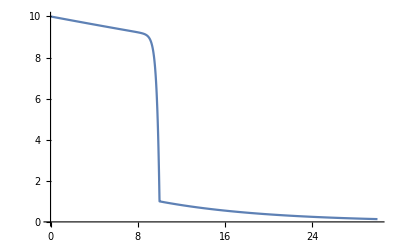

```mathematica
Plot[ϕtotalbothsols/.η->ηt/.{l->1,ϵp->0.01,ϵm->0.1,ηIR->10,ϕIR->1,ϕUV->10},{ηt,0,30},PlotRange->{0,10}]
```

```mathematica
Plot[ϕtotalbothsolsExpanded/.η->ηt/.{l->1,ϵp->0.01,ϵm->0.1,ηIR->10,ϕIR->1,ϕUV->10},{ηt,0,30},PlotRange->{0,10}]
```

-Graphics-

```mathematica
pregionVeff = Assuming[ηIR>0,Integrate[ϕtotalbothsolsExpanded,{η,0,ηIR}]//Simplify]
```

1/(ϵp (4+ϵp))ⅇ^(-((4+3 ϵp) ηIR)/l) l (-2 ⅇ^((2 ϵp ηIR)/l) (2+ϵp) ϕIR-2 ⅇ^((2 (2+ϵp) ηIR)/l) (2+ϵp) ϕUV-(4+ϵp) ϕUV+ⅇ^((ϵp ηIR)/l) ((4+ϵp) ϕIR+2 (2+ϵp) ϕUV)+ⅇ^(((4+3 ϵp) ηIR)/l) (4 ϕUV+ϵp (ϕIR+ϕUV)))

```mathematica
mregionVeff=Assuming[ηIR>0,Integrate[ϕtotalbothsolsExpanded,{η,ηIR,∞}]//Simplify]
```

ConditionalExpression[(l ϕIR)/ϵm, Re[ϵm/l]>0]

```mathematica
pregionVeff + mregionVeff
%/.ηIR ->- l Log[r ]/.r^4->rConf/.r^(2(2+ϵp))->rGW/.r^(-2(2+ϵp))->rGW^-1
Series[%,{ϵp,0,0}]
Assuming[Re[ϵm/l]>0,Series[%,{ϵm,0,0}]]//Simplify
%//Normal 
VGWexpandedboth=%/.rConf->r^4/.rGW->r^(2(2+ϵp))/.rGW^-1->r^(-2(2+ϵp))//Simplify
```

ConditionalExpression[(l ϕIR)/ϵm+1/(ϵp (4+ϵp))ⅇ^(-((4+3 ϵp) ηIR)/l) l (-2 ⅇ^((2 ϵp ηIR)/l) (2+ϵp) ϕIR-2 ⅇ^((2 (2+ϵp) ηIR)/l) (2+ϵp) ϕUV-(4+ϵp) ϕUV+ⅇ^((ϵp ηIR)/l) ((4+ϵp) ϕIR+2 (2+ϵp) ϕUV)+ⅇ^(((4+3 ϵp) ηIR)/l) (4 ϕUV+ϵp (ϕIR+ϕUV))), Re[ϵm/l]>0]

ConditionalExpression[(l ϕIR)/ϵm+(l r^(4+3 ϵp) (-2 r^(-2 ϵp) (2+ϵp) ϕIR-(2 (2+ϵp) ϕUV)/rGW-(4+ϵp) ϕUV+r^-ϵp ((4+ϵp) ϕIR+2 (2+ϵp) ϕUV)+r^(-4-3 ϵp) (4 ϕUV+ϵp (ϕIR+ϕUV))))/(ϵp (4+ϵp)), Re[ϵm/l]>0]

ConditionalExpression[-(l (r^4-rGW) ϕUV)/(rGW ϵp)+((l ϕIR)/ϵm-(l (-rGW ϕIR+r^4 rGW ϕIR+r^4 ϕUV-r^4 rGW ϕUV-4 r^4 rGW ϕIR Log[r]+12 r^4 ϕUV Log[r]+4 r^4 rGW ϕUV Log[r]))/(4 rGW))+O[ϵp]^1, Re[ϵm/l]>0]

(l (-r^4+rGW) ϕUV)/(rGW ϵp)+((l ϕIR)/ϵm+(l (-r^4 ϕUV+rGW (ϕIR-r^4 ϕIR+r^4 ϕUV)+4 r^4 (rGW (ϕIR-ϕUV)-3 ϕUV) Log[r]))/(4 rGW)+O[ϵm]^1)+O[ϵp]^1

(l ϕIR)/ϵm+(l (-r^4+rGW) ϕUV)/(rGW ϵp)+(l (-r^4 ϕUV+rGW (ϕIR-r^4 ϕIR+r^4 ϕUV)+4 r^4 (rGW (ϕIR-ϕUV)-3 ϕUV) Log[r]))/(4 rGW)

(l r^(-2 ϵp) (-r^(4+2 ϵp) ϵm ϵp (ϕIR-ϕUV)-ϵm (4+ϵp) ϕUV+r^(2 ϵp) ((4+ϵm) ϵp ϕIR+4 ϵm ϕUV)+4 ϵm ϵp (r^(4+2 ϵp) (ϕIR-ϕUV)-3 ϕUV) Log[r]))/(4 ϵm ϵp)

#### Look for a potential which has the above domain wall solutions

```mathematica
U''[a1]==m1^2
U''[a2]==m2^2
U'[a1]==U'[a2]==0
```

U''[a1]==m1^2

U''[a2]==m2^2

U'[a1]==U'[a2]==0

```mathematica
f = a r^4+b r^3 + c r^2 + d r
sol=Solve[{D[f,{r,2}]==m1^2/.r->r1//Simplify,
D[f,{r,2}]==m2^2/.r->r2//Simplify,
D[f,{r,1}]==0/.r->r1//Simplify,
D[f,{r,1}]==0/.r->r2//Simplify},{a,b,c,d}][[1]]
f/.sol//FullSimplify
%/.{m1->√(ϵm(ϵm+4)),m2->√(ϵp(ϵp+4))}//FullSimplify
(*Solve[{D[a(r^2-c)^2+b(r^2-d^2)^2,{r,2}]==m1^2/.r->c//Simplify,
D[a(r^2-c)^2+b(r^2-d^2)^2,{r,2}]==m2^2/.r->d//Simplify,
D[a(r^2-c)^2+b(r^2-d^2)^2,{r,1}]==0/.r->c//Simplify,
D[a(r^2-c)^2+b(r^2-d^2)^2,{r,1}]==0/.r->d//Simplify},{a,b,c,d}]*)
```

d r+c r^2+b r^3+a r^4

{a→-(-m1^2-m2^2)/(4 (r1-r2)^2),b→-(m1^2 r1+2 m2^2 r1+2 m1^2 r2+m2^2 r2)/(3 (r1-r2)^2),c→-(-m2^2 r1^2-2 m1^2 r1 r2-2 m2^2 r1 r2-m1^2 r2^2)/(2 (r1-r2)^2),d→-(m2^2 r1^2 r2+m1^2 r1 r2^2)/(r1-r2)^2}

(r (m1^2 (3 r^3-12 r1 r2^2+6 r r2 (2 r1+r2)-4 r^2 (r1+2 r2))+m2^2 (3 r^3-12 r1^2 r2-4 r^2 (2 r1+r2)+6 r r1 (r1+2 r2))))/(12 (r1-r2)^2)

(r ((3 r^3-12 r1 r2^2+6 r r2 (2 r1+r2)-4 r^2 (r1+2 r2)) ϵm (4+ϵm)+(3 r^3-12 r1^2 r2-4 r^2 (2 r1+r2)+6 r r1 (r1+2 r2)) ϵp (4+ϵp)))/(12 (r1-r2)^2)

```mathematica
f = a ϕ^4+b ϕ^3 + c ϕ^2 + d ϕ
sol=Solve[{D[f,{ϕ,2}]==m1^2/.ϕ->ϕ1//Simplify,
D[f,{ϕ,2}]==m2^2/.ϕ->ϕ2//Simplify,
D[f,{ϕ,1}]==0/.ϕ->ϕ1//Simplify,
D[f,{ϕ,1}]==0/.ϕ->ϕ2//Simplify},{a,b,c,d}][[1]]
f/.sol//Expand
%/.{m1->√(ϵm(ϵm+4)),m2->√(ϵp(ϵp+4))}//Simplify
Series[%,{ϕ,0,4}]
```

d ϕ+c ϕ^2+b ϕ^3+a ϕ^4

{a→-(-m1^2-m2^2)/(4 (ϕ1-ϕ2)^2),b→-(m1^2 ϕ1+2 m2^2 ϕ1+2 m1^2 ϕ2+m2^2 ϕ2)/(3 (ϕ1-ϕ2)^2),c→-(-m2^2 ϕ1^2-2 m1^2 ϕ1 ϕ2-2 m2^2 ϕ1 ϕ2-m1^2 ϕ2^2)/(2 (ϕ1-ϕ2)^2),d→-(m2^2 ϕ1^2 ϕ2+m1^2 ϕ1 ϕ2^2)/(ϕ1-ϕ2)^2}

(m1^2 ϕ^4)/(4 (ϕ1-ϕ2)^2)+(m2^2 ϕ^4)/(4 (ϕ1-ϕ2)^2)-(m1^2 ϕ^3 ϕ1)/(3 (ϕ1-ϕ2)^2)-(2 m2^2 ϕ^3 ϕ1)/(3 (ϕ1-ϕ2)^2)+(m2^2 ϕ^2 ϕ1^2)/(2 (ϕ1-ϕ2)^2)-(2 m1^2 ϕ^3 ϕ2)/(3 (ϕ1-ϕ2)^2)-(m2^2 ϕ^3 ϕ2)/(3 (ϕ1-ϕ2)^2)+(m1^2 ϕ^2 ϕ1 ϕ2)/(ϕ1-ϕ2)^2+(m2^2 ϕ^2 ϕ1 ϕ2)/(ϕ1-ϕ2)^2-(m2^2 ϕ ϕ1^2 ϕ2)/(ϕ1-ϕ2)^2+(m1^2 ϕ^2 ϕ2^2)/(2 (ϕ1-ϕ2)^2)-(m1^2 ϕ ϕ1 ϕ2^2)/(ϕ1-ϕ2)^2

1/(12 (ϕ1-ϕ2)^2)ϕ (4 ϵm (3 ϕ^3-12 ϕ1 ϕ2^2+6 ϕ ϕ2 (2 ϕ1+ϕ2)-4 ϕ^2 (ϕ1+2 ϕ2))+ϵm^2 (3 ϕ^3-12 ϕ1 ϕ2^2+6 ϕ ϕ2 (2 ϕ1+ϕ2)-4 ϕ^2 (ϕ1+2 ϕ2))+ϵp (4+ϵp) (3 ϕ^3-12 ϕ1^2 ϕ2-4 ϕ^2 (2 ϕ1+ϕ2)+6 ϕ ϕ1 (ϕ1+2 ϕ2)))

((-12 ϵp (4+ϵp) ϕ1^2 ϕ2-48 ϵm ϕ1 ϕ2^2-12 ϵm^2 ϕ1 ϕ2^2) ϕ)/(12 (ϕ1-ϕ2)^2)+((24 ϵm ϕ2 (2 ϕ1+ϕ2)+6 ϵm^2 ϕ2 (2 ϕ1+ϕ2)+6 ϵp (4+ϵp) ϕ1 (ϕ1+2 ϕ2)) ϕ^2)/(12 (ϕ1-ϕ2)^2)+((-4 ϵp (4+ϵp) (2 ϕ1+ϕ2)-16 ϵm (ϕ1+2 ϕ2)-4 ϵm^2 (ϕ1+2 ϕ2)) ϕ^3)/(12 (ϕ1-ϕ2)^2)+((4 ϵm+ϵm^2+4 ϵp+ϵp^2) ϕ^4)/(4 (ϕ1-ϕ2)^2)+O[ϕ]^5

```mathematica
f = a r^4+b r^3 + c r^2 + d r/.r->E^(-η/l)
sol=Solve[{D[f,{η,2}]==m1^2/.η->r1//Simplify,
D[f,{η,2}]==m2^2/.η->r2//Simplify,
D[f,{η,1}]==0/.η->r1//Simplify,
D[f,{η,1}]==0/.η->r2//Simplify},{a,b,c,d}][[1]]
f/.sol/.r2->0/.r1-> ηIR//FullSimplify
%/.{m1->√(ϵm(ϵm+4)),m2->√(ϵp(ϵp+4))}//FullSimplify
```

a ⅇ^(-(4 η)/l)+b ⅇ^(-(3 η)/l)+c ⅇ^(-(2 η)/l)+d ⅇ^(-η/l)

{a→(ⅇ^((2 r1)/l+(2 r2)/l) l^2 (ⅇ^((2 r1)/l) m1^2+ⅇ^((2 r2)/l) m2^2))/(4 (-ⅇ^(r1/l)+ⅇ^(r2/l))^2),b→-(ⅇ^(r1/l+r2/l) l^2 (2 ⅇ^((3 r1)/l) m1^2+ⅇ^((2 r1)/l+r2/l) m1^2+2 ⅇ^((3 r2)/l) m2^2+ⅇ^(r1/l+(2 r2)/l) m2^2))/(3 (-ⅇ^(r1/l)+ⅇ^(r2/l))^2),c→(l^2 (ⅇ^((4 r1)/l) m1^2+2 ⅇ^((3 r1)/l+r2/l) m1^2+ⅇ^((4 r2)/l) m2^2+2 ⅇ^(r1/l+(3 r2)/l) m2^2))/(2 (ⅇ^(r1/l)-ⅇ^(r2/l))^2),d→-(l^2 (ⅇ^((3 r1)/l) m1^2+ⅇ^((3 r2)/l) m2^2))/((ⅇ^(r1/l)-ⅇ^(r2/l))^2)}

1/(12 (-1+ⅇ^(ηIR/l))^2)ⅇ^(-(4 η)/l) l^2 (3 ⅇ^((2 ηIR)/l) (ⅇ^((2 ηIR)/l) m1^2+m2^2)-12 ⅇ^((3 η)/l) (ⅇ^((3 ηIR)/l) m1^2+m2^2)+6 ⅇ^((2 η)/l) (2 ⅇ^((3 ηIR)/l) m1^2+ⅇ^((4 ηIR)/l) m1^2+m2^2+2 ⅇ^(ηIR/l) m2^2)-4 ⅇ^((η+ηIR)/l) (2 m2^2+ⅇ^(ηIR/l) (ⅇ^(ηIR/l) (1+2 ⅇ^(ηIR/l)) m1^2+m2^2)))

1/(12 (-1+ⅇ^(ηIR/l))^2)ⅇ^(-(4 η)/l) l^2 (3 ⅇ^((2 ηIR)/l) (ⅇ^((2 ηIR)/l) ϵm (4+ϵm)+ϵp (4+ϵp))-12 ⅇ^((3 η)/l) (ⅇ^((3 ηIR)/l) ϵm (4+ϵm)+ϵp (4+ϵp))-4 ⅇ^((η+ηIR)/l) (ⅇ^((2 ηIR)/l) (1+2 ⅇ^(ηIR/l)) ϵm (4+ϵm)+2 ϵp (4+ϵp)+ⅇ^(ηIR/l) ϵp (4+ϵp))+6 ⅇ^((2 η)/l) (2 ⅇ^((3 ηIR)/l) ϵm (4+ϵm)+ⅇ^((4 ηIR)/l) ϵm (4+ϵm)+ϵp (4+ϵp)+2 ⅇ^(ηIR/l) ϵp (4+ϵp)))

```mathematica
sol/.{m1->0.1,m2->1}
Plot[f/.sol/.{m1->0.1,m2->1},{r,-0.1,1}]
```

{a→(ⅇ^((2 r1)/l+(2 r2)/l) (0.01 ⅇ^((2 r1)/l)+ⅇ^((2 r2)/l)) l^2)/(4 (-ⅇ^(r1/l)+ⅇ^(r2/l))^2),b→-(ⅇ^(r1/l+r2/l) (0.02 ⅇ^((3 r1)/l)+2 ⅇ^((3 r2)/l)+0.01 ⅇ^((2 r1)/l+r2/l)+ⅇ^(r1/l+(2 r2)/l)) l^2)/(3 (-ⅇ^(r1/l)+ⅇ^(r2/l))^2),c→((0.01 ⅇ^((4 r1)/l)+ⅇ^((4 r2)/l)+0.02 ⅇ^((3 r1)/l+r2/l)+2 ⅇ^(r1/l+(3 r2)/l)) l^2)/(2 (ⅇ^(r1/l)-ⅇ^(r2/l))^2),d→-((0.01 ⅇ^((3 r1)/l)+ⅇ^((3 r2)/l)) l^2)/((ⅇ^(r1/l)-ⅇ^(r2/l))^2)}

-Graphics-

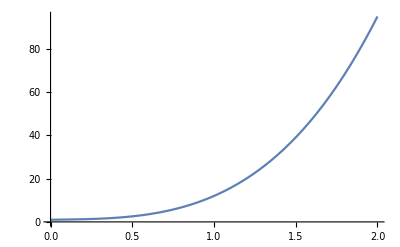

```mathematica
Plot[a^4 +10a^3-a^2+a+1,{a,0,2}]
```

```mathematica
Try
```

Try

#### Check if both ϕ solutions can be used to solve 0th order DeWolfe EOMs

If they can solve the EOM algebraically, we’re good! and we just need to worry about the junction conditions, otherwise we might need to think harder

```mathematica
Aprimeeqnsmallμ0
VBsol=Solve[(%/.A'[η]->-1/l+(ϵ κ)/(6 l) ϕ0[η]^2)==0,V[ϕ0[η]]][[1]]//Simplify
```

1/6 κ V[ϕ0[η]]+A'[η]^2-1/12 κ ϕ0'[η]^2

{V[ϕ0[η]]→-(36-12 ϵ κ ϕ0[η]^2+ϵ^2 κ^2 ϕ0[η]^4-3 l^2 κ ϕ0'[η]^2)/(6 l^2 κ)}

So immediately we see, that we only get the same GW potential if we have ϕ0’ =- ϵ/l ϕ0

 this could still work provided we define the mass now in terms of this, and introduce a new epsilon such that ϵ’(ϵ’+4) = ϵ+4 or something, the issue would be that now, ϵ is not necessarily small, but is instead 2 k where k is the AdS curvature, or we can make ϵ negative and close to 4
 
 lets now check the scalar eom, I want to solve for V using the above solution, then plug into the ϕ EOM

```mathematica
Aprimeeqnsmallμ0
Solve[(%)==0,V[ϕ0[η]]][[1]]
V[ϕ0[η]]/.%/.η->ϕ0[η]
D[%,ϕ0[η]]
ϕeqnηsmallμ0/.V'[ϕ0[η]]->%/.λ'[ϕ0[η]]->0//Simplify
```

1/6 κ V[ϕ0[η]]+A'[η]^2-1/12 κ ϕ0'[η]^2

{V[ϕ0[η]]→(-12 A'[η]^2+κ ϕ0'[η]^2)/(2 κ)}

(-12 A'[ϕ0[η]]^2+κ ϕ0'[ϕ0[η]]^2)/(2 κ)

(-24 A'[ϕ0[η]] A''[ϕ0[η]]+2 κ ϕ0'[ϕ0[η]] ϕ0''[ϕ0[η]])/(2 κ)

-4 A'[η] ϕ0'[η]-(12 A'[ϕ0[η]] A''[ϕ0[η]])/κ-ϕ0''[η]+ϕ0'[ϕ0[η]] ϕ0''[ϕ0[η]]

I think this is hopeless, I don’t see how we can extract a new solution without directly applying the superpotential method. 

So either we need to abandon our solutions above and the superpotential method, or else we need to come up with a superpotential that yields both GW solutions

So we want to solve

```mathematica
W[ϕ]=ct ϕ^2 
D[at E^((-ϵ η)/l)+bt E^((4+ϵ)η/l),η]==1/2 D[W[ϕ],ϕ]/.ϕ->at E^((-ϵ η)/l)+bt E^((4+ϵ)η/l)
Solve[%,ct]
%/.bt->0
%%/.at->0
```

ct ϕ^2

-(at ⅇ^(-(ϵ η)/l) ϵ)/l+(bt ⅇ^(((4+ϵ) η)/l) (4+ϵ))/l==ct (at ⅇ^(-(ϵ η)/l)+bt ⅇ^(((4+ϵ) η)/l))

{{ct→(4 bt ⅇ^((ϵ η)/l+((4+ϵ) η)/l)-at ϵ+bt ⅇ^((ϵ η)/l+((4+ϵ) η)/l) ϵ)/((at+bt ⅇ^((ϵ η)/l+((4+ϵ) η)/l)) l)}}

{{ct→-ϵ/l}}

{{ct→(ⅇ^(-(ϵ η)/l-((4+ϵ) η)/l) (4 bt ⅇ^((ϵ η)/l+((4+ϵ) η)/l)+bt ⅇ^((ϵ η)/l+((4+ϵ) η)/l) ϵ))/(bt l)}}

If you tune to ϵ = -2 this could be independent of η, otherwise no.

We could try allowing ourselves find different solutions for ϕ, I think then the key would  be to understand what features we need to get a stable GW potential, eg. the following definitely won’t work since its flat

```mathematica
DSolve[ϕ'[η]==ϕ[η]^2-ct,ϕ[η],η]
```

DSolve::dsfun: ϕ0[η]+ⅇ^((4 η)/l) μ ϕ1[η] cannot be used as a function.

DSolve[ϕ'[η]==-ct+(ϕ0[η]+ⅇ^((4 η)/l) μ ϕ1[η])^2,ϕ0[η]+ⅇ^((4 η)/l) μ ϕ1[η],η]

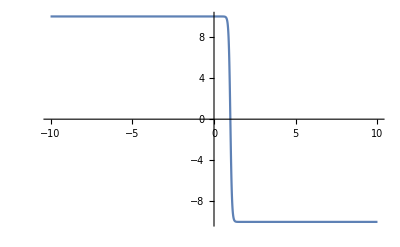

```mathematica
Plot[-10 Tanh[10(η-1)],{η,-10,10}]
```

## Scrap

#### Compute GW potential

```mathematica
Print["The original GW potential is computed as"]
Gsqrtdet=rc E^(-4 k rc ϕ)
Gupupϕϕ=- rc^-2
Φ = A E^((2 + ν) k rc ϕ)+ B E^((2 -ν) k rc ϕ)
-Gsqrtdet (Gupupϕϕ D[Φ,ϕ]^2 - m^2 Φ^2)/.m ->k √(ν^2-4)//Simplify
Integrate[%,{ϕ,0,π}]//Simplify
%/.A->0//Simplify
%%/.B->0
Print["This agrees with eqn (8) of the original GW proposal"]
```

The original GW potential is computed as

ⅇ^(-4 k rc ϕ) rc

-1/rc^2

B ⅇ^(k rc (2-ν) ϕ)+A ⅇ^(k rc (2+ν) ϕ)

2 ⅇ^(-2 k rc ν ϕ) k^2 rc ν (B^2 (-2+ν)+A^2 ⅇ^(4 k rc ν ϕ) (2+ν))

ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (B^2 (-2+ν)+A^2 ⅇ^(2 k π rc ν) (2+ν))

B^2 ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (-2+ν)

A^2 (-1+ⅇ^(2 k π rc ν)) k (2+ν)

This agrees with eqn (8) of the original GW proposal

```mathematica
D[E^(-4 k rc π)(vv - vh E^(-ϵ k rc π))^2,rc]//Simplify
Solve[%==0,rc] //Simplify
%/.ϵ->m^2/(4 k^2)
```

-2 ⅇ^(-2 k π rc (2+ϵ)) k π (vh-ⅇ^(k π rc ϵ) vv) (-2 ⅇ^(k π rc ϵ) vv+vh (2+ϵ))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rc→Log[vh/vv]/(k π ϵ)},{rc→Log[(vh (2+ϵ))/(2 vv)]/(k π ϵ)}}

{{rc→(4 k Log[vh/vv])/(m^2 π)},{rc→(4 k Log[((2+m^2/(4 k^2)) vh)/(2 vv)])/(m^2 π)}}

```mathematica
Print["ϕ stuff"]
ϕ0sol
ϕmsol = ϕIR E^(- ϵm (η-ηIR)/l)
ϕ0sol/.ϵ->ϵm/.C[0]->ϕIR E^(ϵm ηIR/l)//Simplify
ϕpsol=ϕUV E^(-ϵp η/l)
Print["metric stuff"]
detgηsmallμ0
Aofηsol/.C[2]->0/.C[1]->C[0]
Series[gη,{μ,0,0}]//Normal
Print["The effective action for the scalar away from the branes is"]
Leff = -√detgηsmallμ0(%%[[5,5]] D[ϕ0[η]/.ϕ0sol,η]^2-1/2(ϵ(ϵ+4))/l^2 (ϕ0[η]/.ϕ0sol)^2)/.Aofηsol/.C[2]->0/.C[1]->C[0]//Simplify//PowerExpand
Print["In the limit of no back reaction, this gives the 4D effective action as"]
Integrate[Leff/.M->∞,η]
Plusregioncont=(%/.η->ηIR/.ϵ->ϵp/.C[0]->ϕUV/.ϵ->ϵp)-(%/.η->0/.C[0]->ϕUV/.ϵ->ϵp)//Simplify
Minusregioncont=-(%%/.η->ηIR/.C[0]->ϕIR E^(ϵm ηIR/l))/.ϵ->ϵm//Simplify
Print["This gives the effective potential"]
Plusregioncont+Minusregioncont
D[Plusregioncont+Minusregioncont,ηIR]//Simplify
(*Solve[%==0,ηIR]
ηIR/l/.%/.ϵp->ν ϵm/.ϵm->0.05
Plot[%,{ν,0,1}]*)
```

ϕ stuff

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR

ϕ0[η]→ⅇ^((ϵm (-η+ηIR))/l) ϕIR

ⅇ^(-(ϵp η)/l) ϕUV

metric stuff

ⅇ^(8 A[η])

A[η]→-η/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(48 M^3)

{{ⅇ^(2 A[η]),0,0,0,0},{0,-ⅇ^(2 A[η]),0,0,0},{0,0,-ⅇ^(2 A[η]),0,0},{0,0,0,-ⅇ^(2 A[η]),0},{0,0,0,0,-1}}

The effective action for the scalar away from the branes is

(ⅇ^(-(2 ϵ η)/l+1/2 (-(8 η)/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(6 M^3))) ϵ (4+3 ϵ) C[0]^2)/(2 l^2)

In the limit of no back reaction, this gives the 4D effective action as

-(ⅇ^(-(2 (2+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2)/(4 l (2+ϵ))

(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))

This gives the effective potential

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-2 ⅇ^((2 ϵp ηIR)/l) ϵm (4+3 ϵm) ϕIR^2+(2+ϵm) ϵp (4+3 ϵp) ϕUV^2))/(2 l^2 (2+ϵm))

```mathematica
Print["Work at first order in the back reaction for the effective action"]
(*Integrate[Leff/E^(-2ϵ η/l)/.C[0]->M^(3/2) ξϕ,η]
Series[%,{ξϕ,0,4}]//Normal//Simplify*)
Series[Leff,{M,∞,3}]//Normal//Simplify
Integrate[%,η]//FullSimplify
```

Work at first order in the back reaction for the effective action

-(ⅇ^(-(4 (1+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2 (-12 ⅇ^((2 ϵ η)/l) M^3+C[0]^2))/(24 l^2 M^3)

-(ⅇ^(-(4 (1+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2 ((6 ⅇ^((2 ϵ η)/l) l M^3)/(2+ϵ)-(l C[0]^2)/(4 (1+ϵ))))/(24 l^2 M^3)

Expand the GW potential and get in the form of CR

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(rConf ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+((-1+1/rGW) rGW ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(rConf ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))-(((-1+rGW) ϕUV^2) ϵp)/(2 l)+O[ϵp]^2

((rConf ϕIR^2 ϵm)/(2 l)+O[ϵm]^2)-(((-1+rGW) ϕUV^2) ϵp)/(2 l)+O[ϵp]^2

(rConf ϵm ϕIR^2)/(2 l)-((-1+rGW) ϵp ϕUV^2)/(2 l)

(r^4 ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)

This is qualitatively similar to the GW potential. There is however a small difference compared to the braced expression eqn (29)

(4 r^3 ϵm ϕIR^2-r^(3+2 ϵp) ϵp (4+2 ϵp) ϕUV^2)/(2 l)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{r→2^(1/2/ϵp) ((ϵp (2+ϵp) ϕUV^2)/(ϵm ϕIR^2))^(-1/2/ϵp)}

{r→7.83526×10^-6}

(r^4 (-ϵm ϕIR^2+r^(2 ϵp) ϵp ϕUV^2))/(2 l)

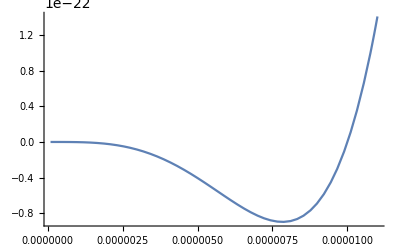

(ⅇ^(-(4 ηIR)/l) (-ϵm ϕIR^2+(ⅇ^(-ηIR/l))^(2 ϵp) ϵp ϕUV^2))/(2 l)

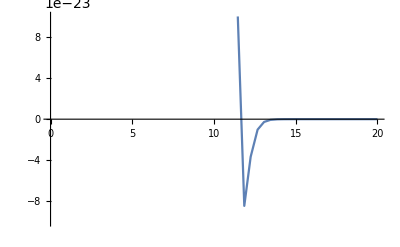

```mathematica
Print["Expand the GW potential and get in the form of CR"]
Plusregioncont+Minusregioncont
%/.ηIR ->- l Log[r ]/.r^4->rConf/.r^(2(2+ϵp))->rGW/.r^(-2(2+ϵp))->rGW^-1
Series[%,{ϵp,0,1}]
Series[%,{ϵm,0,1}]//Simplify
%//Normal
VGWexpanded=%/.rConf->r^4/.rGW->r^(2(2+ϵp))/.rGW^-1->r^(-2(2+ϵp))//Simplify
Print["This is qualitatively similar to the GW potential. There is however a small difference compared to the braced expression eqn (29)"]
D[VGWexpanded,r]
VGWexpMin=Solve[%==0,r][[1]]//Simplify
(*%//PowerExpand//Simplify
Series[r/.%,{ϵp,0,1}]//Normal//Simplify//PowerExpand*)
(*VGWexpMin/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->1/.l->1
Plot[VGWexpanded/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->1/.l->1,{r,0,1}]*)
VGWexpMin/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1
-(VGWexpanded - CoefficientList[VGWexpanded,r][[1]])//Simplify
Plot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{r,10^-7,1.1 10^-5}]
-(VGWexpanded- CoefficientList[VGWexpanded,r][[1]] )/.r->E^(-ηIR/l)//Simplify
Plot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{ηIR,0,20},PlotRange->{-10^-22,10^-22}]
```

```mathematica
Solve[D[E^(-4 ηIR/l)(ϵp ϕIR^2-ϵp E^(-2 ϵp ηIR/l)ϕUV^2),ηIR]==0,ηIR]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ηIR→(l Log[((2+ϵp) ϕUV^2)/(2 ϕIR^2)])/(2 ϵp)}}

Now expand to leading order in ϵ_i without taking the exponential to be small

(ⅇ^(-(4 ηIR)/l) ϵm ϕIR^2+ϵp ϕUV^2-ⅇ^(-(2 (2+ϵp) ηIR)/l) ϵp ϕUV^2)/(2 l)

(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-2 ⅇ^((2 ϵp ηIR)/l) ϵm ϕIR^2+ϵp (2+ϵp) ϕUV^2))/l^2

-(ⅇ^(-(2 (2+ϵp) ηIR)/l) (2 ⅇ^((2 ϵp ηIR)/l) ϵm ϕIR^2-2 ϵp ϕUV^2))/l^2

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{ηIR→(l Log[(ϵp ϕUV^2)/(ϵm ϕIR^2)])/(2 ϵp)}

{ηIR→(l Log[10])/(2 ϵp)}

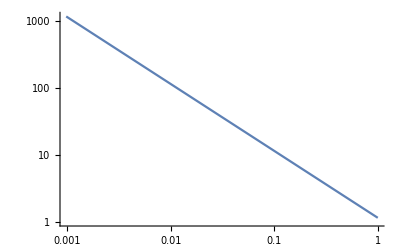

5.-5. ⅇ^(-4.2 ηIR)+0.5 ⅇ^(-4. ηIR)

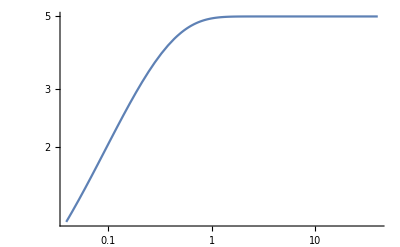

```mathematica
Print["Now expand to leading order in ϵ_i without taking the exponential to be small"]
VGW=-(-(ⅇ^(-(4 ηIR)/l) ϵm (4) ϕIR^2)/(4 l (2))-(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4) ϕUV^2)/(4 l (2)))//Simplify
D[%,ηIR]//Simplify
-(ⅇ^(-(2 (2+ϵp) ηIR)/l) (2 ⅇ^((2 ϵp ηIR)/l) ϵm ϕIR^2-ϵp (2) ϕUV^2))/l^2
Solve[%==0,ηIR][[1]]//Simplify
%/.ϕUV->10ϕIR/.ϵm->10ϵp
LogLogPlot[ηIR/l/.%,{ϵp,0,1}]
VGW/ϕIR^2/.ϕUV->10ϕIR/.ϵm->10ϵp/.ϵp->0.1/.l->1//Simplify
LogLogPlot[Abs[%],{ηIR,0,40},PlotRange->All]
```

#### Compute GW potential - 0th order in ξ

```mathematica
Print["The original GW potential is computed as"]
Gsqrtdet=rc E^(-4 k rc ϕ)
Gupupϕϕ=- rc^-2
Φ = A E^((2 + ν) k rc ϕ)+ B E^((2 -ν) k rc ϕ)
-Gsqrtdet (Gupupϕϕ D[Φ,ϕ]^2 - m^2 Φ^2)/.m ->k √(ν^2-4)//Simplify
Integrate[%,{ϕ,0,π}]//Simplify
%/.A->0//Simplify
%%/.B->0
Print["This agrees with eqn (8) of the original GW proposal"]
```

The original GW potential is computed as

ⅇ^(-4 k rc ϕ) rc

-1/rc^2

B ⅇ^(k rc (2-ν) ϕ)+A ⅇ^(k rc (2+ν) ϕ)

2 ⅇ^(-2 k rc ν ϕ) k^2 rc ν (B^2 (-2+ν)+A^2 ⅇ^(4 k rc ν ϕ) (2+ν))

ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (B^2 (-2+ν)+A^2 ⅇ^(2 k π rc ν) (2+ν))

B^2 ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (-2+ν)

A^2 (-1+ⅇ^(2 k π rc ν)) k (2+ν)

This agrees with eqn (8) of the original GW proposal

```mathematica
D[E^(-4 k rc π)(vv - vh E^(-ϵ k rc π))^2,rc]//Simplify
Solve[%==0,rc] //Simplify
%/.ϵ->m^2/(4 k^2)
```

-2 ⅇ^(-2 k π rc (2+ϵ)) k π (vh-ⅇ^(k π rc ϵ) vv) (-2 ⅇ^(k π rc ϵ) vv+vh (2+ϵ))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rc→Log[vh/vv]/(k π ϵ)},{rc→Log[(vh (2+ϵ))/(2 vv)]/(k π ϵ)}}

{{rc→(4 k Log[vh/vv])/(m^2 π)},{rc→(4 k Log[((2+m^2/(4 k^2)) vh)/(2 vv)])/(m^2 π)}}

```mathematica
gη
Series[gη,{μ,0,2}]-Series[gη,{μ,0,0}]
```

{{ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ c[η]) (1-3/4 ⅇ^((4 η)/l) μ),0,0,0,0},{0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0,0},{0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0},{0,0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0},{0,0,0,0,-1}}

{{O[μ]^1,0,0,0,0},{0,O[μ]^1,0,0,0},{0,0,O[μ]^1,0,0},{0,0,0,O[μ]^1,0},{0,0,0,0,0}}

```mathematica
Print["ϕ stuff"]
ϕ0sol
ϕmsol = ϕIR E^(- ϵm (η-ηIR)/l)
ϕ0sol/.ϵ->ϵm/.C[0]->ϕIR E^(ϵm ηIR/l)//Simplify
ϕpsol=ϕUV E^(-ϵp η/l)
Print["metric stuff"]
detgηsmallμ0
Aofηsol/.C[2]->0/.C[1]->C[0]
(*Series[gη,{μ,0,1}]-Series[gη,{μ,0,0}]//Normal*)
Series[gη,{μ,0,0}]//Normal
Print["The effective action for the scalar away from the branes is"]
Leff = √detgηsmallμ0(%%[[5,5]] D[ϕ0[η]/.ϕ0sol,η]^2-1/2(ϵ(ϵ+4))/l^2 (ϕ0[η]/.ϕ0sol)^2)/.Aofηsol/.C[2]->0/.C[1]->C[0]//Simplify//PowerExpand
Print["In the limit of no back reaction, this gives the 4D effective potential as"]
-Integrate[Leff/.M->∞,η]
Plusregioncont=(%/.η->ηIR/.ϵ->ϵp/.C[0]->ϕUV/.ϵ->ϵp)-(%/.η->0/.C[0]->ϕUV/.ϵ->ϵp)//Simplify
Minusregioncont=-(%%/.η->ηIR/.C[0]->ϕIR E^(ϵm ηIR/l))/.ϵ->ϵm//Simplify
Print["This gives the effective potential"]
Plusregioncont+Minusregioncont
(*D[Plusregioncont+Minusregioncont,ηIR]//Simplify*)
(*Solve[%==0,ηIR]
ηIR/l/.%/.ϵp->ν ϵm/.ϵm->0.05
Plot[%,{ν,0,1}]*)
```

ϕ stuff

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR

ϕ0[η]→ⅇ^((ϵm (-η+ηIR))/l) ϕIR

ⅇ^(-(ϵp η)/l) ϕUV

metric stuff

ⅇ^(8 A[η])

A[η]→-η/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(48 M^3)

{{ⅇ^(2 A[η]),0,0,0,0},{0,-ⅇ^(2 A[η]),0,0,0},{0,0,-ⅇ^(2 A[η]),0,0},{0,0,0,-ⅇ^(2 A[η]),0},{0,0,0,0,-1}}

The effective action for the scalar away from the branes is

-(ⅇ^(-(2 ϵ η)/l+1/2 (-(8 η)/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(6 M^3))) ϵ (4+3 ϵ) C[0]^2)/(2 l^2)

In the limit of no back reaction, this gives the 4D effective potential as

-(ⅇ^(-(2 (2+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2)/(4 l (2+ϵ))

(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))

This gives the effective potential

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

```mathematica
Print["Work at first order in the back reaction for the effective action"]
(*Integrate[Leff/E^(-2ϵ η/l)/.C[0]->M^(3/2) ξϕ,η]
Series[%,{ξϕ,0,4}]//Normal//Simplify*)
Series[Leff,{M,∞,3}]//Normal//Simplify
Integrate[%,η]//FullSimplify
```

Work at first order in the back reaction for the effective action

(ⅇ^(-(4 (1+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2 (-12 ⅇ^((2 ϵ η)/l) M^3+C[0]^2))/(24 l^2 M^3)

(ⅇ^(-(4 (1+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2 ((6 ⅇ^((2 ϵ η)/l) l M^3)/(2+ϵ)-(l C[0]^2)/(4 (1+ϵ))))/(24 l^2 M^3)

```mathematica
Print["Expand the GW potential and get in the form of CR and include the boundary term"]
Vboundary= -1/2(ϵm-ϵp)/l E^(-4 ηIR/l) ϕIR^2+ϵp/l ϕUV^2
Plusregioncont+Minusregioncont + Vboundary
%/.ηIR ->- l Log[r ]/.r^4->rConf/.r^(2(2+ϵp))->rGW/.r^(-2(2+ϵp))->rGW^-1
Series[%,{ϵp,0,1}]
Series[%,{ϵm,0,1}]//Simplify
%//Normal 
VGWexpanded=%/.rConf->r^4/.rGW->r^(2(2+ϵp))/.rGW^-1->r^(-2(2+ϵp))//Simplify
```

Expand the GW potential and get in the form of CR and include the boundary term

-(ⅇ^(-(4 ηIR)/l) (ϵm-ϵp) ϕIR^2)/(2 l)+(ϵp ϕUV^2)/l

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))-(ⅇ^(-(4 ηIR)/l) (ϵm-ϵp) ϕIR^2)/(2 l)+(ϵp ϕUV^2)/l+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(rConf ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))-(rConf (ϵm-ϵp) ϕIR^2)/(2 l)+(ϵp ϕUV^2)/l+((-1+1/rGW) rGW ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(rConf ϵm^2 ϕIR^2)/(4 l (2+ϵm))+((rConf ϕIR^2+3 ϕUV^2-rGW ϕUV^2) ϵp)/(2 l)+O[ϵp]^2

O[ϵm]^2+((rConf ϕIR^2-(-3+rGW) ϕUV^2) ϵp)/(2 l)+O[ϵp]^2

(ϵp (rConf ϕIR^2-(-3+rGW) ϕUV^2))/(2 l)

(ϵp (r^4 ϕIR^2-(-3+r^(4+2 ϵp)) ϕUV^2))/(2 l)

This is qualitatively similar to the GW potential. There is however a small difference compared to the braced expression eqn (29)

(ϵp (4 r^3 ϕIR^2-r^(3+2 ϵp) (4+2 ϵp) ϕUV^2))/(2 l)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{r→2^(1/2/ϵp) (((2+ϵp) ϕUV^2)/ϕIR^2)^(-1/2/ϵp)}

rmin is:

7.83526×10^-11

(r^4 ϵp (ϕIR^2-r^(2 ϵp) ϕUV^2))/(2 l)

0.05 (1-100 r^0.2) r^4

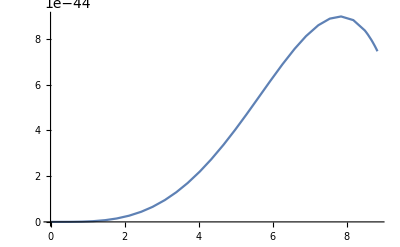

(ⅇ^(-(4 ηIR)/l) ϵp (ϕIR^2-(ⅇ^(-ηIR/l))^(2 ϵp) ϕUV^2))/(2 l)

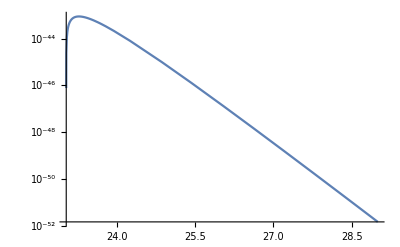

(ⅇ^(-4/(kIR l)) ϵp (ϕIR^2-(ⅇ^(-1/(kIR l)))^(2 ϵp) ϕUV^2))/(2 l)

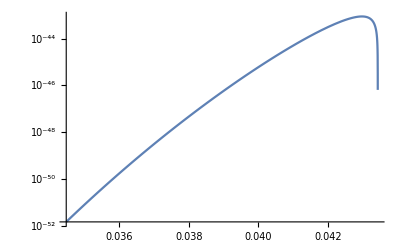

```mathematica
Print["This is qualitatively similar to the GW potential. There is however a small difference compared to the braced expression eqn (29)"]
D[VGWexpanded,r]
VGWexpMin=Solve[%==0,r][[1]]//Simplify
Print["rmin is: "]
rmin=r/.VGWexpMin/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1
(*%//PowerExpand//Simplify
Series[r/.%,{ϵp,0,1}]//Normal//Simplify//PowerExpand*)
(*VGWexpMin/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->1/.l->1
Plot[VGWexpanded/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->1/.l->1,{r,0,1}]*)


(VGWexpanded- CoefficientList[VGWexpanded,r][[1]] )//Simplify
%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1
Plot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{r,10^-11 -rmin,rmin+ 10^-11},PlotRange->All]

(VGWexpanded- CoefficientList[VGWexpanded,r][[1]] )/.r->E^(-ηIR/l)//Simplify
LogPlot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{ηIR,0,29},PlotRange->All]

(VGWexpanded- CoefficientList[VGWexpanded,r][[1]] )/.r->E^(-ηIR/l)/.ηIR->1/kIR//Simplify
LogPlot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{kIR,1/29,1/23},PlotRange->All]
```

```mathematica
(VGWexpanded-Vboundary/.ηIR->-l Log[r])
CoefficientList[%,r][[1]]//Simplify
```

(r^4 (ϵm-ϵp) ϕIR^2)/(2 l)-(ϵp ϕUV^2)/l+(ϵp (r^4 ϕIR^2-(-3+r^(4+2 ϵp)) ϕUV^2))/(2 l)

(ϵp ϕUV^2)/(2 l)

{ϵp→0.01,ϵm→0.1,ϕIR→1,ϕUV→10,l→1}

(r^4 (ϵm ϕIR^2-r^(2 ϵp) ϵp ϕUV^2))/(2 l)

1/2 (0.1-1. r^0.02) r^4

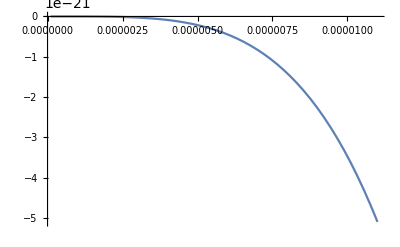

(ⅇ^(-(4 ηIR)/l) (ϵm ϕIR^2-(ⅇ^(-ηIR/l))^(2 ϵp) ϵp ϕUV^2))/(2 l)

1/2 ⅇ^(-4 ηIR) (0.1-1. (ⅇ^-ηIR)^0.02)

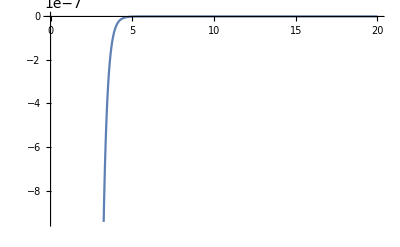

```mathematica
repl = {ϵp->0.01 ,ϵm->0.1,ϕIR->1,ϕUV->10,l->1}
(VGWexpanded -Vboundary- CoefficientList[VGWexpanded-Vboundary/.ηIR->-l Log[r],r][[1]])/.ηIR->-l Log[r]//Simplify
(*Plot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{r,10^-7,1.1 10^-5}]*)
%/.repl
Plot[%/.repl,{r,10^-7,1.1 10^-5}]
(*used before adding in boundary potential*)
(VGWexpanded-Vboundary- CoefficientList[VGWexpanded-Vboundary/.ηIR->-l Log[r],r][[1]] )/.r->E^(-ηIR/l)//Simplify
%/.repl
Plot[%/.repl,{ηIR,0,20}](*used before adding in boundary potential*)
```

Find the stability of the effective potential

```mathematica
Solve[D[(VGWexpanded-Vboundary- CoefficientList[VGWexpanded-Vboundary/.ηIR->-l Log[r],r][[1]] )/.r->E^(-ηIR/l)//Simplify,{ηIR,1}]==0,ηIR][[2]]
D[(VGWexpanded-Vboundary- CoefficientList[VGWexpanded-Vboundary/.ηIR->-l Log[r],r][[1]] )/.r->E^(-ηIR/l)//Simplify,{ηIR,2}]/.%//Simplify//PowerExpand//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{ηIR→(l Log[(√ϵp √(2+ϵp) ϕUV)/(√2 √ϵm ϕIR)])/ϵp}

-(4^(1+1/ϵp) ϵm^((2+ϵp)/ϵp) ϵp^((-2+ϵp)/ϵp) (2+ϵp)^(-2/ϵp) ϕIR^(2+4/ϵp) ϕUV^(-4/ϵp))/l^3

```mathematica
VGWexpanded
D[VGWexpanded/.r->E^(-ηIR/l)//Simplify,{ηIR,1}]
Solve[%==0,ηIR][[2]]
D[VGWexpanded/.r->E^(-ηIR/l),{ηIR,2}]/.%//Simplify//PowerExpand//Simplify
```

(ϵp (r^4 ϕIR^2-(-3+r^(4+2 ϵp)) ϕUV^2))/(2 l)

(ϵp (-(4 ⅇ^(-(4 ηIR)/l) ϕIR^2)/l+(2 (ⅇ^(-ηIR/l))^(2 (2+ϵp)) (2+ϵp) ϕUV^2)/l))/(2 l)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{ηIR→(l Log[(√(2+ϵp) ϕUV)/(√2 ϕIR)])/ϵp}

-(4^(1+1/ϵp) ϵp^2 (2+ϵp)^(-2/ϵp) ϕIR^(2+4/ϵp) ϕUV^(-4/ϵp))/l^3

```mathematica
N@(1/29)
```

0.0344828

```mathematica
Print["Get the stability of the extremum found above"]
ηmin=Series[η/.Solve[D[VGWexpanded/.r->E^(-η/l),{η,1}]==0,η][[2]],{ϵp,0,-1}]//Normal
D[VGWexpanded/.r->E^(-η/l),{η,2}]/.η->ηmin//Simplify//PowerExpand//Simplify
VGWexpanded/.r->E^(-η/l)/.η->ηmin//Simplify//PowerExpand//Simplify
```

Get the stability of the extremum found above

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(l Log[ϕUV/ϕIR])/ϵp

-(2 ϵp^2 (4+ϵp) ϕIR^(2+4/ϵp) ϕUV^(-4/ϵp))/l^3

(3 ϵp ϕUV^2)/(2 l)

```mathematica
Print["Try the same with a mass scale instead of η scale"]
D[VGWexpanded/.r->E^(-η/l)/.η->1/k,{k,2}]/.k->ηmin^-1//Simplify//PowerExpand//FullSimplify
%/.ϕIR->3/.ϕUV->1/.ϵp->0.1
VGWexpanded/.r->E^(-η/l)/.η->1/k/.k->ηmin^-1//Simplify//PowerExpand//Simplify
Print["Conclusion is unchanged, just have the right dimensions."]
```

Try the same with a mass scale instead of η scale

-(2 l ϕIR^(2+4/ϵp) ϕUV^(-4/ϵp) (Log[ϕIR]-Log[ϕUV])^3 (ϵp+(4+ϵp) Log[ϕIR]-(4+ϵp) Log[ϕUV]))/ϵp^2

-1.33604×10^23 l

(3 ϵp ϕUV^2)/(2 l)

Conclusion is unchanged, just have the right dimensions.

```mathematica
Integrate[D[-l Log[r],r]Leff/.M->∞/.η->-l Log[r]//Simplify,{r,0,rIR}]
```

ConditionalExpression[(rIR^(4+2 ϵ) ϵ (4+3 ϵ) C[0]^2)/(4 l (2+ϵ)), Re[ϵ]>-2]

```mathematica
Clear[ϕ]
DSolve[ϕ''[η]-4/l ϕ'[η]==ϵ (ϵ + 4)/l^2 ϕ[η],ϕ[η],η ]
```

{{ϕ[η]→ⅇ^(-(ϵ η)/l) C[1]+ⅇ^(((4+ϵ) η)/l) C[2]}}

#### Compute GW potential - 0th order in ξ

```mathematica
Print["The original GW potential is computed as"]
Gsqrtdet=rc E^(-4 k rc ϕ)
Gupupϕϕ=- rc^-2
Φ = A E^((2 + ν) k rc ϕ)+ B E^((2 -ν) k rc ϕ)
-Gsqrtdet (Gupupϕϕ D[Φ,ϕ]^2 - m^2 Φ^2)/.m ->k √(ν^2-4)//Simplify
Integrate[%,{ϕ,0,π}]//Simplify
%/.A->0//Simplify
%%/.B->0
Print["This agrees with eqn (8) of the original GW proposal"]
```

The original GW potential is computed as

ⅇ^(-4 k rc ϕ) rc

-1/rc^2

B ⅇ^(k rc (2-ν) ϕ)+A ⅇ^(k rc (2+ν) ϕ)

2 ⅇ^(-2 k rc ν ϕ) k^2 rc ν (B^2 (-2+ν)+A^2 ⅇ^(4 k rc ν ϕ) (2+ν))

ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (B^2 (-2+ν)+A^2 ⅇ^(2 k π rc ν) (2+ν))

B^2 ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (-2+ν)

A^2 (-1+ⅇ^(2 k π rc ν)) k (2+ν)

This agrees with eqn (8) of the original GW proposal

```mathematica
D[E^(-4 k rc π)(vv - vh E^(-ϵ k rc π))^2,rc]//Simplify
Solve[%==0,rc] //Simplify
%/.ϵ->m^2/(4 k^2)
```

-2 ⅇ^(-2 k π rc (2+ϵ)) k π (vh-ⅇ^(k π rc ϵ) vv) (-2 ⅇ^(k π rc ϵ) vv+vh (2+ϵ))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rc→Log[vh/vv]/(k π ϵ)},{rc→Log[(vh (2+ϵ))/(2 vv)]/(k π ϵ)}}

{{rc→(4 k Log[vh/vv])/(m^2 π)},{rc→(4 k Log[((2+m^2/(4 k^2)) vh)/(2 vv)])/(m^2 π)}}

```mathematica
gη
Series[gη,{μ,0,2}]-Series[gη,{μ,0,0}]
```

{{ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ c[η]) (1-3/4 ⅇ^((4 η)/l) μ),0,0,0,0},{0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0,0},{0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0},{0,0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0},{0,0,0,0,-1}}

{{O[μ]^1,0,0,0,0},{0,O[μ]^1,0,0,0},{0,0,O[μ]^1,0,0},{0,0,0,O[μ]^1,0},{0,0,0,0,0}}

```mathematica
A[η]
```

A[η]

```mathematica
gη
```

{{ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ c[η]) (1-3/4 ⅇ^((4 η)/l) μ),0,0,0,0},{0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0,0},{0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0},{0,0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0},{0,0,0,0,-1}}

```mathematica
gη/.A[η]->0/.μ->0
```

{{1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}}

```mathematica
Print["ϕ stuff"]
ϕ0sol
ϕmsol = ϕIR E^(- ϵm (η-ηIR)/l)
ϕ0sol/.ϵ->ϵm/.C[0]->ϕIR E^(ϵm ηIR/l)//Simplify
ϕpsol=ϕUV E^(-ϵp η/l)
Print["metric stuff"]
detgηsmallμ0
Aofηsol/.C[2]->0/.C[1]->C[0]
(*Series[gη,{μ,0,1}]-Series[gη,{μ,0,0}]//Normal*)
Series[gη,{μ,0,1}]//Normal
Print["The effective action for the scalar away from the branes is"]
Leff = √detgηsmallμ0(%%[[5,5]] D[ϕ0[η]/.ϕ0sol,η]^2-1/2(ϵ(ϵ+4))/l^2 (ϕ0[η]/.ϕ0sol)^2)/.Aofηsol/.C[2]->0/.C[1]->C[0]//Simplify//PowerExpand
Print["In the limit of no back reaction, this gives the 4D effective potential as"]
-Integrate[Leff/.M->∞,η]
Plusregioncont=(%/.η->ηIR/.ϵ->ϵp/.C[0]->ϕUV/.ϵ->ϵp)-(%/.η->0/.C[0]->ϕUV/.ϵ->ϵp)//Simplify
Minusregioncont=-(%%/.η->ηIR/.C[0]->ϕIR E^(ϵm ηIR/l))/.ϵ->ϵm//Simplify
Print["This gives the effective potential"]
Plusregioncont+Minusregioncont
(*D[Plusregioncont+Minusregioncont,ηIR]//Simplify*)
(*Solve[%==0,ηIR]
ηIR/l/.%/.ϵp->ν ϵm/.ϵm->0.05
Plot[%,{ν,0,1}]*)
```

ϕ stuff

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR

ϕ0[η]→ⅇ^((ϵm (-η+ηIR))/l) ϕIR

ⅇ^(-(ϵp η)/l) ϕUV

metric stuff

ⅇ^(8 A[η])

A[η]→-η/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(48 M^3)

{{ⅇ^(2 A[η])+1/4 ⅇ^((4 η)/l+2 A[η]) μ (-3+8 c[η]),0,0,0,0},{0,-ⅇ^(2 A[η])-1/4 ⅇ^((4 η)/l+2 A[η]) μ (1+8 B[η]),0,0,0},{0,0,-ⅇ^(2 A[η])-1/4 ⅇ^((4 η)/l+2 A[η]) μ (1+8 B[η]),0,0},{0,0,0,-ⅇ^(2 A[η])-1/4 ⅇ^((4 η)/l+2 A[η]) μ (1+8 B[η]),0},{0,0,0,0,-1}}

The effective action for the scalar away from the branes is

-(ⅇ^(-(2 ϵ η)/l+1/2 (-(8 η)/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(6 M^3))) ϵ (4+3 ϵ) C[0]^2)/(2 l^2)

In the limit of no back reaction, this gives the 4D effective potential as

-(ⅇ^(-(2 (2+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2)/(4 l (2+ϵ))

(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))

This gives the effective potential

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

```mathematica
Print["Work at first order in the back reaction for the effective action"]
(*Integrate[Leff/E^(-2ϵ η/l)/.C[0]->M^(3/2) ξϕ,η]
Series[%,{ξϕ,0,4}]//Normal//Simplify*)
Series[Leff,{M,∞,3}]//Normal//Simplify
Integrate[%,η]//FullSimplify
```

Work at first order in the back reaction for the effective action

(ⅇ^(-(4 (1+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2 (-12 ⅇ^((2 ϵ η)/l) M^3+C[0]^2))/(24 l^2 M^3)

(ⅇ^(-(4 (1+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2 ((6 ⅇ^((2 ϵ η)/l) l M^3)/(2+ϵ)-(l C[0]^2)/(4 (1+ϵ))))/(24 l^2 M^3)

```mathematica
Print["Expand the GW potential and get in the form of CR and include the boundary term"]
Vboundary= -1/2(ϵm-ϵp)/l E^(-4 ηIR/l) ϕIR^2+ϵp/l ϕUV^2
Plusregioncont+Minusregioncont + Vboundary
%/.ηIR ->- l Log[r ]/.r^4->rConf/.r^(2(2+ϵp))->rGW/.r^(-2(2+ϵp))->rGW^-1
Series[%,{ϵp,0,1}]
Series[%,{ϵm,0,1}]//Simplify
%//Normal 
VGWexpanded=%/.rConf->r^4/.rGW->r^(2(2+ϵp))/.rGW^-1->r^(-2(2+ϵp))//Simplify
```

Expand the GW potential and get in the form of CR and include the boundary term

-(ⅇ^(-(4 ηIR)/l) (ϵm-ϵp) ϕIR^2)/(2 l)+(ϵp ϕUV^2)/l

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))-(ⅇ^(-(4 ηIR)/l) (ϵm-ϵp) ϕIR^2)/(2 l)+(ϵp ϕUV^2)/l+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(rConf ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))-(rConf (ϵm-ϵp) ϕIR^2)/(2 l)+(ϵp ϕUV^2)/l+((-1+1/rGW) rGW ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(rConf ϵm^2 ϕIR^2)/(4 l (2+ϵm))+((rConf ϕIR^2+3 ϕUV^2-rGW ϕUV^2) ϵp)/(2 l)+O[ϵp]^2

O[ϵm]^2+((rConf ϕIR^2-(-3+rGW) ϕUV^2) ϵp)/(2 l)+O[ϵp]^2

(ϵp (rConf ϕIR^2-(-3+rGW) ϕUV^2))/(2 l)

(ϵp (r^4 ϕIR^2-(-3+r^(4+2 ϵp)) ϕUV^2))/(2 l)

```mathematica
Print["This is qualitatively similar to the GW potential. There is however a small difference compared to the braced expression eqn (29)"]
D[VGWexpanded,r]
VGWexpMin=Solve[%==0,r][[1]]//Simplify
Print["rmin is: "]
rmin=r/.VGWexpMin/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1
(*%//PowerExpand//Simplify
Series[r/.%,{ϵp,0,1}]//Normal//Simplify//PowerExpand*)
(*VGWexpMin/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->1/.l->1
Plot[VGWexpanded/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->1/.l->1,{r,0,1}]*)


(VGWexpanded- CoefficientList[VGWexpanded,r][[1]] )//Simplify
%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1
Plot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{r,10^-11 -rmin,rmin+ 10^-11},PlotRange->All]

(VGWexpanded- CoefficientList[VGWexpanded,r][[1]] )/.r->E^(-ηIR/l)//Simplify
LogPlot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{ηIR,0,29},PlotRange->All]

(VGWexpanded- CoefficientList[VGWexpanded,r][[1]] )/.r->E^(-ηIR/l)/.ηIR->1/kIR//Simplify
LogPlot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{kIR,1/29,1/23},PlotRange->All]
```

This is qualitatively similar to the GW potential. There is however a small difference compared to the braced expression eqn (29)

(ϵp (4 r^3 ϕIR^2-r^(3+2 ϵp) (4+2 ϵp) ϕUV^2))/(2 l)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{r→2^(1/2/ϵp) (((2+ϵp) ϕUV^2)/ϕIR^2)^(-1/2/ϵp)}

rmin is:

7.83526×10^-11

(r^4 ϵp (ϕIR^2-r^(2 ϵp) ϕUV^2))/(2 l)

0.05 (1-100 r^0.2) r^4

-Graphics-

(ⅇ^(-(4 ηIR)/l) ϵp (ϕIR^2-(ⅇ^(-ηIR/l))^(2 ϵp) ϕUV^2))/(2 l)

-Graphics-

(ⅇ^(-4/(kIR l)) ϵp (ϕIR^2-(ⅇ^(-1/(kIR l)))^(2 ϵp) ϕUV^2))/(2 l)

-Graphics-

```mathematica
(VGWexpanded-Vboundary/.ηIR->-l Log[r])
CoefficientList[%,r][[1]]//Simplify
```

(r^4 (ϵm-ϵp) ϕIR^2)/(2 l)-(ϵp ϕUV^2)/l+(ϵp (r^4 ϕIR^2-(-3+r^(4+2 ϵp)) ϕUV^2))/(2 l)

(ϵp ϕUV^2)/(2 l)

```mathematica
repl = {ϵp->0.01 ,ϵm->0.1,ϕIR->1,ϕUV->10,l->1}
(VGWexpanded -Vboundary- CoefficientList[VGWexpanded-Vboundary/.ηIR->-l Log[r],r][[1]])/.ηIR->-l Log[r]//Simplify
(*Plot[%/.ϵp->0.1 ϵm/.ϵm->1/.ϕIR->1/.ϕUV->10/.l->1,{r,10^-7,1.1 10^-5}]*)
%/.repl
Plot[%/.repl,{r,10^-7,1.1 10^-5}]
(*used before adding in boundary potential*)
(VGWexpanded-Vboundary- CoefficientList[VGWexpanded-Vboundary/.ηIR->-l Log[r],r][[1]] )/.r->E^(-ηIR/l)//Simplify
%/.repl
Plot[%/.repl,{ηIR,0,20}](*used before adding in boundary potential*)
```

{ϵp→0.01,ϵm→0.1,ϕIR→1,ϕUV→10,l→1}

(r^4 (ϵm ϕIR^2-r^(2 ϵp) ϵp ϕUV^2))/(2 l)

1/2 (0.1-1. r^0.02) r^4

-Graphics-

(ⅇ^(-(4 ηIR)/l) (ϵm ϕIR^2-(ⅇ^(-ηIR/l))^(2 ϵp) ϵp ϕUV^2))/(2 l)

1/2 ⅇ^(-4 ηIR) (0.1-1. (ⅇ^-ηIR)^0.02)

-Graphics-

```mathematica
Solve[D[(VGWexpanded-Vboundary- CoefficientList[VGWexpanded-Vboundary/.ηIR->-l Log[r],r][[1]] )/.r->E^(-ηIR/l)//Simplify,{ηIR,1}]==0,ηIR][[2]]
D[(VGWexpanded-Vboundary- CoefficientList[VGWexpanded-Vboundary/.ηIR->-l Log[r],r][[1]] )/.r->E^(-ηIR/l)//Simplify,{ηIR,2}]/.%//Simplify//PowerExpand//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{ηIR→(l Log[(√ϵp √(2+ϵp) ϕUV)/(√2 √ϵm ϕIR)])/ϵp}

-(4^(1+1/ϵp) ϵm^((2+ϵp)/ϵp) ϵp^((-2+ϵp)/ϵp) (2+ϵp)^(-2/ϵp) ϕIR^(2+4/ϵp) ϕUV^(-4/ϵp))/l^3

```mathematica
N@(1/29)
```

0.0344828

```mathematica
Print["Get the stability of the extremum found above"]
ηmin=Series[η/.Solve[D[VGWexpanded/.r->E^(-η/l),{η,1}]==0,η][[2]],{ϵp,0,-1}]//Normal
D[VGWexpanded/.r->E^(-η/l),{η,2}]/.η->ηmin//Simplify//PowerExpand//Simplify
VGWexpanded/.r->E^(-η/l)/.η->ηmin//Simplify//PowerExpand//Simplify
```

Get the stability of the extremum found above

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(l Log[ϕUV/ϕIR])/ϵp

-(2 ϵp^2 (4+ϵp) ϕIR^(2+4/ϵp) ϕUV^(-4/ϵp))/l^3

(3 ϵp ϕUV^2)/(2 l)

```mathematica
Print["Try the same with a mass scale instead of η scale"]
D[VGWexpanded/.r->E^(-η/l)/.η->1/k,{k,2}]/.k->ηmin^-1//Simplify//PowerExpand//FullSimplify
%/.ϕIR->3/.ϕUV->1/.ϵp->0.1
VGWexpanded/.r->E^(-η/l)/.η->1/k/.k->ηmin^-1//Simplify//PowerExpand//Simplify
Print["Conclusion is unchanged, just have the right dimensions."]
```

Try the same with a mass scale instead of η scale

-(2 l ϕIR^(2+4/ϵp) ϕUV^(-4/ϵp) (Log[ϕIR]-Log[ϕUV])^3 (ϵp+(4+ϵp) Log[ϕIR]-(4+ϵp) Log[ϕUV]))/ϵp^2

-1.33604×10^23 l

(3 ϵp ϕUV^2)/(2 l)

Conclusion is unchanged, just have the right dimensions.

```mathematica
Integrate[D[-l Log[r],r]Leff/.M->∞/.η->-l Log[r]//Simplify,{r,0,rIR}]
```

ConditionalExpression[(rIR^(4+2 ϵ) ϵ (4+3 ϵ) C[0]^2)/(4 l (2+ϵ)), Re[ϵ]>-2]

```mathematica
Clear[ϕ]
DSolve[ϕ''[η]-4/l ϕ'[η]==ϵ (ϵ + 4)/l^2 ϕ[η],ϕ[η],η ]
```

{{ϕ[η]→ⅇ^(-(ϵ η)/l) C[1]+ⅇ^(((4+ϵ) η)/l) C[2]}}

#### Compute GW potential - 0th order in ξ - Full Potential

```mathematica
Print["The original GW potential is computed as"]
Gsqrtdet=rc E^(-4 k rc ϕ)
Gupupϕϕ=- rc^-2
Φ = A E^((2 + ν) k rc ϕ)+ B E^((2 -ν) k rc ϕ)
-Gsqrtdet (Gupupϕϕ D[Φ,ϕ]^2 - m^2 Φ^2)/.m ->k √(ν^2-4)//Simplify
Integrate[%,{ϕ,0,π}]//Simplify
%/.A->0//Simplify
%%/.B->0
Print["This agrees with eqn (8) of the original GW proposal"]
```

The original GW potential is computed as

ⅇ^(-4 k rc ϕ) rc

-1/rc^2

B ⅇ^(k rc (2-ν) ϕ)+A ⅇ^(k rc (2+ν) ϕ)

2 ⅇ^(-2 k rc ν ϕ) k^2 rc ν (B^2 (-2+ν)+A^2 ⅇ^(4 k rc ν ϕ) (2+ν))

ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (B^2 (-2+ν)+A^2 ⅇ^(2 k π rc ν) (2+ν))

B^2 ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (-2+ν)

A^2 (-1+ⅇ^(2 k π rc ν)) k (2+ν)

This agrees with eqn (8) of the original GW proposal

```mathematica
D[E^(-4 k rc π)(vv - vh E^(-ϵ k rc π))^2,rc]//Simplify
Solve[%==0,rc] //Simplify
%/.ϵ->m^2/(4 k^2)
```

-2 ⅇ^(-2 k π rc (2+ϵ)) k π (vh-ⅇ^(k π rc ϵ) vv) (-2 ⅇ^(k π rc ϵ) vv+vh (2+ϵ))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rc→Log[vh/vv]/(k π ϵ)},{rc→Log[(vh (2+ϵ))/(2 vv)]/(k π ϵ)}}

{{rc→(4 k Log[vh/vv])/(m^2 π)},{rc→(4 k Log[((2+m^2/(4 k^2)) vh)/(2 vv)])/(m^2 π)}}

```mathematica
gη
Series[gη,{μ,0,2}]-Series[gη,{μ,0,0}]
```

{{ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ c[η]) (1-3/4 ⅇ^((4 η)/l) μ),0,0,0,0},{0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0,0},{0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0},{0,0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0},{0,0,0,0,-1}}

{{O[μ]^1,0,0,0,0},{0,O[μ]^1,0,0,0},{0,0,O[μ]^1,0,0},{0,0,0,O[μ]^1,0},{0,0,0,0,0}}

```mathematica
Print["ϕ stuff"]
ϕ0sol
ϕmsol = ϕIR E^(- ϵm (η-ηIR)/l)
ϕ0sol/.ϵ->ϵm/.C[0]->ϕIR E^(ϵm ηIR/l)//Simplify
ϕpsol=ϕUV E^(-ϵp η/l)
Print["metric stuff"]
detgηsmallμ0
Aofηsol/.C[2]->0/.C[1]->C[0]
(*Series[gη,{μ,0,1}]-Series[gη,{μ,0,0}]//Normal*)
Series[gη,{μ,0,0}]//Normal
Print["The effective action for the scalar away from the branes is"]
√detgηsmallμ0(%%[[5,5]] D[ϕ0[η]/.ϕ0sol,η]^2-1/2(ϵ(ϵ+4))/l^2 (ϕ0[η]/.ϕ0sol)^2)/.Aofηsol/.C[2]->0/.C[1]->C[0]//Simplify//PowerExpand
Leff = √detgηsmallμ0(%%%[[5,5]] D[ϕ0[η]/.ϕ0sol,η]^2-1/2(ϵ(ϵ+4))/l^2 (ϕ0[η]/.ϕ0sol)^2+ϵ^2/(24 M^3 l^2)(ϕ0[η]/.ϕ0sol)^4)/.Aofηsol/.C[2]->0/.C[1]->C[0]//Simplify//PowerExpand
Print["In the limit of no back reaction, this gives the 4D effective potential as"]
-Integrate[(Leff//Expand)/.M->∞,η]
Plusregioncont=(%/.η->ηIR/.ϵ->ϵp/.C[0]->ϕUV/.ϵ->ϵp)-(%/.η->0/.C[0]->ϕUV/.ϵ->ϵp)//Simplify
Minusregioncont=-(%%/.η->ηIR/.C[0]->ϕIR E^(ϵm ηIR/l))/.ϵ->ϵm//Simplify
Print["This gives the effective potential"]
Plusregioncont+Minusregioncont
(*D[Plusregioncont+Minusregioncont,ηIR]//Simplify*)
(*Solve[%==0,ηIR]
ηIR/l/.%/.ϵp->ν ϵm/.ϵm->0.05
Plot[%,{ν,0,1}]*)
```

ϕ stuff

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR

ϕ0[η]→ⅇ^((ϵm (-η+ηIR))/l) ϕIR

ⅇ^(-(ϵp η)/l) ϕUV

metric stuff

ⅇ^(8 A[η])

A[η]→-η/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(48 M^3)

{{ⅇ^(2 A[η]),0,0,0,0},{0,-ⅇ^(2 A[η]),0,0,0},{0,0,-ⅇ^(2 A[η]),0,0},{0,0,0,-ⅇ^(2 A[η]),0},{0,0,0,0,-1}}

The effective action for the scalar away from the branes is

-(ⅇ^(-(2 ϵ η)/l+1/2 (-(8 η)/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(6 M^3))) ϵ (4+3 ϵ) C[0]^2)/(2 l^2)

(ⅇ^(-(4 ϵ η)/l+1/2 (-(8 η)/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(6 M^3))) ϵ C[0]^2 (-12 ⅇ^((2 ϵ η)/l) M^3 (4+3 ϵ)+ϵ C[0]^2))/(24 l^2 M^3)

In the limit of no back reaction, this gives the 4D effective potential as

-(ⅇ^(-(2 (2+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2)/(4 l (2+ϵ))

(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))

This gives the effective potential

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

So it doesn’t work, the cuartic is suppressed by the back reaction

#### Compute GW potential - 1st order in ξ

```mathematica
Print["The original GW potential is computed as"]
Gsqrtdet=rc E^(-4 k rc ϕ)
Gupupϕϕ=- rc^-2
Φ = A E^((2 + ν) k rc ϕ)+ B E^((2 -ν) k rc ϕ)
-Gsqrtdet (Gupupϕϕ D[Φ,ϕ]^2 - m^2 Φ^2)/.m ->k √(ν^2-4)//Simplify
Integrate[%,{ϕ,0,π}]//Simplify
%/.A->0//Simplify
%%/.B->0
Print["This agrees with eqn (8) of the original GW proposal"]
```

The original GW potential is computed as

ⅇ^(-4 k rc ϕ) rc

-1/rc^2

B ⅇ^(k rc (2-ν) ϕ)+A ⅇ^(k rc (2+ν) ϕ)

2 ⅇ^(-2 k rc ν ϕ) k^2 rc ν (B^2 (-2+ν)+A^2 ⅇ^(4 k rc ν ϕ) (2+ν))

ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (B^2 (-2+ν)+A^2 ⅇ^(2 k π rc ν) (2+ν))

B^2 ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (-2+ν)

A^2 (-1+ⅇ^(2 k π rc ν)) k (2+ν)

This agrees with eqn (8) of the original GW proposal

```mathematica
D[E^(-4 k rc π)(vv - vh E^(-ϵ k rc π))^2,rc]//Simplify
Solve[%==0,rc] //Simplify
%/.ϵ->m^2/(4 k^2)
```

-2 ⅇ^(-2 k π rc (2+ϵ)) k π (vh-ⅇ^(k π rc ϵ) vv) (-2 ⅇ^(k π rc ϵ) vv+vh (2+ϵ))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rc→Log[vh/vv]/(k π ϵ)},{rc→Log[(vh (2+ϵ))/(2 vv)]/(k π ϵ)}}

{{rc→(4 k Log[vh/vv])/(m^2 π)},{rc→(4 k Log[((2+m^2/(4 k^2)) vh)/(2 vv)])/(m^2 π)}}

```mathematica
gη
Series[gη,{μ,0,2}]-Series[gη,{μ,0,0}]
```

{{ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ c[η]) (1-3/4 ⅇ^((4 η)/l) μ),0,0,0,0},{0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0,0},{0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0},{0,0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0},{0,0,0,0,-1}}

{{O[μ]^1,0,0,0,0},{0,O[μ]^1,0,0,0},{0,0,O[μ]^1,0,0},{0,0,0,O[μ]^1,0},{0,0,0,0,0}}

```mathematica
Print["ϕ stuff"]
ϕ0sol
ϕmsol = ϕIR E^(- ϵm (η-ηIR)/l)
ϕ0sol/.ϵ->ϵm/.C[0]->ϕIR E^(ϵm ηIR/l)//Simplify
ϕpsol=ϕUV E^(-ϵp η/l)
Print["metric stuff"]
detgηsmallμ0
Aofηsol/.C[2]->0/.C[1]->C[0]
(*Series[gη,{μ,0,1}]-Series[gη,{μ,0,0}]//Normal*)
Series[gη,{μ,0,1}]//Normal
Print["The effective action for the scalar away from the branes is"]
Leff = √detgηsmallμ0(%%[[5,5]] D[ϕ0[η]/.ϕ0sol,η]^2-1/2(ϵ(ϵ+4))/l^2 (ϕ0[η]/.ϕ0sol)^2)/.Aofηsol/.C[2]->0/.C[1]->C[0]//Simplify//PowerExpand
Print["In the limit of no back reaction, this gives the 4D effective potential as"]
-Integrate[Leff/.M->∞,η]
Plusregioncont=(%/.η->ηIR/.ϵ->ϵp/.C[0]->ϕUV/.ϵ->ϵp)-(%/.η->0/.C[0]->ϕUV/.ϵ->ϵp)//Simplify
Minusregioncont=-(%%/.η->ηIR/.C[0]->ϕIR E^(ϵm ηIR/l))/.ϵ->ϵm//Simplify
Print["This gives the effective potential"]
Plusregioncont+Minusregioncont
(*D[Plusregioncont+Minusregioncont,ηIR]//Simplify*)
(*Solve[%==0,ηIR]
ηIR/l/.%/.ϵp->ν ϵm/.ϵm->0.05
Plot[%,{ν,0,1}]*)
```

ϕ stuff

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR

ϕ0[η]→ⅇ^((ϵm (-η+ηIR))/l) ϕIR

ⅇ^(-(ϵp η)/l) ϕUV

metric stuff

ⅇ^(8 A[η])

A[η]→-η/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(48 M^3)

{{ⅇ^(2 A[η])+1/4 ⅇ^((4 η)/l+2 A[η]) μ (-3+8 c[η]),0,0,0,0},{0,-ⅇ^(2 A[η])-1/4 ⅇ^((4 η)/l+2 A[η]) μ (1+8 B[η]),0,0,0},{0,0,-ⅇ^(2 A[η])-1/4 ⅇ^((4 η)/l+2 A[η]) μ (1+8 B[η]),0,0},{0,0,0,-ⅇ^(2 A[η])-1/4 ⅇ^((4 η)/l+2 A[η]) μ (1+8 B[η]),0},{0,0,0,0,-1}}

The effective action for the scalar away from the branes is

-(ⅇ^(-(2 ϵ η)/l+1/2 (-(8 η)/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(6 M^3))) ϵ (4+3 ϵ) C[0]^2)/(2 l^2)

In the limit of no back reaction, this gives the 4D effective potential as

-(ⅇ^(-(2 (2+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2)/(4 l (2+ϵ))

(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))

This gives the effective potential

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

So this also doesn’t affect anything since μ doesn’t appear in the 55 component of the metric or the determinant

#### Compute GW potential - 0th order in ξ - double check potential extremization

```mathematica
Print["The original GW potential is computed as"]
Gsqrtdet=rc E^(-4 k rc ϕ)
Gupupϕϕ=- rc^-2
Φ = A E^((2 + ν) k rc ϕ)+ B E^((2 -ν) k rc ϕ)
-Gsqrtdet (Gupupϕϕ D[Φ,ϕ]^2 - m^2 Φ^2)/.m ->k √(ν^2-4)//Simplify
Integrate[%,{ϕ,0,π}]//Simplify
%/.A->0//Simplify
%%/.B->0
Print["This agrees with eqn (8) of the original GW proposal"]
```

The original GW potential is computed as

ⅇ^(-4 k rc ϕ) rc

-1/rc^2

B ⅇ^(k rc (2-ν) ϕ)+A ⅇ^(k rc (2+ν) ϕ)

2 ⅇ^(-2 k rc ν ϕ) k^2 rc ν (B^2 (-2+ν)+A^2 ⅇ^(4 k rc ν ϕ) (2+ν))

ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (B^2 (-2+ν)+A^2 ⅇ^(2 k π rc ν) (2+ν))

B^2 ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k (-2+ν)

A^2 (-1+ⅇ^(2 k π rc ν)) k (2+ν)

This agrees with eqn (8) of the original GW proposal

```mathematica
D[E^(-4 k rc π)(vv - vh E^(-ϵ k rc π))^2,rc]//Simplify
Solve[%==0,rc] //Simplify
%/.ϵ->m^2/(4 k^2)
```

-2 ⅇ^(-2 k π rc (2+ϵ)) k π (vh-ⅇ^(k π rc ϵ) vv) (-2 ⅇ^(k π rc ϵ) vv+vh (2+ϵ))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rc→Log[vh/vv]/(k π ϵ)},{rc→Log[(vh (2+ϵ))/(2 vv)]/(k π ϵ)}}

{{rc→(4 k Log[vh/vv])/(m^2 π)},{rc→(4 k Log[((2+m^2/(4 k^2)) vh)/(2 vv)])/(m^2 π)}}

```mathematica
gη
Series[gη,{μ,0,2}]-Series[gη,{μ,0,0}]
```

{{ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ c[η]) (1-3/4 ⅇ^((4 η)/l) μ),0,0,0,0},{0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0,0},{0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0,0},{0,0,0,-ⅇ^(2 A[η]+2 ⅇ^((4 η)/l) μ B[η]) (1+1/4 ⅇ^((4 η)/l) μ),0},{0,0,0,0,-1}}

{{O[μ]^1,0,0,0,0},{0,O[μ]^1,0,0,0},{0,0,O[μ]^1,0,0},{0,0,0,O[μ]^1,0},{0,0,0,0,0}}

```mathematica
Print["ϕ stuff"]
ϕ0sol
ϕmsol = ϕIR E^(- ϵm (η-ηIR)/l)
ϕ0sol/.ϵ->ϵm/.C[0]->ϕIR E^(ϵm ηIR/l)//Simplify
ϕpsol=ϕUV E^(-ϵp η/l)
Print["metric stuff"]
detgηsmallμ0
Aofηsol/.C[2]->0/.C[1]->C[0]
(*Series[gη,{μ,0,1}]-Series[gη,{μ,0,0}]//Normal*)
Series[gη,{μ,0,0}]//Normal
Print["The effective action for the scalar away from the branes is"]
Leff = √detgηsmallμ0(%%[[5,5]] D[ϕ0[η]/.ϕ0sol,η]^2-1/2(ϵ(ϵ+4))/l^2 (ϕ0[η]/.ϕ0sol)^2)/.Aofηsol/.C[2]->0/.C[1]->C[0]//Simplify//PowerExpand
Print["In the limit of no back reaction, this gives the 4D effective potential as"]
-Integrate[Leff/.M->∞,η]
Plusregioncont=(%/.η->ηIR/.ϵ->ϵp/.C[0]->ϕUV/.ϵ->ϵp)-(%/.η->0/.C[0]->ϕUV/.ϵ->ϵp)//Simplify
Minusregioncont=-(%%/.η->ηIR/.C[0]->ϕIR E^(ϵm ηIR/l))/.ϵ->ϵm//Simplify
Print["This gives the effective potential"]
Plusregioncont+Minusregioncont
(*D[Plusregioncont+Minusregioncont,ηIR]//Simplify*)
(*Solve[%==0,ηIR]
ηIR/l/.%/.ϵp->ν ϵm/.ϵm->0.05
Plot[%,{ν,0,1}]*)
```

ϕ stuff

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

ⅇ^(-(ϵm (η-ηIR))/l) ϕIR

ϕ0[η]→ⅇ^((ϵm (-η+ηIR))/l) ϕIR

ⅇ^(-(ϵp η)/l) ϕUV

metric stuff

ⅇ^(8 A[η])

A[η]→-η/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(48 M^3)

{{ⅇ^(2 A[η]),0,0,0,0},{0,-ⅇ^(2 A[η]),0,0,0},{0,0,-ⅇ^(2 A[η]),0,0},{0,0,0,-ⅇ^(2 A[η]),0},{0,0,0,0,-1}}

The effective action for the scalar away from the branes is

-(ⅇ^(-(2 ϵ η)/l+1/2 (-(8 η)/l-(ⅇ^(-(2 ϵ η)/l) C[0]^2)/(6 M^3))) ϵ (4+3 ϵ) C[0]^2)/(2 l^2)

In the limit of no back reaction, this gives the 4D effective potential as

-(ⅇ^(-(2 (2+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2)/(4 l (2+ϵ))

(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))

This gives the effective potential

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

```mathematica
Print["Double check we have the right sign, by computing the hamiltonian"]
Series[gη,{μ,0,0}]//Normal
%[[5,5]] D[ϕ0[η]/.ϕ0sol,η]^2+1/2(ϵ(ϵ+4))/l^2 (ϕ0[η]/.ϕ0sol)^2//Simplify
Print["So for ϵ<4 this is positive, which means we have the right sign. Double check GW paper to see their sign conventions"]
```

Double check we have the right sign, by computing the hamiltonian

{{ⅇ^(2 A[η]),0,0,0,0},{0,-ⅇ^(2 A[η]),0,0,0},{0,0,-ⅇ^(2 A[η]),0,0},{0,0,0,-ⅇ^(2 A[η]),0},{0,0,0,0,-1}}

-(ⅇ^(-(2 ϵ η)/l) (-4+ϵ) ϵ C[0]^2)/(2 l^2)

So for ϵ<4 this is positive, which means we have the right sign. Double check GW paper to see their sign conventions

```mathematica
Print["Work at first order in the back reaction for the effective action"]
(*Integrate[Leff/E^(-2ϵ η/l)/.C[0]->M^(3/2) ξϕ,η]
Series[%,{ξϕ,0,4}]//Normal//Simplify*)
Series[Leff,{M,∞,3}]//Normal//Simplify
Integrate[%,η]//FullSimplify
```

Work at first order in the back reaction for the effective action

(ⅇ^(-(4 (1+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2 (-12 ⅇ^((2 ϵ η)/l) M^3+C[0]^2))/(24 l^2 M^3)

(ⅇ^(-(4 (1+ϵ) η)/l) ϵ (4+3 ϵ) C[0]^2 ((6 ⅇ^((2 ϵ η)/l) l M^3)/(2+ϵ)-(l C[0]^2)/(4 (1+ϵ))))/(24 l^2 M^3)

```mathematica
Print["Expand the GW potential and get in the form of CR and include the boundary term"]
Vboundary= -1/2(ϵm-ϵp)/l E^(-4 ηIR/l) ϕIR^2+ϵp/l ϕUV^2
(*Plusregioncont+Minusregioncont + Vboundary*)
Plusregioncont+Minusregioncont 
%/.ηIR ->- l Log[r ]/.r^4->rConf/.r^(2(2+ϵp))->rGW/.r^(-2(2+ϵp))->rGW^-1
Series[%,{ϵp,0,1}]
Series[%,{ϵm,0,1}]//Simplify
%//Normal 
VGWexpanded=%/.rConf->r^4/.rGW->r^(2(2+ϵp))/.rGW^-1->r^(-2(2+ϵp))//Simplify
```

Expand the GW potential and get in the form of CR and include the boundary term

-(ⅇ^(-(4 ηIR)/l) (ϵm-ϵp) ϕIR^2)/(2 l)+(ϵp ϕUV^2)/l

(ⅇ^(-(4 ηIR)/l) ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+(ⅇ^(-(2 (2+ϵp) ηIR)/l) (-1+ⅇ^((2 (2+ϵp) ηIR)/l)) ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(rConf ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))+((-1+1/rGW) rGW ϵp (4+3 ϵp) ϕUV^2)/(4 l (2+ϵp))

(rConf ϵm (4+3 ϵm) ϕIR^2)/(4 l (2+ϵm))-(((-1+rGW) ϕUV^2) ϵp)/(2 l)+O[ϵp]^2

((rConf ϕIR^2 ϵm)/(2 l)+O[ϵm]^2)-(((-1+rGW) ϕUV^2) ϵp)/(2 l)+O[ϵp]^2

(rConf ϵm ϕIR^2)/(2 l)-((-1+rGW) ϵp ϕUV^2)/(2 l)

(r^4 ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)

Find the stability of the effective potential

```mathematica
Solve[D[(VGWexpanded-Vboundary- CoefficientList[VGWexpanded-Vboundary/.ηIR->-l Log[r],r][[1]] )/.r->E^(-ηIR/l)//Simplify,{ηIR,1}]==0,ηIR][[2]]
D[(VGWexpanded-Vboundary- CoefficientList[VGWexpanded-Vboundary/.ηIR->-l Log[r],r][[1]] )/.r->E^(-ηIR/l)//Simplify,{ηIR,2}]/.%//Simplify//PowerExpand//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{ηIR→(l Log[(√ϵp √(2+ϵp) ϕUV)/(√(4 ϵm-2 ϵp) ϕIR)])/ϵp}

-(4^(1+1/ϵp) (2 ϵm-ϵp)^(1+2/ϵp) ϵp^(1-2/ϵp) (2+ϵp)^(-2/ϵp) ϕIR^(2+4/ϵp) ϕUV^(-4/ϵp))/l^3

```mathematica
Print["With the boundary terms there's no way to make this positive"]
VGWexpanded
(r^4 ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)+Vboundary/.ηIR->-l Log[r]/.ϵp->ϵp//Simplify
D[%//Simplify,{r,1}]/r^3//PowerExpand
Solve[%==0,r]//Simplify
D[%%%,{r,2}]/.%//Simplify//PowerExpand//Simplify
(r^4 ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)+Vboundary/.ηIR->-l Log[r]/.ϵp->-ϵp//Simplify
D[%//Simplify,{r,1}]/r^3//PowerExpand
Solve[%==0,r]//Simplify
D[%%%,{r,2}]/.%//Simplify//PowerExpand//Simplify
```

With the boundary terms there's no way to make this positive

(r^4 ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)

(ϵp (r^4 ϕIR^2+3 ϕUV^2-r^(4+2 ϵp) ϕUV^2))/(2 l)

(ϵp (4 r^3 ϕIR^2-r^(3+2 ϵp) (4+2 ϵp) ϕUV^2))/(2 l r^3)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→2^(1/2/ϵp) (((2+ϵp) ϕUV^2)/ϕIR^2)^(-1/2/ϵp)}}

{-(2^(2+1/ϵp) ϵp^2 (2+ϵp)^(-1/ϵp) ϕIR^(2+2/ϵp) ϕUV^(-2/ϵp))/l}

-(ϵp (r^4 ϕIR^2+3 ϕUV^2-r^(4-2 ϵp) ϕUV^2))/(2 l)

-(ϵp (4 r^3 ϕIR^2-r^(3-2 ϵp) (4-2 ϵp) ϕUV^2))/(2 l r^3)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→2^(-1/2/ϵp) (-((-2+ϵp) ϕUV^2)/ϕIR^2)^(1/2/ϵp)}}

{-((-1)^(1/ϵp) 2^(2-1/ϵp) (-2+ϵp)^(1/ϵp) ϵp^2 ϕIR^(2-2/ϵp) ϕUV^(2/ϵp))/l}

```mathematica
Print["Without the boundary terms we can make it positive for -4 <= ϵ <= 2"]
VGWexpanded
(r^4 ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)/.ϵp->ϵp//Simplify
D[%//Simplify,{r,1}]/r^3//PowerExpand
Solve[%==0,r]//Simplify
D[%%%,{r,2}]/.%//Simplify//PowerExpand//Simplify
(r^4 ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)/.ϵp->-ϵp//Simplify
D[%//Simplify,{r,1}]/r^3//PowerExpand
Solve[%==0,r]//Simplify
D[%%%,{r,2}]/.%//Simplify//PowerExpand//Simplify
```

Without the boundary terms we can make it positive for -4 <= ϵ <= 2

(r^4 ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)

(r^4 ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)

(4 r^3 ϵm ϕIR^2-r^(3+2 ϵp) ϵp (4+2 ϵp) ϕUV^2)/(2 l r^3)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→2^(1/2/ϵp) ((ϵp (2+ϵp) ϕUV^2)/(ϵm ϕIR^2))^(-1/2/ϵp)}}

{-(2^(2+1/ϵp) ϵm^(1+1/ϵp) ϵp^((-1+ϵp)/ϵp) (2+ϵp)^(-1/ϵp) ϕIR^(2+2/ϵp) ϕUV^(-2/ϵp))/l}

(r^4 ϵm ϕIR^2-ϵp ϕUV^2+r^(4-2 ϵp) ϵp ϕUV^2)/(2 l)

(4 r^3 ϵm ϕIR^2+r^(3-2 ϵp) (4-2 ϵp) ϵp ϕUV^2)/(2 l r^3)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→2^(-1/2/ϵp) (((-2+ϵp) ϵp ϕUV^2)/(ϵm ϕIR^2))^(1/2/ϵp)}}

{(2^(2-1/ϵp) ϵm^((-1+ϵp)/ϵp) (-2+ϵp)^(1/ϵp) ϵp^(1+1/ϵp) ϕIR^(2-2/ϵp) ϕUV^(2/ϵp))/l}

```mathematica
Solve[ϵ(ϵ+4)==-4,ϵ]
Print["This implies we are consistent with the Breitenlohner Freedman bound for any ϵ <-2"]
```

{{ϵ→-2},{ϵ→-2}}

This implies we are consistent with the Breitenlohner Freedman bound for any ϵ <-2

```mathematica
Print["This can be seen with the simpler function"]
r^4(bt-at r^-ϵ)
D[%,{r,1}]
Solve[%==0,r]//Simplify
D[%%%,{r,2}]/.%//Simplify//PowerExpand//Simplify
```

This can be seen with the simpler function

r^4 (bt-at r^-ϵ)

4 r^3 (bt-at r^-ϵ)+at r^(3-ϵ) ϵ

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→0},{r→4^(-1/ϵ) (-(at (-4+ϵ))/bt)^(1/ϵ)}}

{at (0^(1-ϵ)+7 0^(2-ϵ) ϵ-0^(2-ϵ) ϵ^2),(-1)^(2/ϵ) 4^((-2+ϵ)/ϵ) at^(2/ϵ) bt^((-2+ϵ)/ϵ) (-4+ϵ)^(2/ϵ) ϵ}

#### Solutions w B

```mathematica
(*8/(3 μ) ⅇ^(-((4 η)/l+2 A[η]))EFEηsmallμ1noϕ1[[1,1]]
%/.AprimeprimeSolsmallμ0//FullSimplify
%/.Solve[Aprimeeqnsmallμ0==0,V[ϕ0[η]]][[1]]
BEFE0thinκ=%/.A'[η]->-1/l//FullSimplify
BEFE1stinκ=%%-%/.A'[η]->κ/12 ϵ/2 ϕ0[η]^2//FullSimplify
BEFEsimped=%%+%//FullSimplify*)
```

```mathematica
(*DSolve[4 B'[η]+l B''[η]==0,B[η],η][[1]]
DSolve[4+4 B[η]+l B'[η]==0,B[η],η][[1]]/.C[1]->-l/4 C[1]
Solve[(B[η]/.%%)==(B[η]/.%),C[2]]*)
```

Unfortunately, this solution takes you back to the original DeWolfe Solution

```mathematica
(*BEFE0thinκ
B0sol=DSolve[%==0,B[η],η][[1]]/.C[2]->C[2]+κ B1[η]
Brepl={%[[1]],D[%[[1]],{η}],D[%[[1]],{η,2}]}
BEFEsimped/.ϕ0[η]->C[-1] E^(-ϵ η/l)+C[-2] E^((4+ϵ)η/l)/.Brepl//Simplify
Series[%,{κ,0,1}]
Coefficient[%,κ,1]
DSolve[%==0,B1[η],η][[1]]//FullSimplify
(B[η]/.B0sol/.%)/.{C[2]->0,C[3]->0,C[4]->0}*)
```

This is wrong, I am not expanding in κ correctly

$Aborted

#### Check if both ϕ solutions can be used to solve 0th order DeWolfe EOMs

```mathematica
ϕ0[η]/.DSolve[(V[ϕ0[η]]/.VBsol)==0,ϕ0[η],η][[1]]
(l/ϵ √(3/κ)) D[%,η]-%^2//PowerExpand//Simplify
```

(√6 Tanh[(-√2 √ϵ η-√6 l √ϵ √κ C[1])/l])/(√ϵ √κ)

-6/(ϵ κ)

```mathematica
DSolve[ϕ0'[η]==τ ϕ0[η]^2-1,ϕ0[η],η]
```

{{ϕ0[η]→-Tanh[η √τ+√τ C[1]]/(√τ)}}

```mathematica
ϕeqnηsmallμ0/.D[VBsol,ϕ0[η]]//Simplify
```

(4 ϵ ϕ0[η])/l^2-(2 ϵ^2 κ ϕ0[η]^3)/(3 l^2)+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

```mathematica
D[VBsol,ϕ0[η]]//Simplify
3 l^2%%/.%/.λ'[ϕ0[η]]->0//FullSimplify
%/.ϕ0sol/.D[ϕ0sol,η]/.D[ϕ0sol,{η,2}]//Simplify
```

{V'[ϕ0[η]]→-(2 ϵ ϕ0[η] (-6+ϵ κ ϕ0[η]^2))/(3 l^2)}

-2 ϵ ϕ0[η] (-6+ϵ κ ϕ0[η]^2)-3 l^2 (4 A'[η] ϕ0'[η]+ϕ0''[η])

-ⅇ^(-(3 ϵ η)/l) ϵ C[0] (3 ⅇ^((2 ϵ η)/l) (-4+ϵ)+2 ϵ κ C[0]^2-12 ⅇ^((2 ϵ η)/l) l A'[η])

```mathematica
ϕeqnηsmallμ0
3 l^2%/.D[VBsol,ϕ0[η]]/.λ'[ϕ0[η]]->0//FullSimplify
%/.ϕ0sol/.D[ϕ0sol,η]/.D[ϕ0sol,{η,2}]//Simplify
```

V'[ϕ0[η]]+λ'[ϕ0[η]]-4 A'[η] ϕ0'[η]-ϕ0''[η]

-2 ϵ ϕ0[η] (-6+ϵ κ ϕ0[η]^2)-3 l^2 (4 A'[η] ϕ0'[η]+ϕ0''[η])

-ⅇ^(-(3 ϵ η)/l) ϵ C[0] (3 ⅇ^((2 ϵ η)/l) (-4+ϵ)+2 ϵ κ C[0]^2-12 ⅇ^((2 ϵ η)/l) l A'[η])

```mathematica
W[ψ[η]]=(24 M^3)/l-ϵ/l ψ[η]^2/.M->1/(4 κ)^(1/3)
VW[ψ[η]] = Simplify[1/8(D[W[ψ[η]],ψ[η]])^2-1/(24 M^3)W[ψ[η]]^2]/.M->1/(4 κ)^(1/3)
Expand[VW[ψ[η]]]
ϕW'[η]=1/2 D[W[ψ[η]],ψ[η]]
AW'[η]=Simplify[-1/(24 M^3)W[ψ[η]]]/.M->1/(4 κ)^(1/3)
ψsol =DSolve[ϕW'[η]==ψ'[η],ψ[η],η][[1,1]]
ϕ0sol =ψsol /.ψ[η]->ϕ0[η]/.C[1]->C[0]
Aofηsol= Simplify[DSolve[(AW'[η]/.ψsol)==A'[η],A[η],η]][[1,1]]
Aofη=A[η]/.Aofηsol
```

6/(l κ)-(ϵ ψ[η]^2)/l

(12 ϵ^2 ψ[η]^2-(4 (-6+ϵ κ ψ[η]^2)^2)/κ)/(24 l^2)

-6/(l^2 κ)+(2 ϵ ψ[η]^2)/l^2+(ϵ^2 ψ[η]^2)/(2 l^2)-(ϵ^2 κ ψ[η]^4)/(6 l^2)

-(ϵ ψ[η])/l

(-6+ϵ κ ψ[η]^2)/(6 l)

ψ[η]→ⅇ^(-(ϵ η)/l) C[1]

ϕ0[η]→ⅇ^(-(ϵ η)/l) C[0]

A[η]→-η/l-1/12 ⅇ^(-(2 ϵ η)/l) κ C[1]^2+C[2]

-η/l-1/12 ⅇ^(-(2 ϵ η)/l) κ C[1]^2+C[2]

```mathematica
ϕeqnηsmallμ0/.D[VBsol,ϕ0[η]]/.λ'[ϕ0[η]]->0/.ϕ0sol/.D[ϕ0sol,η]/.D[ϕ0sol,{η,2}]/.D[Aofηsol,η]//Simplify
```

-(ⅇ^(-(3 ϵ η)/l) ϵ^2 C[0] (3 ⅇ^((2 ϵ η)/l)+2 κ (C[0]^2-C[1]^2)))/(3 l^2)

```mathematica
(24 M^3)/l-ϵ/l ϕ0[η]^2
1/4 D[%,ϕ0[η]] D[%,{ϕ0[η],2}] - 1/(12 M^3) % D[%,ϕ0[η]]/.M->1/(4 κ)^(1/3)//Simplify

D[ Simplify[1/8(D[W[ψ[η]],ψ[η]])^2-1/(24 M^3)W[ψ[η]]^2]/.M->1/(4 κ)^(1/3)/.ψ[η]->ϕ0[η],ϕ0[η]]//Simplify
%/.ϕ0sol/.M->1/(4 κ)^(1/3)
```

(24 M^3)/l-(ϵ ϕ0[η]^2)/l

(ϵ ϕ0[η] (3 (4+ϵ)-2 ϵ κ ϕ0[η]^2))/(3 l^2)

(ϵ ϕ0[η] (3 (4+ϵ)-2 ϵ κ ϕ0[η]^2))/(3 l^2)

(ⅇ^(-(ϵ η)/l) ϵ C[0] (3 (4+ϵ)-2 ⅇ^(-(2 ϵ η)/l) ϵ κ C[0]^2))/(3 l^2)

```mathematica
Aprimeprimeeqnsmallμ0
```

1/3 κ (λ[ϕ0[η]]+ϕ0'[η]^2)+A''[η]

```mathematica
Print["Without the boundary terms we can make it positive for -4 <= ϵ <= 2"]
VGWexpanded
(r^4 ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)/.ϵp->ϵp//Simplify
D[%//Simplify,{r,1}]/r^3//PowerExpand
Solve[%==0,r]//Simplify
D[%%%,{r,2}]/.%//Simplify//PowerExpand//Simplify
(r^4 ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)/.ϵp->-ϵp//Simplify
D[%//Simplify,{r,1}]/r^3//PowerExpand
Solve[%==0,r]//Simplify
D[%%%,{r,2}]/.%//Simplify//PowerExpand//Simplify
```

Without the boundary terms we can make it positive for -4 <= ϵ <= 2

(r^4 ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)

(r^4 ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)

(4 r^3 ϵm ϕIR^2-r^(3+2 ϵp) ϵp (4+2 ϵp) ϕUV^2)/(2 l r^3)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→2^(1/2/ϵp) ((ϵp (2+ϵp) ϕUV^2)/(ϵm ϕIR^2))^(-1/2/ϵp)}}

{-(2^(2+1/ϵp) ϵm^(1+1/ϵp) ϵp^((-1+ϵp)/ϵp) (2+ϵp)^(-1/ϵp) ϕIR^(2+2/ϵp) ϕUV^(-2/ϵp))/l}

(r^4 ϵm ϕIR^2-ϵp ϕUV^2+r^(4-2 ϵp) ϵp ϕUV^2)/(2 l)

(4 r^3 ϵm ϕIR^2+r^(3-2 ϵp) (4-2 ϵp) ϵp ϕUV^2)/(2 l r^3)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→2^(-1/2/ϵp) (((-2+ϵp) ϵp ϕUV^2)/(ϵm ϕIR^2))^(1/2/ϵp)}}

{(2^(2-1/ϵp) ϵm^((-1+ϵp)/ϵp) (-2+ϵp)^(1/ϵp) ϵp^(1+1/ϵp) ϕIR^(2-2/ϵp) ϕUV^(2/ϵp))/l}

```mathematica
Solve[ϵ(ϵ+4)==-4,ϵ]
Print["This implies we are consistent with the Breitenlohner Freedman bound for any ϵ <-2"]
```

{{ϵ→-2},{ϵ→-2}}

This implies we are consistent with the Breitenlohner Freedman bound for any ϵ <-2

```mathematica
Print["This can be seen with the simpler function"]
r^4(bt-at r^-ϵ)
D[%,{r,1}]
Solve[%==0,r]//Simplify
D[%%%,{r,2}]/.%//Simplify//PowerExpand//Simplify
```

This can be seen with the simpler function

r^4 (bt-at r^-ϵ)

4 r^3 (bt-at r^-ϵ)+at r^(3-ϵ) ϵ

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→0},{r→4^(-1/ϵ) (-(at (-4+ϵ))/bt)^(1/ϵ)}}

{at (0^(1-ϵ)+7 0^(2-ϵ) ϵ-0^(2-ϵ) ϵ^2),(-1)^(2/ϵ) 4^((-2+ϵ)/ϵ) at^(2/ϵ) bt^((-2+ϵ)/ϵ) (-4+ϵ)^(2/ϵ) ϵ}

#### Work with full AdS-S EFEs

```mathematica
Print["B'' form EQ11 subbed into EQ22 to get B' in terms of ϕ"]
Solve[EQ11==0,B''[η]][[1]]/.fhghderrepl//Simplify
EQ22/.%//FullSimplify
Solve[%==0,B'[η]][[1]]
EQ55/.%//Simplify
Print["It seems like we are forced to have something non-trivial to be 0 - eg V"]
Print["V from EQ55"]
Solve[EQ55==0,V[ϕ0[η]]][[1]]//Simplify
EQ11/.%//Simplify
Print["Solve 55 and ϕ to find B'' in terms of ϕ' and B'"]
D[EQ55,η]/.fhghderrepl//Simplify
%/ϕ0'[η]-κ EQϕ//FullSimplify
(fh[η]^2-gh[η]^2)/μ B''[η]/.Solve[%==0,B''[η]][[1]]//FullSimplify
```

B'' form EQ11 subbed into EQ22 to get B' in terms of ϕ

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-2 (V[ϕ0[η]]+λ[ϕ0[η]])-ϕ0'[η]^2/.{}⟦1⟧

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-2 V[ϕ0[η]]+ϕ0'[η]^2/.{}⟦1⟧

It seems like we are forced to have something non-trivial to be 0 - eg V

V from EQ55

{V[ϕ0[η]]→1/2 ϕ0'[η]^2}

2 (λ[ϕ0[η]]+ϕ0'[η]^2)

Solve 55 and ϕ to find B'' in terms of ϕ' and B'

2 ϕ0'[η] (-V'[ϕ0[η]]+ϕ0''[η])

-((2+κ) V'[ϕ0[η]])-κ λ'[ϕ0[η]]+4 κ A'[η] ϕ0'[η]+(2+κ) ϕ0''[η]

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

((fh[η]^2-gh[η]^2) B''[η])/μ/.{}⟦1⟧

```mathematica
Print["B'' form EQ11 subbed into EQ22 to get B' in terms of ϕ"]
Solve[EQ11==0,B''[η]][[1]]/.fhghderrepl//Simplify
EQ22/.%//FullSimplify
Print["Solve for B' form EQ55 sub into the above"]
Solve[EQ55==0,B'[η]][[1]]/.fhghderrepl//Simplify
%%%/.%//Simplify
Print["It seems like we are forced to have something non-trivial to be 0 - eg V"]
Print["V from EQ55"]
Solve[EQ55==0,V[ϕ0[η]]][[1]]//Simplify
EQ11/.%//FullSimplify
Print["Solve 55 and ϕ to find B'' in terms of ϕ' and B'"]
D[EQ55,η]/.fhghderrepl//Simplify
%/ϕ0'[η]-κ EQϕ//FullSimplify
(fh[η]^2-gh[η]^2)/μ B''[η]/.Solve[%==0,B''[η]][[1]]//FullSimplify
```

B'' form EQ11 subbed into EQ22 to get B' in terms of ϕ

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-2 (V[ϕ0[η]]+λ[ϕ0[η]])-ϕ0'[η]^2/.{}⟦1⟧

Solve for B' form EQ55 sub into the above

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-2 (V[ϕ0[η]]+λ[ϕ0[η]])-ϕ0'[η]^2/.{}⟦1⟧/.{}⟦1⟧

It seems like we are forced to have something non-trivial to be 0 - eg V

V from EQ55

{V[ϕ0[η]]→1/2 ϕ0'[η]^2}

2 (λ[ϕ0[η]]+ϕ0'[η]^2)

Solve 55 and ϕ to find B'' in terms of ϕ' and B'

2 ϕ0'[η] (-V'[ϕ0[η]]+ϕ0''[η])

-((2+κ) V'[ϕ0[η]])-κ λ'[ϕ0[η]]+4 κ A'[η] ϕ0'[η]+(2+κ) ϕ0''[η]

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

((fh[η]^2-gh[η]^2) B''[η])/μ/.{}⟦1⟧

#### Minimize full GW effective potential

```mathematica
r^(2 ϵm) ϵm (2+ϵm) ϕIR^2+2 (-ϵm+ϵp) ϕIR^2-r^(2 ϵp) ϵp (2+ϵp) ϕUV^2
AsymptoticSolve[%==0,{ϕUV},{r,∞,2},Reals]
```

r^(2 ϵm) ϵm (2+ϵm) ϕIR^2+2 (-ϵm+ϵp) ϕIR^2-r^(2 ϵp) ϵp (2+ϵp) ϕUV^2

{{ϕUV→ConditionalExpression[-1/(ϵp √((ϵm (2+ϵm))/(ϵp (2+ϵp))) (2+ϵp) √(ϕIR^2))r^(-ϵm (-1+ϵp/ϵm)-2 ϵm (1+1/2 (-1+ϵp/ϵm))) (-r^(ϵm (-1+ϵp/ϵm)) ϵm ϕIR^2+r^(ϵm (-1+ϵp/ϵm)) ϵp ϕIR^2+2 r^(2 ϵm (1+1/2 (-1+ϵp/ϵm))) ϵp √(1/(ϵp (2+ϵp))) √((ϵm (2+ϵm))/(ϵp (2+ϵp))) √(ϕIR^2) √(ϵm (2+ϵm) ϕIR^2)+r^(2 ϵm (1+1/2 (-1+ϵp/ϵm))) ϵp^2 √(1/(ϵp (2+ϵp))) √((ϵm (2+ϵm))/(ϵp (2+ϵp))) √(ϕIR^2) √(ϵm (2+ϵm) ϕIR^2)), ϵm>0&&ϵm-ϵp>0&&ϵp>0]},{ϕUV→ConditionalExpression[1/(ϵp √((ϵm (2+ϵm))/(ϵp (2+ϵp))) (2+ϵp) √(ϕIR^2))r^(-ϵm (-1+ϵp/ϵm)-2 ϵm (1+1/2 (-1+ϵp/ϵm))) (-r^(ϵm (-1+ϵp/ϵm)) ϵm ϕIR^2+r^(ϵm (-1+ϵp/ϵm)) ϵp ϕIR^2+2 r^(2 ϵm (1+1/2 (-1+ϵp/ϵm))) ϵp √(1/(ϵp (2+ϵp))) √((ϵm (2+ϵm))/(ϵp (2+ϵp))) √(ϕIR^2) √(ϵm (2+ϵm) ϕIR^2)+r^(2 ϵm (1+1/2 (-1+ϵp/ϵm))) ϵp^2 √(1/(ϵp (2+ϵp))) √((ϵm (2+ϵm))/(ϵp (2+ϵp))) √(ϕIR^2) √(ϵm (2+ϵm) ϕIR^2)), ϵm>0&&ϵm-ϵp>0&&ϵp>0]}}

This didn’t work, so lets try writting a relaxation module to solve analytically

```mathematica
Vp = r^(2 ϵm) ϵm (2+ϵm) ϕIR^2+2 ϵdiff ϕIR^2-r^(2 ϵp) ϵp (2+ϵp) ϕUV^2
Solve[Vp==0,ϵdiff][[1]]//Simplify
ϵdiff->(-ϵm+ϵp)
```

2 ϵdiff ϕIR^2+r^(2 ϵm) ϵm (2+ϵm) ϕIR^2-r^(2 ϵp) ϵp (2+ϵp) ϕUV^2

{ϵdiff→1/2 (-r^(2 ϵm) ϵm (2+ϵm)+(r^(2 ϵp) ϵp (2+ϵp) ϕUV^2)/ϕIR^2)}

ϵdiff→-ϵm+ϵp

```mathematica
LHS=r 
RHS =( 1-r^(2 ϵp) (ϵp (2+ϵp))/(2 (-ϵm+ϵp)) ϕUV^2/ϕIR^2)^(1/2ϵm)
nits = 4
newRHS=RHS
Do[newRHS=newRHS/.r->RHS,{i,nits}]
newRHS = ((2 (-ϵm+ϵp))/(ϵm (2+ϵm)))^(nits/(2 ϵm))newRHS
```

r

(1-(r^(2 ϵp) ϵp (2+ϵp) ϕUV^2)/(2 (-ϵm+ϵp) ϕIR^2))^(ϵm/2)

4

(1-(r^(2 ϵp) ϵp (2+ϵp) ϕUV^2)/(2 (-ϵm+ϵp) ϕIR^2))^(ϵm/2)

2^(2/ϵm) ((-ϵm+ϵp)/(ϵm (2+ϵm)))^(2/ϵm) (1-(ϵp (2+ϵp) ϕUV^2 ((1-(ϵp (2+ϵp) ϕUV^2 ((1-(ϵp (2+ϵp) ϕUV^2 ((1-(ϵp (2+ϵp) ϕUV^2 ((1-(r^(2 ϵp) ϵp (2+ϵp) ϕUV^2)/(2 (-ϵm+ϵp) ϕIR^2))^(ϵm/2))^(2 ϵp))/(2 (-ϵm+ϵp) ϕIR^2))^(ϵm/2))^(2 ϵp))/(2 (-ϵm+ϵp) ϕIR^2))^(ϵm/2))^(2 ϵp))/(2 (-ϵm+ϵp) ϕIR^2))^(ϵm/2))^(2 ϵp))/(2 (-ϵm+ϵp) ϕIR^2))^(ϵm/2)

```mathematica
LHS = r
RHS=(r^(2 ϵm) ϵm (2+ϵm) 2 (-ϵm+ϵp) + 1)^(1/(2 ϵp))
(*RHS=(ϕIR/(ϕUV ϵp))^(1/ϵp)((r^(2 ϵm) ϵm (2+ϵm) +2 (-ϵm+ϵp))/(2+ϵp))^(1/(2 ϵp))*)
(*RHSnoboundary = ((r^(2 ϵm) ϵm (2+ϵm) ϕIR^2)/(ϵp (2+ϵp) ϕUV^2))^(1/(2 ϵp))*)
nits = 4
newRHS=RHS
Do[newRHS=newRHS/.r->RHS,{i,nits}]
newRHS = ((ϕIR (-ϵm+ϵp))/(ϕUV ϵp(2+ϵp)))^(nits/(2 ϵp))newRHS
newRHS//Simplify//PowerExpand
RHS/.{ϵp->0.01,ϵm->0.1,l->1,ϕUV->10,ϕIR->1}
newRHS/.{ϵp->0.01,ϵm->0.1,l->1,ϕUV->10,ϕIR->1}
%/.rmin
(*newRHS/.r->newRHS//PowerExpand*)
```

r

(1+2 r^(2 ϵm) ϵm (2+ϵm) (-ϵm+ϵp))^(1/2/ϵp)

4

(1+2 r^(2 ϵm) ϵm (2+ϵm) (-ϵm+ϵp))^(1/2/ϵp)

(1+2 ϵm (2+ϵm) (-ϵm+ϵp) ((1+2 ϵm (2+ϵm) (-ϵm+ϵp) ((1+2 ϵm (2+ϵm) (-ϵm+ϵp) ((1+2 ϵm (2+ϵm) (-ϵm+ϵp) ((1+2 r^(2 ϵm) ϵm (2+ϵm) (-ϵm+ϵp))^(1/2/ϵp))^(2 ϵm))^(1/2/ϵp))^(2 ϵm))^(1/2/ϵp))^(2 ϵm))^(1/2/ϵp))^(2 ϵm))^(1/2/ϵp) (((-ϵm+ϵp) ϕIR)/(ϵp (2+ϵp) ϕUV))^(2/ϵp)

ϵp^(-2/ϵp) (2+ϵp)^(-2/ϵp) (-ϵm+ϵp)^(2/ϵp) (1+2 ϵm (2+ϵm) (-ϵm+ϵp) (1+2 ϵm (2+ϵm) (-ϵm+ϵp) (1+2 ϵm (2+ϵm) (-ϵm+ϵp) (1+2 ϵm (2+ϵm) (-ϵm+ϵp) (1+2 r^(2 ϵm) ϵm (2+ϵm) (-ϵm+ϵp))^(ϵm/ϵp))^(ϵm/ϵp))^(ϵm/ϵp))^(ϵm/ϵp))^(1/2/ϵp) ϕIR^(2/ϵp) ϕUV^(-2/ϵp)

(1-0.0378 r^0.2)^50.

1.61916×10^-70 (1-0.0378 ((1-0.0378 ((1-0.0378 ((1-0.0378 ((1-0.0378 r^0.2)^50.)^0.2)^50.)^0.2)^50.)^0.2)^50.)^0.2)^50.

ReplaceAll::reps: {7.83526×10^-11} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1.61916×10^-70 (1-0.0378 ((1-0.0378 ((1-0.0378 ((1-0.0378 ((1-0.0378 r^0.2)^50.)^0.2)^50.)^0.2)^50.)^0.2)^50.)^0.2)^50./.7.83526×10^-11

```mathematica
1-0.03780000000000001 r^0.2/.rmin
0.03780000000000001 ((1-0.03780000000000001 r^0.2)^50.)^0.2/.rmin
```

ReplaceAll::reps: {7.83526×10^-11} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1-0.0378 r^0.2/.7.83526×10^-11

ReplaceAll::reps: {7.83526×10^-11} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0.0378 ((1-0.0378 r^0.2)^50.)^0.2/.7.83526×10^-11

```mathematica
r^(2 ϵm) ϕIR^2 - r^(2 ϵp) ϕUV^2  + ϕIR^2
Solve[%==0,r]
```

ϕIR^2+r^(2 ϵm) ϕIR^2-r^(2 ϵp) ϕUV^2

$Aborted

```mathematica
r^4(1-at r^ϵ)
D[%,r]
Solve[%==0,r][[2]]//Simplify
D[%%%,{r,2}]/.%//Simplify
```

r^4 (1-at r^ϵ)

4 r^3 (1-at r^ϵ)-at r^(3+ϵ) ϵ

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{r→4^(1/ϵ) (at (4+ϵ))^(-1/ϵ)}

16^(1/ϵ) (at (4+ϵ))^(-2/ϵ) (12-at (4^(1/ϵ) (at (4+ϵ))^(-1/ϵ))^ϵ (12+7 ϵ+ϵ^2))

```mathematica
VGWexpanded+Vboundary/.ηIR->-l Log[r] //Simplify
```

(r^(4+2 ϵm) ϵm ϕIR^2+r^4 (-ϵm+ϵp) ϕIR^2-ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)

```mathematica
VGWexpanded/.ηIR->-l Log[r]//Simplify
(r^(3+2 ϵm) ϵm (4+2 ϵm) ϕIR^2-r^(3+2 ϵp) (4+2 ϵp) ϵp ϕUV^2)/(2 l r^(3+2 ϵp))//Simplify
Solve[%==0,r]
D[%%%,{r,2}]/.{r->((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(1/(-ϵm+ϵp))}//Simplify//FullSimplify
(ϵm (2+ϵm) (3+2 ϵm) ϕIR^2 (((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^((2 ϵp)/(ϵm-ϵp)-(2 ϵm)/(ϵm-ϵp)))-ϵp (2+ϵp) (3+2 ϵp)  ϕUV^2)//Simplify
Print["So if we make ϵm greater than ϵp, then this potential is stable. To have the exponent equal to a, (which gives the left term an enhancement of (ϕIR/ϕUV)^a which will imply stability for ϵm > 0 and a > 2) we need"]
(2 ϵp)/(ϵm-ϵp)-(2 ϵm)/(ϵm-ϵp)//Simplify
%/.ϵp->ϵp
Solve[%==-a,ϵm]//Simplify
Print["Be mindful that this is all WITHOUT the boundary terms, they will need to be added in, but the equations are harder for mathematica to solve"]
(*Print["In essence we want r^(2(ϵm - ϵp))>ϕUV^2/ϕIR^2 which implies"]*)
(*r^(2(ϵm-ϵp))==ϕUV^2/ϕIR^2/.{r->((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(1/(-ϵm-ϵp))}
Solve[%,ϕIR]//PowerExpand//Simplify
*)
D[VGWexpanded/.ηIR->-l Log[r],{r,2}]
%/.{r->((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(1/(-ϵm+ϵp))}//PowerExpand//FullSimplify
```

(r^(4+2 ϵm) ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)

(r^(2 (ϵm-ϵp)) ϵm (2+ϵm) ϕIR^2-ϵp (2+ϵp) ϕUV^2)/l

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→(-(√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(1/(-ϵm+ϵp))},{r→((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(1/(-ϵm+ϵp))}}

1/l(ϵm (2+ϵm) (3+2 ϵm) ϕIR^2 (((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(1/(-ϵm+ϵp)))^(2 (1+ϵm))-ϵp (2+ϵp) (3+2 ϵp) (((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(1/(-ϵm+ϵp)))^(2 (1+ϵp)) ϕUV^2)

2 (ϵm-ϵp) ϵp (2+ϵp) ϕUV^2

So if we make ϵm greater than ϵp, then this potential is stable. To have the exponent equal to a, (which gives the left term an enhancement of (ϕIR/ϕUV)^a which will imply stability for ϵm > 0 and a > 2) we need

-2

-2

{}

Be mindful that this is all WITHOUT the boundary terms, they will need to be added in, but the equations are harder for mathematica to solve

(r^(2+2 ϵm) ϵm (3+2 ϵm) (4+2 ϵm) ϕIR^2-r^(2+2 ϵp) ϵp (3+2 ϵp) (4+2 ϵp) ϕUV^2)/(2 l)

(2 ϵm^(-(1+ϵp)/(ϵm-ϵp)) (2+ϵm)^(-(1+ϵp)/(ϵm-ϵp)) (ϵm-ϵp) ϵp^((1+ϵm)/(ϵm-ϵp)) (2+ϵp)^((1+ϵm)/(ϵm-ϵp)) ϕIR^(-(2 (1+ϵp))/(ϵm-ϵp)) ϕUV^((2 (1+ϵm))/(ϵm-ϵp)))/l

```mathematica
Solve[((√ϵm √(2+ϵm) rat)/(√ϵp √(2+ϵp)))^(1/(-ϵm+ϵp))==(rat)^(1/ϵp),rat]/.constrepl
ϕIR/ϕUV/.constrepl
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{rat→0.889301}}

0.005

Find the stability of the effective potential

```mathematica
VGWexpanded/.ηIR->-l Log[r]/.ϵp->ϵp//Simplify
D[%//Simplify,{r,1}]/r^(3-2 ϵp)//Simplify
Solve[%==0,r]//Simplify
D[%%%,{r,2}]/.%//Simplify//FullSimplify
```

(r^(4+2 ϵm) ϵm ϕIR^2+ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)

(r^(2 (ϵm+ϵp)) ϵm (2+ϵm) ϕIR^2-r^(4 ϵp) ϵp (2+ϵp) ϕUV^2)/l

{{r→ⅇ^((-ⅈ π-Log[ϵm (2+ϵm) ϕIR^2]+Log[-ϵp (2+ϵp) ϕUV^2])/(2 (ϵm-ϵp)))}}

{1/l((ⅇ^((-ⅈ π-Log[ϵm (2+ϵm) ϕIR^2]+Log[-ϵp (2+ϵp) ϕUV^2])/(2 (ϵm-ϵp))))^(2 (1+ϵm)) ϵm (2+ϵm) (3+2 ϵm) ϕIR^2-(ⅇ^((-ⅈ π-Log[ϵm (2+ϵm) ϕIR^2]+Log[-ϵp (2+ϵp) ϕUV^2])/(2 (ϵm-ϵp))))^(2 (1+ϵp)) ϵp (2+ϵp) (3+2 ϵp) ϕUV^2)}

```mathematica
Vboundary
```

-(ⅇ^(-(4 ηIR)/l) (ϵm-ϵp) ϕIR^2)/(2 l)-(ϵp ϕUV^2)/l

```mathematica
VGWexpanded+Vboundary/.ηIR->-l Log[r]//Simplify
l D[%//Simplify,{r,1}]/r^3//FullSimplify
(*Solve[%==0,r]//Simplify*)
D[%%,{r,2}]/.r->((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(1/(-ϵm-ϵp))//Simplify
Print["So here I've substituted in the r_min in the absence of the boundary and it doesn't affect our conclusions. So maybe we can solve it in a few limits. For ϵm >> ϵp and ϕUV >> ϕIR the boundary terms will always be subdominant to the bulk IR term. It will only serve as a correction. I think we should be able to say this independently of what the bulk UV term is. Let's check some numerical values of the full equation as a check"]

constrepl={ϵp->0.02,ϵm->0.1,l->1,ϕUV->10,ϕIR->10^-3}
(r^(2 ϵm) ϵm (2+ϵm) ϕIR^2+2 (-ϵm+ϵp) ϕIR^2-r^(2 ϵp) ϵp (2+ϵp) ϕUV^2/.constrepl)==0
rmin=NSolve[%,r][[1]]
D[VGWexpanded+Vboundary/.ηIR->-l Log[r],{r,2}]/.%/.constrepl
Print["Now let's compare our above analytic solution in the absence of the boundary term to the numerical solution"]
r->((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(1/(-ϵm-ϵp))/.constrepl
Print["It's off by many orders of magnitude, but it is large!"]
r->(ϕIR/ϕUV)^(1/(-ϵm-ϵp))/.constrepl
r->1/ϵm((√(2+ϵm)ϕIR)/(√(2+ϵp)  ϕUV))^(1/(-ϵm-ϵp))/.constrepl
Print["this does however seem closer to the expression we originally derived from the ϕ solution itself, which is reassuring! Ideally they would match"]
```

(r^(4+2 ϵm) ϵm ϕIR^2+r^4 (-ϵm+ϵp) ϕIR^2-ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)

r^(2 ϵm) ϵm (2+ϵm) ϕIR^2+2 (-ϵm+ϵp) ϕIR^2-r^(2 ϵp) ϵp (2+ϵp) ϕUV^2

1/(2 l)((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(-2/(ϵm+ϵp)) (12 (-ϵm+ϵp) ϕIR^2+2 ϵm (2+ϵm) (3+2 ϵm) ϕIR^2 (((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(-1/(ϵm+ϵp)))^(2 ϵm)-2 ϵp (2+ϵp) (3+2 ϵp) (((√ϵm √(2+ϵm) ϕIR)/(√ϵp √(2+ϵp) ϕUV))^(-1/(ϵm+ϵp)))^(2 ϵp) ϕUV^2)

So here I've substituted in the r_min in the absence of the boundary and it doesn't affect our conclusions. So maybe we can solve it in a few limits. For ϵm >> ϵp and ϕUV >> ϕIR the boundary terms will always be subdominant to the bulk IR term. It will only serve as a correction. I think we should be able to say this independently of what the bulk UV term is. Let's check some numerical values of the full equation as a check

{ϵp→0.02,ϵm→0.1,l→1,ϕUV→10,ϕIR→1/1000}

-1.6×10^-7-4.04 r^0.04+2.1×10^-7 r^0.2==0

{r→3.35748×10^45}

4.82578×10^92

Now let's compare our above analytic solution in the absence of the boundary term to the numerical solution

r→2.2422×10^30

It's off by many orders of magnitude, but it is large!

r→2.15443×10^33

r→1.83253×10^34

this does however seem closer to the expression we originally derived from the ϕ solution itself, which is reassuring! Ideally they would match

Try Expanding

```mathematica
VGWexpanded+Vboundary/.ηIR ->- l Log[r ]//Simplify
D[%,r]/r^3//FullSimplify
Series[%,{ϵp,0,6},{ϵm,0,6}]//Normal
Solve[%==0,r][[1]]//Normal
r/.%/.constrepl
```

(r^(4+2 ϵm) ϵm ϕIR^2+r^4 (-ϵm+ϵp) ϕIR^2-ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l)

((-2 ϵm+r^(2 ϵm) ϵm (2+ϵm)+2 ϵp) ϕIR^2-r^(2 ϵp) ϵp (2+ϵp) ϕUV^2)/l

(2 ϵp (ϕIR^2-ϕUV^2))/l+(ϵp^2 ϕUV^2 (-1-4 Log[r]))/l+(ϵm^2 ϕIR^2 (1+4 Log[r]))/l+(2 ϵm^3 ϕIR^2 (Log[r]+2 Log[r]^2))/l-(2 ϵp^3 ϕUV^2 (Log[r]+2 Log[r]^2))/l+(ϵp^4 ϕUV^2 (-2 Log[r]^2-(8 Log[r]^3)/3))/l+(ϵm^4 ϕIR^2 (2 Log[r]^2+(8 Log[r]^3)/3))/l+(4 ϵm^5 ϕIR^2 (Log[r]^3+Log[r]^4))/(3 l)-(4 ϵp^5 ϕUV^2 (Log[r]^3+Log[r]^4))/(3 l)+(2 ϵm^6 ϕIR^2 (5 Log[r]^4+4 Log[r]^5))/(15 l)-(2 ϵp^6 ϕUV^2 (5 Log[r]^4+4 Log[r]^5))/(15 l)

{r→ⅇ^Root[15 ϵm^2 ϕIR^2+30 ϵp ϕIR^2-30 ϵp ϕUV^2-15 ϵp^2 ϕUV^2+(60 ϵm^2 ϕIR^2+30 ϵm^3 ϕIR^2-60 ϵp^2 ϕUV^2-30 ϵp^3 ϕUV^2) #1+(60 ϵm^3 ϕIR^2+30 ϵm^4 ϕIR^2-60 ϵp^3 ϕUV^2-30 ϵp^4 ϕUV^2) #1^2+(40 ϵm^4 ϕIR^2+20 ϵm^5 ϕIR^2-40 ϵp^4 ϕUV^2-20 ϵp^5 ϕUV^2) #1^3+(20 ϵm^5 ϕIR^2+10 ϵm^6 ϕIR^2-20 ϵp^5 ϕUV^2-10 ϵp^6 ϕUV^2) #1^4+(8 ϵm^6 ϕIR^2-8 ϵp^6 ϕUV^2) #1^5&,1]}

1.63656×10^-24

```mathematica
VGWexpanded+Vboundary/.ηIR ->- l Log[r ]/.ϵm->-ϵp//Simplify
D[%,r]/r^3//FullSimplify
(*Series[%,{ϵp,0,6},{ϵm,0,6}]//Normal*)
Solve[%==0,r][[1]]//Normal//Simplify
r/.%/.constrepl
```

(ϵp (2 r^4 ϕIR^2-r^(4-2 ϵp) ϕIR^2-ϕUV^2-r^(4+2 ϵp) ϕUV^2))/(2 l)

(r^(-2 ϵp) ϵp ((-2+4 r^(2 ϵp)+ϵp) ϕIR^2-r^(4 ϵp) (2+ϵp) ϕUV^2))/l

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{r→(-√((2 ϕIR^2-√(4 ϕIR^4+(-4+ϵp^2) ϕIR^2 ϕUV^2))/((2+ϵp) ϕUV^2)))^(1/ϵp)}

1.94708×10^-103-7.78792×10^-101 ⅈ

```mathematica
r^(2 ϵm) ϵm (2+ϵm) ϕIR^2+2 (-ϵm+ϵp) ϕIR^2-r^(2 ϵp) ϵp (2+ϵp) ϕUV^2//FullSimplify
```

r^(2 ϵm) ϵm (2+ϵm) ϕIR^2+2 (-ϵm+ϵp) ϕIR^2-r^(2 ϵp) ϵp (2+ϵp) ϕUV^2

```mathematica
Minimize[(VGWexpanded+Vboundary/.ηIR ->- l Log[r ]//Simplify),r]
```

Minimize[(r^(4+2 ϵm) ϵm ϕIR^2+r^4 (-ϵm+ϵp) ϕIR^2-ϵp ϕUV^2-r^(4+2 ϵp) ϵp ϕUV^2)/(2 l),r]

#### Expand in μ and get GN coordinate - wrong sign

Rescale so that p and μ are dimensionless

```mathematica
p[η]->l p[η]
μ/l^2->μ
dp[η]/(√(p[η]^2/l^2-μ/p[η]^2))-> (l dp[η])/(√(p[η]^2-μ/p[η]^2))
```

p[η]→l p[η]

μ/l^2→μ

dp[η]/(√(-μ/p[η]^2+p[η]^2/l^2))→(l dp[η])/(√(-μ/p[η]^2+p[η]^2))

Then solve for gaussian normal coordinate

```mathematica
pofη=Simplify[p[η]/.DSolve[l D[p[η],η]==√(p[η]^2-μ/p[η]^2),p[η],η]][[2]]
ηofp=η/.Solve[pofη==p,η][[2]]//Simplify
Simplify[E^(ηofp/l)]
```

(ⅇ^(-(η+l C[1])/l) √(ⅇ^(4 (η/l+C[1]))+μ))/(√2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1/2 l (-2 C[1]+Log[p^2-√(p^4-μ)])

ⅇ^(-C[1]) √(p^2-√(p^4-μ))

Then find the tt and ij metric components (substituting A for η/l and choosing the integration constant so that it reduces to AdS in μ->0 limit)

```mathematica
FullSimplify[p[η]^2/.p[η]->pofη]
gii=%/.C[1]->1/2 Log[2]//Simplify
Simplify[p[η]^2-μ/p[η]^2/.p[η]->pofη]
gtt=Simplify[%/.C[1]->1/2 Log[2]]
```

1/2 ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 (η/l+C[1]))+μ)

ⅇ^((2 η)/l)+1/4 ⅇ^(-(2 η)/l) μ

(ⅇ^(-2 (η/l+C[1])) (ⅇ^(4 (η/l+C[1]))-μ)^2)/(2 (ⅇ^(4 (η/l+C[1]))+μ))

(ⅇ^(-(2 η)/l) (-4 ⅇ^((4 η)/l)+μ)^2)/(4 (4 ⅇ^((4 η)/l)+μ))

```mathematica
√μ Cosh[2 η/l-1/2 Log[μ]]//TrigToExp
√μ Sinh[2 η/l-1/2 Log[μ]]//TrigToExp
(√μ Sinh[2 η/l-1/2 Log[μ]])^2/(√μ Cosh[2 η/l-1/2 Log[μ]])//TrigToExp//Simplify
```

1/2 ⅇ^((2 η)/l)+1/2 ⅇ^(-(2 η)/l) μ

1/2 ⅇ^((2 η)/l)-1/2 ⅇ^(-(2 η)/l) μ

(ⅇ^(-(2 η)/l) (ⅇ^((4 η)/l)-μ)^2)/(2 (ⅇ^((4 η)/l)+μ))

```mathematica
ght[η]=ⅇ^((2 η)/l)+1/4 ⅇ^(-(2 η)/l) μ
fht[η]=ⅇ^((2 η)/l)-1/4 ⅇ^(-(2 η)/l) μ
fht[η]^2/ght[η]//Simplify
ght[η]=μ^(1/2)Sinh[-2 η/l-1/2 Log[μ/4]]
fht[η]=μ^(1/2)Cosh[-2 η/l-1/2 Log[μ/4]]

TrigToExp[ght[η]]//Simplify
TrigToExp[fht[η]]//Simplify

D[ght[η],η]==2/l fht[η]
D[fht[η],η]==2/l ght[η]
```

ⅇ^((2 η)/l)+1/4 ⅇ^(-(2 η)/l) μ

ⅇ^((2 η)/l)-1/4 ⅇ^(-(2 η)/l) μ

(ⅇ^(-(2 η)/l) (-4 ⅇ^((4 η)/l)+μ)^2)/(4 (4 ⅇ^((4 η)/l)+μ))

-√μ Sinh[(2 η)/l+1/2 Log[μ/4]]

√μ Cosh[(2 η)/l+1/2 Log[μ/4]]

ⅇ^(-(2 η)/l)-1/4 ⅇ^((2 η)/l) μ

ⅇ^(-(2 η)/l)+1/4 ⅇ^((2 η)/l) μ

-(2 √μ Cosh[(2 η)/l+1/2 Log[μ/4]])/l==(2 √μ Cosh[(2 η)/l+1/2 Log[μ/4]])/l

(2 √μ Sinh[(2 η)/l+1/2 Log[μ/4]])/l==-(2 √μ Sinh[(2 η)/l+1/2 Log[μ/4]])/l

Expand to next to leading order in μ

```mathematica
Series[gii,{μ,0,1}]
Series[gtt,{μ,0,1}]
```

ⅇ^((2 η)/l)+1/4 ⅇ^(-(2 η)/l) μ+O[μ]^2

ⅇ^((2 η)/l)-3/4 ⅇ^(-(2 η)/l) μ+O[μ]^2

```mathematica
Series[ght[η],{μ,0,2}]//TrigToExp
Series[fht[η]^2/ght[η],{μ,0,2}]//TrigToExp
```

ⅇ^(-(2 η)/l)-1/4 ⅇ^((2 η)/l) μ+O[μ]^2

ⅇ^(-(2 η)/l)+3/4 ⅇ^((2 η)/l) μ+O[μ]^2

#### GW look at consistency conditio

```mathematica
Print["Under what conditions does r_min correspond to η_IR?"]
(r/.rsol);
(*Assuming[{{ϵm,ϵp}>0,{ϵm,ϵp}∈Reals},*)(*Solve[PowerExpand@((√ϵm √(2+ϵm)vevrat)/(√ϵp √(2+ϵp)))^(1/(-ϵm+ϵp))==(vevrat)^ϵp,vevrat]*)
(*vevrat/.%[[1]]//Simplify*)
{((√ϵm √(2+ϵm)vevrat)/(√ϵp √(2+ϵp)))^(1/(-ϵm+ϵp)),(vevrat)^(1/ϵp)}
(vevrat%^(ϵm-ϵp))^(ϵp/ϵm)//PowerExpand//FullSimplify
Series[%[[1]],{ϵp,0,1}]//PowerExpand//FullSimplify//Normal
Series[(%[[1]]),{ϵm,0,1}]//PowerExpand//FullSimplify

{((√ϵm √(2+ϵm)vevrat)/(√ϵp √(2+ϵp)))^(1/(-ϵm+ϵp)),(vevrat)^(-1/ϵp)}
((vevrat^-1%^(-ϵm+ϵp))^(1/(-4+2 ϵm/ϵp)))^2//PowerExpand//FullSimplify
Series[%[[1]],{ϵp,0,1}]//PowerExpand//FullSimplify//Normal
Series[(%[[1]]),{ϵm,0,1}]//PowerExpand//FullSimplify
Print["So at leading order in ϵ, the condition is ratio of ϕIR^2 and ϕUV^2 has to equal the ratio of ϵp to ϵm"]
```

Under what conditions does r_min correspond to η_IR?

{((vevrat √ϵm √(2+ϵm))/(√ϵp √(2+ϵp)))^(1/(-ϵm+ϵp)),vevrat^(1/ϵp)}

{ϵm^(-ϵp/(2 ϵm)) (2+ϵm)^(-ϵp/(2 ϵm)) ϵp^(ϵp/(2 ϵm)) (2+ϵp)^(ϵp/(2 ϵm)),vevrat}

1+(ϵp (Log[2]-Log[ϵm]-Log[2+ϵm]+Log[ϵp]))/(2 ϵm)

1

{((vevrat √ϵm √(2+ϵm))/(√ϵp √(2+ϵp)))^(1/(-ϵm+ϵp)),vevrat^(-1/ϵp)}

{ϵm^(ϵp/(2 ϵm-4 ϵp)) (2+ϵm)^(ϵp/(2 ϵm-4 ϵp)) ϵp^(-ϵp/(2 ϵm-4 ϵp)) (2+ϵp)^(-ϵp/(2 ϵm-4 ϵp)),vevrat}

1+(ϵp (Log[ϵm/2]+Log[2+ϵm]-Log[ϵp]))/(2 ϵm)

1

So at leading order in ϵ, the condition is ratio of ϕIR^2 and ϕUV^2 has to equal the ratio of ϵp to ϵm

{ϵp→0.001,ϵm→0.02,l→1,ϕUV→100,ϕIR→92.7623}

2.35311×10^-33

{2.35311×10^-33,2.35311×10^-33}

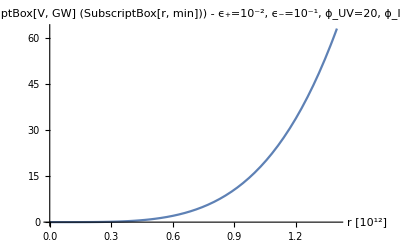

75.1296

{ϵp→0.01,ϵm→0.025,l→1,ϕUV→1,ϕIR→2.51866}

7.64015×10^-41

{7.64015×10^-41,7.64015×10^-41}

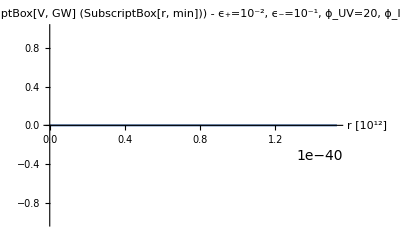

92.3726

on the equality we have

ϵm^(-1/(2 ϵm-4 ϵp)) (2+ϵm)^(-1/(2 ϵm-4 ϵp)) ϵp^(1/(2 ϵm-4 ϵp)) (2+ϵp)^(1/(2 ϵm-4 ϵp))

```mathematica
constrepl={ϵp->0.001,ϵm->0.02,l->1,ϕUV->100,(ϕIR->ϕUV ϵm^(-ϵp/(2 ϵm)) (2+ϵm)^(-ϵp/(2 ϵm)) ϵp^(ϵp/(2 ϵm)) (2+ϵp)^(ϵp/(2 ϵm))/.{ϵp->0.001,ϵm->0.02,ϕUV->100})}
r/.rsol/.constrepl
{((√ϵm √(2+ϵm)vevrat)/(√ϵp √(2+ϵp)))^(1/(-ϵm+ϵp)),(vevrat)^(1/ϵp)}/.vevrat->ϕIR/ϕUV/.constrepl

Plot[(VGWexpanded-VGWatmin)/(Abs@VGWatmin)/.constrepl/.r->rt ,{rt,0,1.4 },PlotLabel->"V_GW/(SubscriptBox[V, GW] (SubscriptBox[r, min])) - ϵ_+=10^-2, ϵ_-=10^-1, ϕ_UV=20, ϕ_IR=10^-1, l=1",AxesLabel->{"r [10^12]"}]
-Log@r/.rsol/.constrepl
constrepl={ϵp->0.01,ϵm->0.025,l->1,ϕUV->1,(ϕIR->ϕUV ϵm^(ϵp/(2 ϵm-4 ϵp)) (2+ϵm)^(ϵp/(2 ϵm-4 ϵp)) ϵp^(-ϵp/(2 ϵm-4 ϵp)) (2+ϵp)^(-ϵp/(2 ϵm-4 ϵp))/.{ϵp->0.01,ϵm->0.025,ϕUV->1})}
r/.rsol/.constrepl
{((√ϵm √(2+ϵm)vevrat)/(√ϵp √(2+ϵp)))^(1/(-ϵm+ϵp)),(vevrat)^(-1/ϵp)}/.vevrat->ϕIR/ϕUV/.constrepl

Plot[(VGWexpanded-VGWatmin)/(Abs@VGWatmin)/.constrepl/.r->rt ,{rt,0,2 %% },PlotLabel->"V_GW/(SubscriptBox[V, GW] (SubscriptBox[r, min])) - ϵ_+=10^-2, ϵ_-=10^-1, ϕ_UV=20, ϕ_IR=10^-1, l=1",AxesLabel->{"r [10^12]"}]
-Log@r/.rsol/.constrepl
Print["on the equality we have"]
r/.rsol/.ϕIR->ϕUV ϵm^(ϵp/(2 ϵm-4 ϵp)) (2+ϵm)^(ϵp/(2 ϵm-4 ϵp)) ϵp^(-ϵp/(2 ϵm-4 ϵp)) (2+ϵp)^(-ϵp/(2 ϵm-4 ϵp))//PowerExpand//Simplify
```